```mathematica
Clear[ndf,pdf,cdf]
ndf[θ_,α_]:=α^2/(π*(Cos[θ]^2*(α^2-1)+1)^2)
(*cdf=Function[{θ,α},Evaluate[Integrate[2*π*ndf[θ,α]*Cos[θ]*Sin[θ],θ]]]*)
cdf[θ_,α_]:=(1-Cos[θ]^2)/(1+Cos[θ]^2*(α^2-1))
pdf[θ_,α_]:=ndf[θ,α]*Cos[θ]
pdfCos[cosθ_,α_]:=α^2/(π*(cosθ^2*(α^2-1)+1)^2)*cosθ
```

Compute the difference of the PDFs of 2 neighbor pixels

```mathematica
(*Clear[α]
Integrate[2*π*(ndf[θ,α] - ndf[θ-β,α])*Cos[θ]*Sin[θ],θ]*)
```

```mathematica
ndf2[μ_,α_]:=α^2/(π*(μ^2*(α^2-1)+1)^2)
test[μ0_,α_]:=cdf[μ0,α]+ NIntegrate[2*π*(ndf2[μ,α] - ndf2[μ-μ0,α])*μ*√(1-μ^2),{μ,μ0,0}]
```

```mathematica
Manipulate[Plot[{test[μ0,α],cdf[μ0,α]},{α,0,1},PlotRange->{0,1}],{μ0,1,0}]
```

```mathematica
test[θ0_,α_]:=cdf[Cos[θ0],α]+ NIntegrate[2*π*(ndf[θ,α] - ndf[θ-θ0,α])*Cos[θ]*Sin[θ],{θ,θ0,π/2}]
Manipulate[Plot[{test[θ,α],cdf[Cos[θ],α]},{α,0,1},PlotRange->{-1,1}],{θ,0.01,π/2}]
```

Compute the correlation between 2 opposed NDFs separated by θ

Here we have 2 lobes aligned along 2 directions separated by an angle θ and we need to find the correlation least correlation between the 2 although there must be a little correlation anyway otherwise we could always choose roughness 0 for maximization.

Test with subtraction of the 2 lobes:

```mathematica
Manipulate[Show[Plot[(pdf[θ,α]*Sin[θ])/cdf[θ0/2,α]-(pdf[θ0-θ,α]*Sin[θ0-θ])/cdf[θ0/2,α],{θ,0,θ0},PlotRange->Full],ParametricPlot[{θ0/2,t},{t,-100,100},PlotStyle->Red]],{{θ0,π/10},0,π/2},{{α,0.1},0,1}]
```

Test with multiplication of the 2 lobes (true correlation):

```mathematica
Manipulate[Show[Plot[((pdf[θ,α]*Sin[θ])*(pdf[θ0-θ,α]*Sin[θ0-θ]))/cdf[θ0,α]^2,{θ,0,θ0},PlotRange->Full],ParametricPlot[{θ0/2,t},{t,-100,100},PlotStyle->Red]],{{θ0,π/10},0,π/2},{{α,0.1},0,1}]
```

Showing angular correlation visually:

```mathematica
ColorData[97,"ColorList"]
ColorData[97][1]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

-Graphics-

```mathematica
defaultBlue=ColorData[97][1];
Manipulate[ParametricPlot[ { 4*θ*{1,Tan[π/4-θ0/2]},4*θ*{1,Tan[π/4+θ0/2]}, 4*θ*{1,1},
pdf[Abs[θ-(π/4-θ0/2)],α]/cdf[θ0/2,α]*{Sin[θ],Cos[θ]},
pdf[Abs[(π/4+θ0/2)-θ],α]/cdf[θ0/2,α]*{Sin[θ],Cos[θ]},
(pdf[Abs[θ-(π/4-θ0/2)],α]*pdf[Abs[(π/4+θ0/2)-θ],α])/cdf[θ0/2,α]^2*{Sin[θ],Cos[θ]}
},{θ,0,π/2},PlotRange->{{0,1},{0,1}},PlotStyle->{LightGray,LightGray,Orange,defaultBlue,defaultBlue,Red}],{{α,0.1},0,1},{{θ0,π/2},0,π/2}]
```

```mathematica
(*Manipulate[Show[Plot[ndf[θ,α]*Cos[θ],{θ,0,π/2},PlotRange->Full],ParametricPlot[{θ0/2,t},{t,-100,100},PlotStyle->Red]],{{θ0,π/10},0,π/2},{{α,0.1},0,1}]*)
```

```mathematica
(*Clear[α]
Integrate[((pdf[θ,α]*Sin[θ])*(pdf[θ0-θ,α]*Sin[θ0-θ]))/cdf[θ0,α]^2,θ]*)
```

```mathematica
(*Manipulate[NIntegrate[2*π*(ndf[θ,α]*Cos[θ]-ndf[θ-θ0,α]*Cos[θ-θ0])*Sin[θ],{θ,0,θ0/2}],{{θ0,π/10},0,π/2},{{α,0.1},0,1}]*)
Manipulate[NIntegrate[((pdf[θ,α]*Sin[θ])*(pdf[θ0-θ,α]*Sin[θ0-θ]))/cdf[θ0,α]^2,{θ,0,θ0/2}],{{θ0,π/10},0,π/2},{{α,0.1},0,1}]
```

```mathematica
(*Manipulate[Plot[NIntegrate[2*π*(ndf[θ,α]*Cos[θ]-ndf[θ-θ0,α]*Cos[θ-θ0])*Sin[θ],{θ,0,θ0/2}],{α,0,1},PlotRange->{0,1}],{{θ0,π/10},0,π/2}]*)
Manipulate[Plot[NIntegrate[((pdf[θ,α]*Sin[θ])*(pdf[θ0-θ,α]*Sin[θ0-θ]))/cdf[θ0,α]^2,{θ,0,θ0/2}],{α,0,1},PlotRange->{0,1}],{{θ0,π/10},0,π/2}]
```

Show the correlation

```mathematica
(*Manipulate[Show[Plot[ndf[θ,α]*Cos[θ]*ndf[θ-θ0,α]*Cos[θ-θ0],{θ,0,θ0},PlotRange->{0,Full}],ParametricPlot[{θ0/2,t},{t,-100,100},PlotStyle->Red],ParametricPlot[{t,0.05},{t,0,θ0},PlotStyle->Red]],{{θ0,π/10},0,π/2},{{α,0.1},0,1}]*)
(*Manipulate[Show[Plot[((pdf[θ,α]*Sin[θ])*(pdf[θ0-θ,α]*Sin[θ0-θ]))/cdf[θ0,α]^2,{θ,0,θ0},PlotRange->{0,Full}],ParametricPlot[{θ0/2,t},{t,-100,100},PlotStyle->Red],ParametricPlot[{t,(1/π)^2},{t,0,θ0},PlotStyle->Red]],{{θ0,π/10},0,π/2},{{α,0.1},0,1}]*)
Manipulate[Show[Plot[(pdf[θ,α]*pdf[θ0-θ,α])/cdf[θ0/2,α]^2,{θ,0,θ0},PlotRange->{0,Full}],ParametricPlot[{θ0/2,t},{t,-100,100},PlotStyle->Red],ParametricPlot[{t,((√2)/π)^2},{t,0,θ0},PlotStyle->Red]],{{θ0,π/10},0,π/2},{{α,0.1},0,1}]
```

So okay, we can accept a certain amount of correlation that is given by the value at θ_0/2when α=1 and θ_0=π/2
Now we can find the roughness for a given θ_0 :

	c=((ndf(θ_0/2,α) cos(θ_0/2)sin(θ_0/2))/(cdf(θ_0/2,α)))^2

We can totally get rid of the squaring and rewrite the same expression for a new c.

By fixing c = (ndf(π/4,1) cos(π/4)sin(π/4))/(cdf(π/2,1)) corresponding to the correlation of the worst mip that sees a π/2 angle (a full face of the cube) and must correspond to the roughness value α=1.

We find:	c=1/π

```mathematica
(ndf[π/4,1]*Cos[π/4]*Sin[π/4])/cdf[π/4,1]
pdf[π/4,1]/cdf[π/4,1]
```

1/π

(√2)/π

```mathematica
Solve[(pdf[θ,α]*Sin[θ])/cdf[θ,α]==c,α]
```

{{α→-(ⅈ √c √π (-1+Cos[θ]^2))/(√(c π Cos[θ]^2-c π Cos[θ]^4-Cos[θ] Sin[θ]))},{α→(ⅈ √c √π (-1+Cos[θ]^2))/(√(c π Cos[θ]^2-c π Cos[θ]^4-Cos[θ] Sin[θ]))}}

```mathematica
Clear[c]
Solve[pdf[θ,α]/cdf[θ,α]==c,α]
```

{{α→-(ⅈ √c √π (-1+Cos[θ]^2))/(√(-Cos[θ]+c π Cos[θ]^2-c π Cos[θ]^4))},{α→(ⅈ √c √π (-1+Cos[θ]^2))/(√(-Cos[θ]+c π Cos[θ]^2-c π Cos[θ]^4))}}

```mathematica
(*cmax = 1/π;
c=cmax/(8π);
sqAlpha[θ_]:=(c*Cos[θ]^2)/(Sin[θ]-c*Sin[θ]^2)
sqAlpha[θ_]:=(-π*cmax* Sin[θ]^4)/(π*cmax* Cos[θ]^2-π*cmax* Cos[θ]^4-Cos[θ]*Sin[θ])*)
```

```mathematica
cmax=(√2)/π;
c=cmax * π;
(*sqAlpha[θ_]:=(-c*Sin[θ]^4)/(c* Cos[θ]^2-c* Cos[θ]^4-Cos[θ]*Sin[θ]) with sin(θ) *)
sqAlpha[θ_]:=(-c*Sin[θ]^4)/(c* Cos[θ]^2-c* Cos[θ]^4-Cos[θ])
```

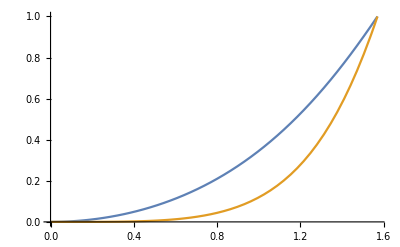

```mathematica
Plot[{√sqAlpha[θ/2],sqAlpha[θ/2]},{θ,0,π/2},PlotRange->{0,1}]
```

```mathematica
mipMax=8;
(*mu[mip_]:=1-1/3 2^(2(mip-mipMax))   Solid angles yields θ > π/2*)
mu[mip_]:=1/(√(1+2^(2(mip-mipMax))))
sqRoughnessFromMip[mip_]:=sqAlpha[ ArcCos[mu[mip]] ]

mu[8]
2*ArcCos[mu[8]]
Table[N[sqRoughnessFromMip[mip]],{mip,0,mipMax}]
```

1/(√2)

π/2

{3.29272×10^-10,5.26833×10^-9,8.42919×10^-8,1.34859×10^-6,0.0000215718,0.000344773,0.0054869,0.0846641,1.}

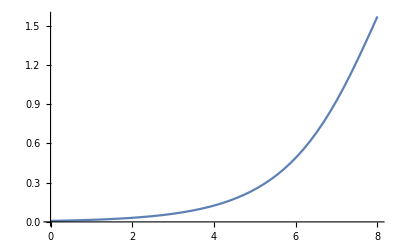

```mathematica
Plot[2*ArcCos[mu[mip]],{mip,0,mipMax},PlotRange->{0,π/2}]
```

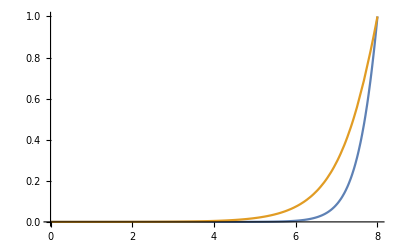

```mathematica
Plot[{sqRoughnessFromMip[mip],√sqRoughnessFromMip[mip]},{mip,0,mipMax},PlotRange->{0,1}]
```

Compute the correlation between 2 opposed NDFs separated by θ

Here we have 2 lobes aligned along 2 directions separated by an angle θ and we need to find the correlation least correlation between the 2 although there must be a little correlation anyway otherwise we could always choose roughness 0 for maximization.

It would look like we’re doing the same thing all over again but the normalization by pdf(0,α) makes much more sense than dividing by the cdf!

Showing angular correlation visually:

```mathematica
defaultBlue=ColorData[97][1];
(*correl[θ_,α_,θ0_]:=(pdf[Abs[θ-(π/4-θ0/2)],α]*pdf[Abs[(π/4+θ0/2)-θ],α])/pdf[0,α]^2
correl[θ_,α_,θ0_]:=Max[0,Min[pdf[Abs[θ-(π/4-θ0/2)],α],pdf[Abs[(π/4+θ0/2)-θ],α]]]/pdf[0,α]
Manipulate[ParametricPlot[ { 4*θ*{1,Tan[π/4-θ0/2]},4*θ*{1,Tan[π/4+θ0/2]},{Sin[θ],Cos[θ]},4*θ*{1,1},
pdf[Abs[θ-(π/4-θ0/2)],α]/pdf[0,α]*{Sin[θ],Cos[θ]},
pdf[Abs[(π/4+θ0/2)-θ],α]/pdf[0,α]*{Sin[θ],Cos[θ]},
correl[θ,α,θ0]*{Sin[θ],Cos[θ]},
(1/(√2))^2*{Sin[θ],Cos[θ]}
},{θ,0,π/2},PlotRange->{{0,1},{0,1}},PlotStyle->{LightGray,LightGray,LightGray,Orange,defaultBlue,defaultBlue,Red,Green}],{{α,0.1},0,1},{{θ0,π/2},0,π/2}]*)
```

```mathematica
correl[θ_,α_,θ0_]:=(pdf[θ,α]*pdf[θ0-θ,α])/pdf[0,α]^2
correl[θ_,α_,θ0_]:=Max[0,Min[pdf[θ,α],pdf[θ0-θ,α]]]/pdf[0,α]
Manipulate[ParametricPlot[ { 4*θ*{1,Tan[π/2-θ0]},{Sin[θ],Cos[θ]},4*θ*{Tan[θ0/2],1},
pdf[θ,α]/pdf[0,α]*{Sin[θ],Cos[θ]},
pdf[θ0-θ,α]/pdf[0,α]*{Sin[θ],Cos[θ]},
correl[θ,α,θ0]*{Sin[θ],Cos[θ]},
(1/(√2))^2*{Sin[θ],Cos[θ]}
},{θ,-π/2,π/2},PlotRange->{{-1,1},{0,1}},PlotStyle->{LightGray,LightGray,Orange,defaultBlue,defaultBlue,Red,Green}],{{α,0.1},0,1},{{θ0,π/2},0,π/2}]
```

Plotting angular correlation as a function of angle:

```mathematica
(*Manipulate[Show[Plot[((pdf[θ,α]*Sin[θ])*(pdf[θ0-θ,α]*Sin[θ0-θ]))/pdf[0,α]^2,{θ,0,θ0},PlotRange->Full],ParametricPlot[{θ0/2,t},{t,-100,100},PlotStyle->Red]],{{θ0,π/10},0,π/2},{{α,0.1},0,1}]*)
Manipulate[Show[Plot[(pdf[θ,α]*pdf[θ0-θ,α])/pdf[0,α]^2,{θ,0,θ0},PlotRange->{0,Full}],ParametricPlot[{θ0/2,t},{t,-100,100},PlotStyle->Red],ParametricPlot[{t,(1/(√2))^2},{t,0,θ0},PlotStyle->Red]],{{θ0,π/10},0,π/2},{{α,0.1},0,1}]
```

## Computing Surface Correlation

Let’s try and integrate the volume coverage of the interpenetration of the 2 lobes, instead of looking at a single value at the half-angle...

```mathematica
(*Manipulate[2π*NIntegrate[pdf[θ,α]*pdf[θ0-θ,α]*Sin[θ],{θ,0,π/2}],{{θ0,π/2},0,π/2},{{α,1},0.0001,1}]
Manipulate[(2π)/(0+1*pdf[0,α]^2)*NIntegrate[pdf[θ,α]*pdf[θ0-θ,α]*Sin[θ],{θ,0,π/2}],{{θ0,π/2},0,π/2},{{α,1},0.0001,1}]
Manipulate[(2π)/(1+0*pdf[0,α])*NIntegrate[Min[pdf[θ,α],pdf[θ0-θ,α]]*Sin[θ ],{θ,0,π/2}],{{θ0,π/2},0,π/2},{{α,1},0,1}]*)
```

```mathematica
Manipulate[1/2*NIntegrate[correl[θ,α,θ0]^2,{θ,-π/2,π/2}],{{θ0,π/2},0,π/2},{{α,1},0,1}]
Manipulate[1/(2*pdf[0,α]^2)*NIntegrate[(pdf[θ,α])^2,{θ,-π/2,π/2}],{{α,1},0,1}]
1/2 NIntegrate[Cos[θ]^2,{θ,-π/2,π/2}]
pdf[0,1]
```

0.785398

1/π

## Finding a Mapping

So okay, we can accept a certain amount of correlation that is given by the value at θ_0/2when α=1 and θ_0=π/2
Now we can find the roughness for a given θ_0 :

	c=((pdf(θ_0/2,α))/(pdf(0,α)))^2

We can totally get rid of the squaring and rewrite the same expression for a new c.

By fixing c = (pdf(π/4,1))/(pdf(0,1)) corresponding to the correlation of the worst mip that sees a π/2 angle (a full face of the cube) and must correspond to the roughness value α=1.

We find:	c=1/(√2)

```mathematica
(ndf[π/4,1]*Cos[π/4])/pdf[0,1]
pdf[π/4,1]/pdf[0,1]
```

1/(√2)

1/(√2)

```mathematica
Clear[c,θ,α]
(*Solve[pdf[θ,α]/pdf[0,α]==c,α]*)
Solve[(α^4*b)/((b^2(α^2-1)+1)^2)==c,α]
```

{{α→-√(-(b^2 c)/(-b+b^4 c)+(b^4 c)/(-b+b^4 c)-(√(b (-1+b^2)^2 c))/(-b+b^4 c))},{α→√(-(b^2 c)/(-b+b^4 c)+(b^4 c)/(-b+b^4 c)-(√(b (-1+b^2)^2 c))/(-b+b^4 c))},{α→-√(-(b^2 c)/(-b+b^4 c)+(b^4 c)/(-b+b^4 c)+(√(b (-1+b^2)^2 c))/(-b+b^4 c))},{α→√(-(b^2 c)/(-b+b^4 c)+(b^4 c)/(-b+b^4 c)+(√(b (-1+b^2)^2 c))/(-b+b^4 c))}}

Résultat impossible à inverser

```mathematica
(*Solve[(α^4*b)/((b^2(α^2-1)+1)^2)==c,b]*)
```

```mathematica
c=1/(√2);
sqAlpha:=Function[θ,
μ=Cos[θ];
(μ^4*c-μ^2*c-√(μ*(1-μ^2)^2*c))/(μ^4*c-μ)
]
sqAlphaMu[μ_]:=(μ^4*c-μ^2*c-√(μ*(1-μ^2)^2*c))/(μ^4*c-μ)
```

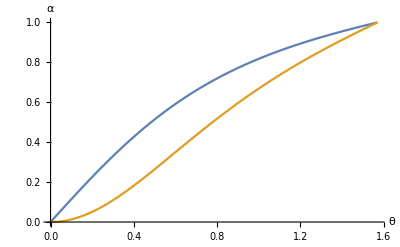

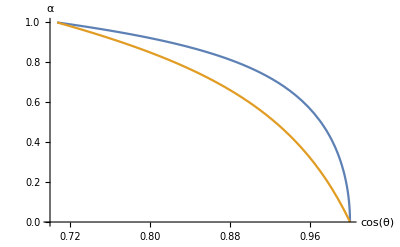

```mathematica
Plot[{√sqAlpha[θ/2],sqAlpha[θ/2]},{θ,0,π/2},PlotRange->{0,1},AxesLabel->{"θ","α"}]
Plot[{√sqAlphaMu[μ],sqAlphaMu[μ]},{μ,1/(√2),1},PlotRange->{{0.70,1},{0,1}},AxesLabel->{"cos(θ)","α"}]
```

2/3

1.68214

{0.00733224,0.0146636,0.0293201,0.0585836,0.116718,0.229944,0.434916,0.731737,1.02718}

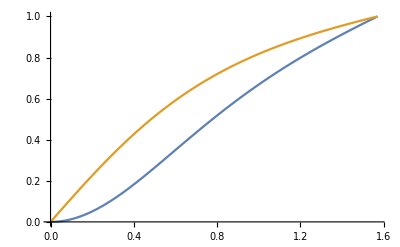

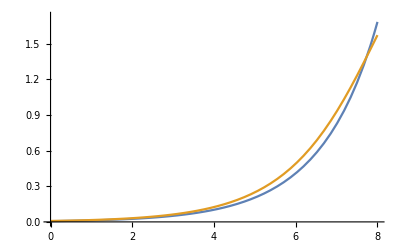

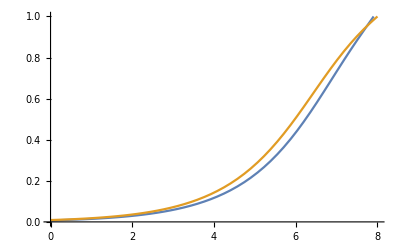

```mathematica
mipMax=8;
mu[mip_]:=1-1/3 2^(2(mip-mipMax))   (*Solid angles yields θ > π/2*)
mu2[mip_]:=1/(√(1+2^(2(mip-mipMax))))
sqRoughnessFromMip[mip_]:=sqAlpha[ArcCos[mu[mip]] ]
sqRoughnessFromMip2[mip_]:=sqAlpha[ArcCos[mu2[mip]] ]
mu[8]
N[2*ArcCos[mu[8]]]
Table[N[√sqRoughnessFromMip[mip]],{mip,0,mipMax}]
Plot[{sqAlpha[θ/2],√sqAlpha[θ/2]},{θ,0,π/2},PlotRange->{0,1}]
Plot[{2*ArcCos[mu[mip]],2*ArcCos[mu2[mip]]},{mip,0,mipMax},PlotRange->{0,1.1*π/2}]
Plot[{√sqRoughnessFromMip[mip],√sqRoughnessFromMip2[mip]},{mip,0,mipMax},PlotRange->{0,1}]
```

```mathematica
Manipulate[ParametricPlot[ { 4*θ*{1,Tan[π/4-θ0/2]},4*θ*{1,Tan[π/4+θ0/2]},{Sin[θ],Cos[θ]},4*θ*{1,1},
pdf[Abs[θ-(π/4-θ0/2)],√sqAlpha[θ0/2]]/pdf[0,√sqAlpha[θ0/2]]*{Sin[θ],Cos[θ]},
pdf[Abs[(π/4+θ0/2)-θ],√sqAlpha[θ0/2]]/pdf[0,√sqAlpha[θ0/2]]*{Sin[θ],Cos[θ]},
(pdf[Abs[θ-(π/4-θ0/2)],√sqAlpha[θ0/2]]*pdf[Abs[(π/4+θ0/2)-θ],√sqAlpha[θ0/2]])/pdf[0,√sqAlpha[θ0/2]]^2*{Sin[θ],Cos[θ]},
(1/(√2))^2*{Sin[θ],Cos[θ]}
},{θ,0,π/2},PlotRange->{{0,1},{0,1}},PlotStyle->{LightGray,LightGray,LightGray,Orange,defaultBlue,defaultBlue,Red,Green}],{{θ0,π/2},0.001,π/2}]
```

Fitting

The expression to get μ from roughness is a nightmare to invert so let’s do a curve fitting instead...

{{1.,0.707107},{0.995845,0.710036},{0.991663,0.712965},{0.987454,0.715894},{0.983216,0.718823},{0.978948,0.721751},{0.97465,0.72468},{0.970321,0.727609},{0.965958,0.730538},{0.961562,0.733467},{0.957132,0.736396},{0.952665,0.739325},{0.948161,0.742254},{0.943619,0.745183},{0.939037,0.748112},{0.934415,0.751041},{0.92975,0.75397},{0.925042,0.756899},{0.920289,0.759828},{0.915489,0.762756},{0.910642,0.765685},{0.905746,0.768614},{0.900799,0.771543},{0.895799,0.774472},{0.890746,0.777401},{0.885636,0.78033},{0.880469,0.783259},{0.875243,0.786188},{0.869956,0.789117},{0.864605,0.792046},{0.859189,0.794975},{0.853706,0.797904},{0.848154,0.800833},{0.84253,0.803762},{0.836832,0.80669},{0.831058,0.809619},{0.825206,0.812548},{0.819272,0.815477},{0.813254,0.818406},{0.80715,0.821335},{0.800956,0.824264},{0.794669,0.827193},{0.788287,0.830122},{0.781806,0.833051},{0.775224,0.83598},{0.768535,0.838909},{0.761738,0.841838},{0.754828,0.844767},{0.747801,0.847696},{0.740653,0.850624},{0.73338,0.853553},{0.725978,0.856482},{0.718442,0.859411},{0.710767,0.86234},{0.702948,0.865269},{0.694979,0.868198},{0.686856,0.871127},{0.678573,0.874056},{0.670123,0.876985},{0.6615,0.879914},{0.652698,0.882843},{0.64371,0.885772},{0.634528,0.888701},{0.625144,0.89163},{0.615552,0.894558},{0.605741,0.897487},{0.595704,0.900416},{0.58543,0.903345},{0.574911,0.906274},{0.564135,0.909203},{0.553092,0.912132},{0.541769,0.915061},{0.530155,0.91799},{0.518237,0.920919},{0.506001,0.923848},{0.493432,0.926777},{0.480515,0.929706},{0.467234,0.932635},{0.45357,0.935563},{0.439506,0.938492},{0.425022,0.941421},{0.410097,0.94435},{0.394707,0.947279},{0.37883,0.950208},{0.36244,0.953137},{0.345509,0.956066},{0.328008,0.958995},{0.309905,0.961924},{0.291167,0.964853},{0.271756,0.967782},{0.251635,0.970711},{0.23076,0.97364},{0.209086,0.976569},{0.186564,0.979497},{0.163139,0.982426},{0.138754,0.985355},{0.113346,0.988284},{0.0868448,0.991213},{0.0591763,0.994142},{0.030258,0.997071},{0.,1.}}

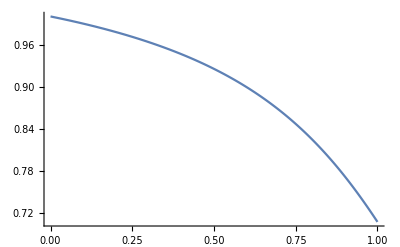

```mathematica
data=Table[{ N[sqAlphaMu[μ]],N[μ]},{μ,1/(√2),1,(1-1/(√2))/100}]
ListLinePlot[data,PlotRange->Full]
```

(a+b x+c x^2)/(d+e x+f x^2)

(a+b x+c x^2)/(a+e x+f x^2)

Function[x,(1.2547-1.87042 x+0.720235 x^2)/(1.2547-1.75224 x+0.645329 x^2)]

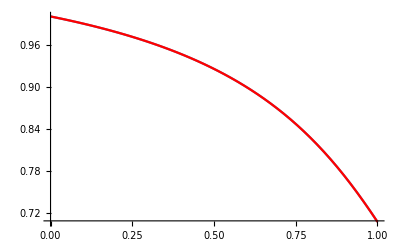

1.00011

```mathematica
Clear[a,b,c,d,e,f]
model=(a+b*x+c*x^2)/(d+e*x+f*x^2)
model=(a+b*x+c*x^2)/(a+e*x+f*x^2)

f0=Function[x,Evaluate[model/.FindFit[data,model,{a,b,c,d,e,f},x]]]
Show[ListLinePlot[data,PlotRange->{1/(√2),1}],Plot[f0[x],{x,0,1},PlotStyle->Red]]
√2 f0[1]
```

3D Lobes Inter-Penetration Modeling

Here we’re attempting to port the same reflection to the 3D realm. The idea is measuring how much 2 adjacent lobes interpenetrate each other depending on the separation angle (i.e. the lobe’s aperture angle) and the roughness of the lobe.
Once again we “normalize a lobe” by dividing by its largest amplitude at θ=0 and we’re looking to compute the integral:

	I=∫_-θ_0^θ_0 ∫_0^(π/2) ((D(θ,α) D( θ', α ) cos(θ)  cos(θ'))/(D( 0, α ))^2)^3 sin(θ)ⅆθⅆϕ

Here, cos(θ')= sin( θ ) cos( ϕ ) sin( θ_0) + cos( θ ) cos( θ_0 ) and θ_0 is the cone’s aperture angle.

```mathematica
cosAngleChange[θ_,ϕ_,γ_]:=Sin[θ]*Cos[ϕ]*Sin[γ]+Cos[θ]*Cos[γ]
penelobe[θ_,ϕ_,γ_,α_]:=pdf[θ,α]*pdfCos[cosAngleChange[θ,ϕ,γ],α]
```

```mathematica
γ=0.1
α=0.05
NIntegrate[penelobe[θ,ϕ,γ,α]^3*Sin[θ],{θ,0,π/2-0.01},{ϕ,-π/2,π/2}]
```

0.1

0.05

3.11641×10^6

1.0472

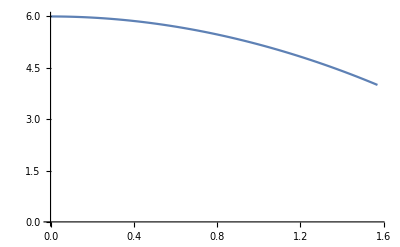

```mathematica
lobeSeparationAngle[θ0_]:=ArcCos[(Cos[θ0]-Cos[θ0]^2)/(1-Cos[θ0]^2)]
lobesCount[θ0_]:=(2π)/lobeSeparationAngle[Max[0.0001,θ0]]
lobeSeparationAngle[0.0001]
Plot[lobesCount[θ0],{θ0,0,π/2},PlotRange->{0,6}]
```

Here it’s interesting to realize the limit converges to 6 possible neighbors, I would have expected an unlimited amount of neighbors as the lobes get thinner and thinner...
But after all, if you zoom in on things, even though they’re getting very small, maybe you always end up with 6 neighbor lobes no matter what.

The other extremity of 4 lobes when the angle is π/2is totally expected, on the other hand: each face of the cube has exactly 4 neighbor faces, thus 4 neighbor lobes.

```mathematica
Manipulate[(1+0*lobesCount[θ0])*NIntegrate[(penelobe[θ,ϕ,θ0,α]/pdf[0,α]^2)^3*Sin[θ],{θ,0,π/2-0.01},{ϕ,-π,π}],{{θ0,π/10},0.001,π/2},{{α,0.9},0.001,1}]
```

```mathematica
Manipulate[(1+0*lobesCount[θ0])*NIntegrate[(penelobe[θ,ϕ,θ0,α]/pdf[0,α]^2)^3*Sin[θ],{θ,0,π/2-0.01},{ϕ,-π,π}],{{θ0,π/10},0.001,π/2},{{α,0.9},0.001,1}]
```

```mathematica
Manipulate[NIntegrate[penelobe[θ,ϕ,θ0,α]/pdf[0,α]^2*Sin[θ],{θ,0,π/2-0.01},{ϕ,-π/2,π/2}],{{θ0,π/10},0.001,π/2},{{α,0.9},0.001,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Manipulate[lobesCount[θ0]*NIntegrate[penelobe[θ,ϕ,θ0,α]*Sin[θ],{θ,0,π/2-0.01},{ϕ,-π/2,π/2}],{{θ0,π/10},0.001,π/2},{{α,0.9},0.0001,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Manipulate[NIntegrate[pdf[θ,α]/pdf[0,α]*Sin[θ],{θ,0,π/2-0.01},{ϕ,-π/2,π/2}],{{α,0.9},0.001,1}]
```

```mathematica
Manipulate[lobesCount[θ0]/2*NIntegrate[pdf[θ,α]*Sin[θ],{θ,0,π/2-0.01},{ϕ,-π/2,π/2}],{{θ0,π/10},0.001,π/2},{{α,0.9},0.0001,1}]
```

```mathematica
Manipulate[ParametricPlot3D[{
pdf[θ,α]/pdf[0,α]*{Sin[θ]*Cos[ϕ], Sin[θ]*Sin[ϕ], Cos[θ]},
pdfCos[cosAngleChange[θ,ϕ,γ],α]/pdf[0,α]*{Sin[θ]*Cos[ϕ], Sin[θ]*Sin[ϕ], Cos[θ]},
Min[pdf[θ,α],pdfCos[cosAngleChange[θ,ϕ,γ],α]]/pdf[0,α]*{Sin[θ]*Cos[ϕ], Sin[θ]*Sin[ϕ], Cos[θ]}
},{θ,0,π/2},{ϕ,-π,π},PlotRange->{{-1,1},{-1,1},{0,1}},AxesLabel->{"x","y","z"},PlotStyle->{Opacity[0.125],Opacity[0.125],Directive[Red,Opacity[1]]}],{{α,1},0.0001,1},{{γ,π/2},0.0001,π/2}]
```

```mathematica
penelobeMin[θ_,ϕ_,γ_,α_]:=Min[pdf[θ,α],pdfCos[cosAngleChange[θ,ϕ,γ],α]]
Manipulate[NIntegrate[penelobeMin[θ,ϕ,θ0,α]*Sin[θ],{θ,0,π/2},{ϕ,-π/2,π/2}, PrecisionGoal->2,MaxRecursion->4,WorkingPrecision->$MachinePrecision],{{θ0,π/2},0.001,π/2},{{α,1},0.0001,1}]
```

```mathematica
SetDirectory["D:\\Workspaces\\Patapom.com\\Web\\blog\\patapom\\docs\\BRDF"]; 
countX=128;
countY=64;
```

```mathematica
(*ta=ParallelTable[{N[θ0],N[α],
NIntegrate[penelobeMin[θ,ϕ,θ0,α]*Sin[θ],{θ,0,π/2},{ϕ,-π/2,π/2}, PrecisionGoal->2,MaxRecursion->4,WorkingPrecision->$MachinePrecision]
}
,{θ0,0,π/2,(π/2)/countX}
,{α,0.001,1,(1-0.001)/countY}]
Export["VolumeInterPenetration_"<>ToString[countX]<>"x"<>ToString[countY]<>".csv",ta,"CSV"];*)
```

```mathematica
ta=Import["VolumeInterPenetration_"<>ToString[countX]<>"x"<>ToString[countY]<>".csv","CSV"];
ta=ToExpression[ta]
```

{{{0.,0.001,0.500004888822118},{0.,0.0166094,0.499987470449681},{0.,0.0322188,0.499997428711909},{0.,0.0478281,0.500002007227455},{0.,0.0634375,0.499959181225379},55,{0.,0.937563,0.49999124339241},{0.,0.953172,0.499995427933608},{0.,0.968781,0.49999842603266},{0.,0.984391,0.500000213909253},{0.,1.,0.5000008023512}},127,{1}}
 |  |  |  |

```mathematica
ListPlot3D[Flatten[ta,1],PlotRange->Full]
```

-Graphics3D-

```mathematica
ta2=Table[ta[[x]][[y]] * {1,1,lobesCount[ta[[x]][[y]][[1]]]/lobesCount[π/2]},{x,1,countX+1},{y,1,countY+1}];
ta3=Table[ta[[x]][[y]] [[3]],{x,1,countX+1},{y,1,countY+1}]; (* This table doesn't account for lobes increase with angle *)
ta3=Table[lobesCount[ta[[x]][[y]][[1]]]/lobesCount[π/2]*ta[[x]][[y]] [[3]],{x,1,countX+1},{y,1,countY+1}];  (* This table will increase the amount of lobes from 4 at π/2 to 6 at 0° *)
roughnessFunction=ListInterpolation[ta3,{{0,π/2},{0,1}}]
ta[[countX+1]][[countY+1]]
ref=ta2[[countX+1]][[countY+1]][[3]]
```

InterpolatingFunction[{{0., 1.5708}, {0., 1.}}, <>]

{1.5708,1.,0.292971659095527}

0.292972

```mathematica
Show[(*ListPlot3D[Flatten[ta2,1],PlotRange->Full,AxesLabel->{"θ","α","Penetration"}],*)
Plot3D[roughnessFunction[θ,α],{θ,0,π/2},{α,0,1}],
Plot3D[ref,{θ,0,π/2},{α,0,1},PlotStyle->Darker[Green,0.1]]]
```

-Graphics3D-

```mathematica
Clear[α]
NSolve[roughnessFunction[0.2,α]==ref,α]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{α→0.0836709}}

```mathematica
roughnessMap=Table[{N[θ0],α/.NSolve[roughnessFunction[Max[0.0001,θ0],α]==ref,α][[1]]},{θ0,0,π/2,(π/2)/200}]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve :: ifun will be suppressed during this calculation.

{{0.,-0.0671502},{0.00785398,0.00220562},{0.015708,0.00542021},{0.0235619,0.00763341},{0.0314159,0.0112595},{0.0392699,0.0155071},{0.0471239,0.0192773},{0.0549779,0.0226499},{0.0628319,0.0257924},{0.0706858,0.028858},{0.0785398,0.0321196},{0.0863938,0.0356104},{0.0942478,0.0388111},{0.102102,0.0423442},{0.109956,-0.0620999},{0.11781,-0.0420524},{0.125664,0.0524775},{0.133518,0.0559296},{0.141372,0.0590105},{0.149226,0.0621656},{0.15708,-0.04316},{0.164934,-0.0453848},{0.172788,0.0717699},{0.180642,0.0753208},{0.188496,0.078856},{0.19635,0.0823181},{0.204204,0.0853366},{0.212058,-0.0595702},{0.219911,-0.0619615},{0.227765,-0.0644098},{0.235619,-0.0670197},{0.243473,-0.0698507},{0.251327,-0.0723795},{0.259181,-0.0751265},{0.267035,-0.0789801},{0.274889,-0.0811033},{0.282743,-0.0819213},{0.290597,-0.0846479},{0.298451,-0.0857521},{0.306305,-0.0856344},{0.314159,-0.0903038},{0.322013,0.136212},{0.329867,0.139542},{0.337721,0.143352},{0.345575,-0.103419},{0.353429,-0.106019},{0.361283,0.153883},{0.369137,0.157446},{0.376991,0.160835},{0.384845,0.164067},{0.392699,0.167385},{0.400553,0.170876},{0.408407,-0.124562},{0.416261,0.178001},{0.424115,-0.129769},{0.431969,0.184512},{0.439823,-0.13505},{0.447677,0.191719},{0.455531,0.195351},{0.463385,0.198812},{0.471239,0.202461},{0.479093,0.206214},{0.486947,0.209829},{0.494801,0.213475},{0.502655,0.217186},{0.510509,0.221238},{0.518363,0.226291},{0.526217,0.229538},{0.534071,0.232091},{0.541925,0.235937},{0.549779,0.241073},{0.557633,0.244172},{0.565487,0.24618},{0.573341,0.249188},{0.581195,0.25235},{0.589049,0.255665},{0.596903,0.259566},{0.604757,0.26426},{0.612611,0.2693},{0.620465,0.273007},{0.628319,0.276739},{0.636173,0.28074},{0.644026,0.284679},{0.65188,0.288558},{0.659734,0.292228},{0.667588,0.296263},{0.675442,0.300522},{0.683296,0.304239},{0.69115,0.307951},{0.699004,0.311781},{0.706858,0.315524},{0.714712,0.319336},{0.722566,0.323475},{0.73042,0.327596},{0.738274,0.332005},{0.746128,0.336991},{0.753982,0.341272},{0.761836,0.345052},{0.76969,0.348976},{0.777544,0.353455},{0.785398,0.358153},{0.793252,0.362061},{0.801106,0.366248},{0.80896,0.370921},{0.816814,0.37465},{0.824668,0.378421},{0.832522,0.382773},{0.840376,0.387222},{0.84823,0.391656},{0.856084,0.395996},{0.863938,0.400079},{0.871792,0.404223},{0.879646,0.408952},{0.8875,0.412957},{0.895354,0.416932},{0.903208,0.421295},{0.911062,0.426288},{0.918916,0.431912},{0.92677,0.434805},{0.934624,0.441452},{0.942478,0.448173},{0.950332,0.450211},{0.958186,0.452838},{0.96604,0.457446},{0.973894,0.462074},{0.981748,0.466994},{0.989602,0.47273},{0.997456,0.478183},{1.00531,0.482956},{1.01316,0.487364},{1.02102,0.492148},{1.02887,0.497082},{1.03673,0.502073},{1.04458,0.507262},{1.05243,0.512454},{1.06029,0.517627},{1.06814,0.522792},{1.076,0.528003},{1.08385,0.53321},{1.0917,0.538415},{1.09956,0.543656},{1.10741,0.548786},{1.11527,0.554231},{1.12312,0.562596},{1.13097,0.570561},{1.13883,0.575432},{1.14668,0.580154},{1.15454,0.584751},{1.16239,0.589321},{1.17024,0.593525},{1.1781,0.596715},{1.18595,0.601106},{1.19381,0.606426},{1.20166,0.612365},{1.20951,0.618202},{1.21737,0.624367},{1.22522,0.631069},{1.23308,0.637494},{1.24093,0.644265},{1.24878,0.652084},{1.25664,0.659248},{1.26449,0.666028},{1.27235,0.67268},{1.2802,0.678879},{1.28805,0.685652},{1.29591,0.692615},{1.30376,0.700695},{1.31161,0.707668},{1.31947,0.714463},{1.32732,0.721357},{1.33518,0.728292},{1.34303,0.735235},{1.35088,0.74237},{1.35874,0.749971},{1.36659,0.757452},{1.37445,0.764731},{1.3823,0.772033},{1.39015,0.779868},{1.39801,0.788121},{1.40586,0.796008},{1.41372,0.803935},{1.42157,0.811951},{1.42942,0.819828},{1.43728,0.827865},{1.44513,0.836521},{1.45299,0.845218},{1.46084,0.854328},{1.46869,0.86353},{1.47655,0.87269},{1.4844,0.881862},{1.49226,0.891204},{1.50011,0.901023},{1.50796,0.910564},{1.51582,0.921278},{1.52367,0.931895},{1.53153,0.942429},{1.53938,0.953293},{1.54723,0.964645},{1.55509,0.975838},{1.56294,0.987623},{1.5708,1.}}

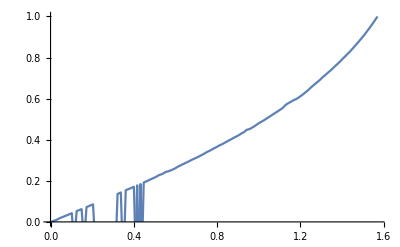

```mathematica
ListLinePlot[roughnessMap,PlotRange->{0,1}]
```

```mathematica
ta3[[129]]
ListInterpolation[ta3[[129]],{0,1}]
```

{4.99011×10^-7,0.000137635,0.000517598,0.00113956,0.00200219,0.0031036,0.00444146,0.00601289,0.00781458,0.00984274,0.0120932,0.0145613,0.017242,0.0201301,0.0232198,0.0265051,0.0299798,0.0336374,0.0374713,0.0414745,0.04564,0.0499608,0.0544295,0.059039,0.0637819,0.0686508,0.0736386,0.0787379,0.0839416,0.0892425,0.0946337,0.100045,0.105595,0.111216,0.1169,0.122641,0.128434,0.134273,0.140151,0.146064,0.152006,0.157994,0.163979,0.169978,0.175988,0.182002,0.188018,0.194031,0.200038,0.206035,0.21202,0.217987,0.223936,0.229863,0.235765,0.24164,0.247486,0.2533,0.259081,0.264827,0.270536,0.276206,0.281836,0.287425,0.292972}

InterpolatingFunction[{{0., 1.}}, <>]

```mathematica
taRoughnessFunctions=Table[ListInterpolation[ta3[[θ]],{0,1}],{θ,1,countX+1}];
```

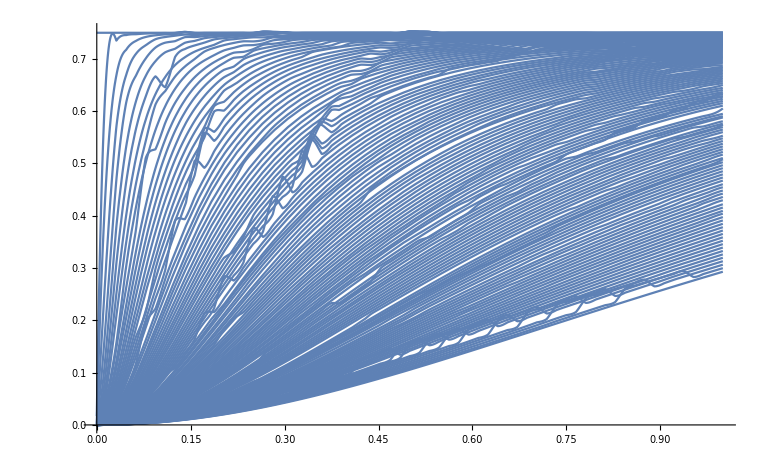

```mathematica
Plot[Table[taRoughnessFunctions[[x]][α],{x,1,countX+1}],{α,0,1},PlotRange->Full]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve :: ifun will be suppressed during this calculation.

{{0.00613592,0.00435388},{0.0122718,0.00798209},{0.0184078,0.0142397},{0.0245437,0.0201553},{0.0306796,0.0252147},{0.0368155,0.0300223},{0.0429515,0.0354113},{0.0490874,0.0404804},{0.0552233,-0.0658214},{0.0613592,0.051045},{0.0674952,0.0565301},{0.0736311,-0.0402626},{0.079767,-0.0439439},{0.0859029,0.0713379},{0.0920388,0.0768892},{0.0981748,0.0823181},{0.104311,-0.0585104},{0.110447,-0.0622605},{0.116583,-0.0661593},{0.122718,-0.0705562},{0.128854,-0.0744469},{0.13499,-0.0803063},{0.141126,-0.0817714},{0.147262,-0.0858957},{0.153398,-0.0856887},{0.159534,0.135034},{0.16567,0.140202},{0.171806,-0.102752},{0.177942,-0.106822},{0.184078,0.157011},{0.190214,0.16227},{0.19635,0.167385},{0.202485,0.172856},{0.208621,0.178433},{0.214757,-0.131462},{0.220893,0.189134},{0.227029,0.194696},{0.233165,0.200133},{0.239301,0.205986},{0.245437,0.211629},{0.251573,0.217418},{0.257709,0.22455},{0.263845,0.230028},{0.269981,0.23466},{0.276117,0.242498},{0.282252,0.245839},{0.288388,0.250602},{0.294524,0.255665},{0.30066,0.262018},{0.306796,0.269887},{0.312932,0.275454},{0.319068,0.281708},{0.325204,0.287863},{0.33134,0.293635},{0.337476,0.300281},{0.343612,0.306052},{0.349748,0.312021},{0.355884,0.317855},{0.362019,0.324275},{0.368155,0.330782},{0.374291,0.338491},{0.380427,0.34458},{0.386563,0.350833},{0.392699,0.358153},{0.398835,0.364227},{0.404971,0.371478},{0.411107,0.377125},{0.417243,0.38389},{0.423379,0.390831},{0.429515,0.397588},{0.435651,0.403923},{0.441786,0.411095},{0.447922,0.4172},{0.454058,0.424182},{0.460194,0.432875},{0.46633,0.43838},{0.472466,0.449222},{0.478602,0.452286},{0.484738,0.459453},{0.490874,0.466994},{0.49701,0.475944},{0.503146,0.483524},{0.509282,0.490576},{0.515418,0.498288},{0.521553,0.506292},{0.527689,0.514403},{0.533825,0.522467},{0.539961,0.530612},{0.546097,0.538741},{0.552233,0.546967},{0.558369,0.555424},{0.564505,0.569082},{0.570641,0.576769},{0.576777,0.584212},{0.582913,0.591416},{0.589049,0.596715},{0.595185,0.603977},{0.60132,0.613132},{0.607456,0.62233},{0.613592,0.632755},{0.619728,0.64284},{0.625864,0.654972},{0.632,0.665593},{0.638136,0.675708},{0.644272,0.686091},{0.650408,0.697668},{0.656544,0.708904},{0.66268,0.71963},{0.668816,0.73047},{0.674952,0.741436},{0.681087,0.753312},{0.687223,0.764731},{0.693359,0.776314},{0.699495,0.78915},{0.705631,0.801413},{0.711767,0.813951},{0.717903,0.826259},{0.724039,0.839728},{0.730175,0.85376},{0.736311,0.868149},{0.742447,0.882443},{0.748583,0.897328},{0.754719,0.912452},{0.760854,0.929299},{0.76699,0.945774},{0.773126,0.963088},{0.779262,0.980931},{0.785398,1.}}

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve :: ifun will be suppressed during this calculation.

{{0.999981,0.00435388},{0.999925,0.00798209},{0.999831,0.0142397},{0.999699,0.0201553},{0.999529,0.0252147},{0.999322,0.0300223},{0.999078,0.0354113},{0.998795,0.0404804},{0.998476,-0.0658214},{0.998118,0.051045},{0.997723,0.0565301},{0.99729,-0.0402626},{0.99682,-0.0439439},{0.996313,0.0713379},{0.995767,0.0768892},{0.995185,0.0823181},{0.994565,-0.0585104},{0.993907,-0.0622605},{0.993212,-0.0661593},{0.99248,-0.0705562},{0.99171,-0.0744469},{0.990903,-0.0803063},{0.990058,-0.0817714},{0.989177,-0.0858957},{0.988258,-0.0856887},{0.987301,0.135034},{0.986308,0.140202},{0.985278,-0.102752},{0.98421,-0.106822},{0.983105,0.157011},{0.981964,0.16227},{0.980785,0.167385},{0.97957,0.172856},{0.978317,0.178433},{0.977028,-0.131462},{0.975702,0.189134},{0.974339,0.194696},{0.97294,0.200133},{0.971504,0.205986},{0.970031,0.211629},{0.968522,0.217418},{0.966976,0.22455},{0.965394,0.230028},{0.963776,0.23466},{0.962121,0.242498},{0.960431,0.245839},{0.958703,0.250602},{0.95694,0.255665},{0.955141,0.262018},{0.953306,0.269887},{0.951435,0.275454},{0.949528,0.281708},{0.947586,0.287863},{0.945607,0.293635},{0.943593,0.300281},{0.941544,0.306052},{0.939459,0.312021},{0.937339,0.317855},{0.935184,0.324275},{0.932993,0.330782},{0.930767,0.338491},{0.928506,0.34458},{0.92621,0.350833},{0.92388,0.358153},{0.921514,0.364227},{0.919114,0.371478},{0.916679,0.377125},{0.91421,0.38389},{0.911706,0.390831},{0.909168,0.397588},{0.906596,0.403923},{0.903989,0.411095},{0.901349,0.4172},{0.898674,0.424182},{0.895966,0.432875},{0.893224,0.43838},{0.890449,0.449222},{0.88764,0.452286},{0.884797,0.459453},{0.881921,0.466994},{0.879012,0.475944},{0.87607,0.483524},{0.873095,0.490576},{0.870087,0.498288},{0.867046,0.506292},{0.863973,0.514403},{0.860867,0.522467},{0.857729,0.530612},{0.854558,0.538741},{0.851355,0.546967},{0.84812,0.555424},{0.844854,0.569082},{0.841555,0.576769},{0.838225,0.584212},{0.834863,0.591416},{0.83147,0.596715},{0.828045,0.603977},{0.824589,0.613132},{0.821103,0.62233},{0.817585,0.632755},{0.814036,0.64284},{0.810457,0.654972},{0.806848,0.665593},{0.803208,0.675708},{0.799537,0.686091},{0.795837,0.697668},{0.792107,0.708904},{0.788346,0.71963},{0.784557,0.73047},{0.780737,0.741436},{0.776888,0.753312},{0.77301,0.764731},{0.769103,0.776314},{0.765167,0.78915},{0.761202,0.801413},{0.757209,0.813951},{0.753187,0.826259},{0.749136,0.839728},{0.745058,0.85376},{0.740951,0.868149},{0.736817,0.882443},{0.732654,0.897328},{0.728464,0.912452},{0.724247,0.929299},{0.720003,0.945774},{0.715731,0.963088},{0.711432,0.980931},{0.707107,1.}}

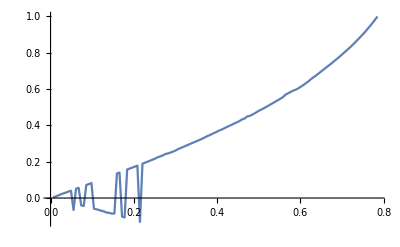

```mathematica
roughnessMap2=Table[{N[(θ0-1)/countX*π/4],α/.NSolve[taRoughnessFunctions[[θ0]][α]==ref,α][[1]]},{θ0,2,countX+1}]
roughnessMapCos2=Table[{N[Cos[(θ0-1)/countX*π/4]],α/.NSolve[taRoughnessFunctions[[θ0]][α]==ref,α][[1]]},{θ0,2,countX+1}]
ListLinePlot[roughnessMap2]
```

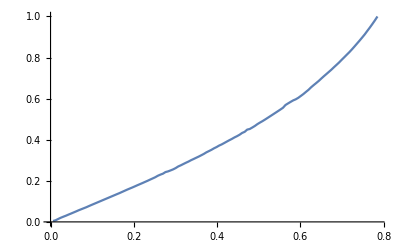

```mathematica
roughnessMap3={};
For[i=1,i<=countX,i++,If[roughnessMap2[[i]][[2]]≥0,AppendTo[roughnessMap3,roughnessMap2[[i]]]]]
ListLinePlot[roughnessMap3]
```

Let’s fit this...

{a→1.,b→0.813346,c→-0.605152,d→1.,e→-0.934716,f→1.}

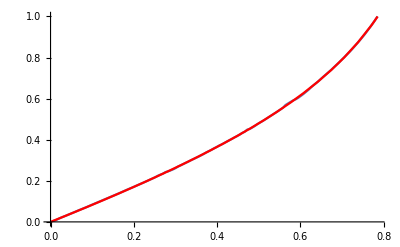

```mathematica
Clear[a,b,c,d,e,f,x,model]
model=0+b*x+c*x^2+d*x^3+e*x^4+f*x^5;
model=(0+b*x+c*x^2)/(1+e*x+0*f*x^2);
FindFit[roughnessMap3,model,{a,b,c,d,e,f},x]
f2=Function[x,Evaluate[model/.FindFit[roughnessMap3,model,{a,b,c,d,e,f},x]]];
Show[ListLinePlot[roughnessMap3,PlotRange->{0,1}],Plot[f2[x],{x,0,π/2},PlotRange->{0,1},PlotStyle->Red]]
```

```mathematica
Sum[(f2[roughnessMap3[[i]][[1]]] - roughnessMap3[[i]][[2]])^2,{i,1,Length[roughnessMap3]}]
```

0.000208134

Let’s plot and compare with the 2D model

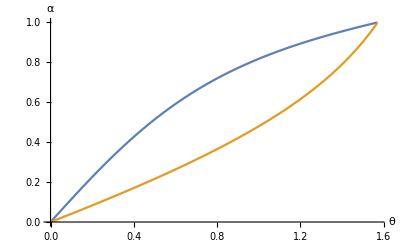

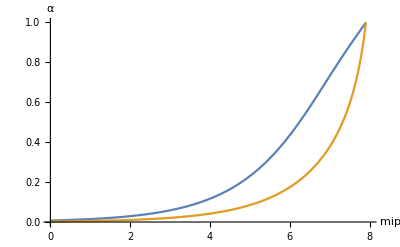

```mathematica
c=1/(√2);
sqAlpha:=Function[θ,
μ=Cos[θ];
(μ^4*c-μ^2*c-√(μ*(1-μ^2)^2*c))/(μ^4*c-μ)
]
sqAlphaMu[μ_]:=(μ^4*c-μ^2*c-√(μ*(1-μ^2)^2*c))/(μ^4*c-μ)
sqRoughnessFromMip[mip_]:=sqAlphaMu[mu[mip]] 
sqRoughnessFromMip3D[mip_]:=f2[mu[mip]]^2
sqRoughnessFromMip3D[mip_]:=f2[ArcCos[mu[mip]]]^2
(*Plot[{sqAlpha[θ/2],√sqAlpha[θ/2]},{θ,0,π/2},PlotRange->{0,1}]*)
Plot[{sqAlpha[θ/2]^(1/2),f2[θ/2]},{θ,0,π/2},PlotRange->{0,1},AxesLabel->{"θ","α"}]
Plot[{√sqRoughnessFromMip[mip],√sqRoughnessFromMip3D[mip]},{mip,0,mipMax},PlotRange->{0,1},AxesLabel->{"mip","α"}]
```

Let’s map the inverse function now:

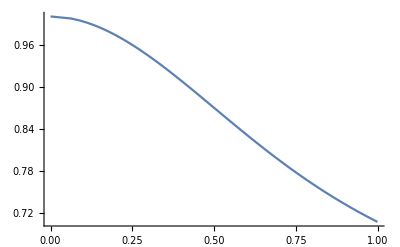

```mathematica
data=Table[{ N[f2[ArcCos[μ]]],N[μ]},{μ,1/(√2),1,(1-1/(√2))/100}];
ListLinePlot[data,PlotRange->Full]
```

(a+b x+c x^2)/(d+e x+f x^2)

(a+b x+c x^2)/(a+e x+f x^2)

Function[x,(14.0653-3.07501 x+10.5404 x^2)/(14.0653-2.91058 x+19.3144 x^2)]

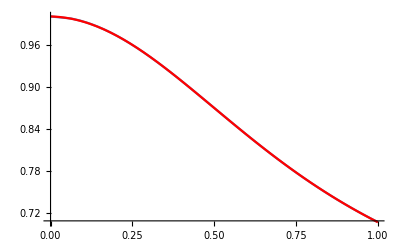

0.99934

```mathematica
Clear[a,b,c,d,e,f]
model=(a+b*x+c*x^2)/(d+e*x+f*x^2)
model=(a+b*x+c*x^2)/(a+e*x+f*x^2)
f3=Function[x,Evaluate[model/.FindFit[data,model,{a,b,c,d,e,f},x]]]
Show[ListLinePlot[data,PlotRange->{1/(√2),1}],Plot[f3[x],{x,0,1},PlotStyle->Red]]
√2 f3[1]
```

Let’s plot and compare with the 2D model:

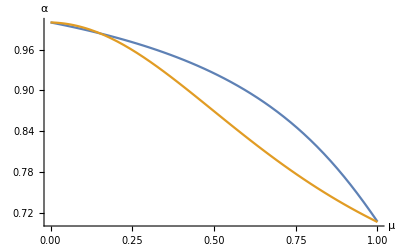

```mathematica
Plot[{f0[μ],f3[μ]},{μ,0,1},AxesLabel->{"μ","α"}]
```

3D Lobes Inter-Penetration Modeling

We’re starting over again but this time measuring the ratio of volume that get interpenetrated depending on the angle between lobes.
We know a volume element is given by dV=r^2 sin(θ) dr dθ dϕ and the volume integral is:

	I=∫_-π^π ∫_0^(π/2) ∫_0^(r(θ,ϕ,α)) r^2 sin(θ)ⅆθⅆϕ=∫_-π^π ∫_0^(π/2) 1/3(r(θ,ϕ,α))^3 sin(θ)ⅆθⅆϕ

In one case, we’re looking for the entire volume so r(θ,ϕ,α)=r(θ )=(D(θ,α))/π cos(θ) the BRDF’s normal distribution function times the cosine of the angle.
In the second case we’re looking for the intersection of 2 volumes and r(θ,ϕ,α)=r(θ )=min( D(θ,α) cos(θ), D(θ',α) cos(θ') ).

Here, cos(θ')= sin( θ ) cos( ϕ ) sin( θ_0) + cos( θ ) cos( θ_0 ) and θ_0 is the cone’s aperture angle.

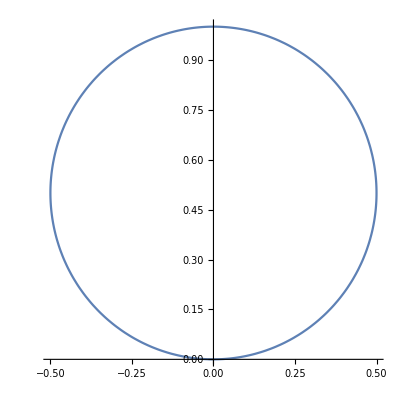

```mathematica
ParametricPlot[Cos[θ]*{Sin[θ],Cos[θ]},{θ,-π/2,π/2}]
```

```mathematica
cosAngleChange[θ_,ϕ_,γ_]:=Sin[θ]*Cos[ϕ]*Sin[γ]+Cos[θ]*Cos[γ]
penelobe[θ_,ϕ_,γ_,α_]:=π*Max[0,Min[pdf[θ,α],pdfCos[cosAngleChange[θ,ϕ,γ],α]]]
Manipulate[(2π)/3*NIntegrate[Cos[θ]^3*Sin[θ],{θ,0,π/2}],{{α,1},0.001,1}]
Manipulate[(2π)/3*NIntegrate[(π*pdf[θ,α])^3*Sin[θ],{θ,0,π/2}],{{α,1},0.001,1}]
Manipulate[1/3 NIntegrate[penelobe[θ,ϕ,θ0,α]^3*Sin[θ],{θ,0,π/2},{ϕ,-π,π}],{{α,1},0.001,1},{{θ0,π/2},0,π/2}]
```

```mathematica
SetDirectory["D:\\Workspaces\\Patapom.com\\Web\\blog\\patapom\\docs\\BRDF"]; 
countX=128;
countY=64;
fileName="VolumeInterPenetrationProper_"<>ToString[countX]<>"x"<>ToString[countY]<>".csv"
```

VolumeInterPenetrationProper_128x64.csv

```mathematica
ta=ParallelTable[{N[θ0],N[α],
1/3 NIntegrate[penelobe[θ,ϕ,θ0,α]^3*Sin[θ],{θ,0,π/2},{ϕ,-π,π}, PrecisionGoal->2,MaxRecursion->4,WorkingPrecision->$MachinePrecision]
}
,{θ0,0,π/2,(π/2)/countX}
,{α,0.001,1,(1-0.001)/countY}]
Export[fileName,ta,"CSV"];
```

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 8
     recursive bisections in θ near {θ, ϕ} = 
    {0.0380646410742078031875276130279407653210430598733503904454256583452, 
     0.331486562876674817164652347399784723096781240636829373060911319431}.
     NIntegrate obtained 0.000033921701058431786488743513656475498827136157192
     6399112084165635504 and 1.15806233412477063198018080464733404931893087589
                           -6
      079099172963374595 10   for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 8
     recursive bisections in θ near {θ, ϕ} = 
    {0.115626094272714212557899999371541705881006854017709189039344332181, 
     0.362092822287699485986241385154861374140326379436024969003474124096}.
     NIntegrate obtained 5.765773599215182668070126570911132730354167235984795
                       -10
      37464179216464 10    and 7.541686114864601795679423679038075381039265287
                             -12
      66813810566586605554 10    for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 8
     recursive bisections in θ near {θ, ϕ} = 
    {0.1892571720912250, 0.3314865628766748}. NIntegrate obtained 
                        -12                         -14
    3.553950152079806 10    and 7.374423377868571 10
     for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 8
     recursive bisections in θ near {θ, ϕ} = 
    {0.0380646410742078031875276130279407653210430598733503904454256583452, 
     0.331486562876674817164652347399784723096781240636829373060911319431}.
     NIntegrate obtained 303.6384452926751940601357510295323537648385552520442
     16983045681495 and 7.4930006280863623584226399090481807805546301489533454
     4285649687954 for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 8
     recursive bisections in θ near {θ, ϕ} = 
    {0.115626094272714212557899999371541705881006854017709189039344332181, 
     0.362092822287699485986241385154861374140326379436024969003474124096}.
     NIntegrate obtained 0.010942501710999392308821977775269789606883745841543
     0054108203206747 and 0.00014109293110381544591403795741272929109879307231
     2353692961423345872 for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 8
     recursive bisections in θ near {θ, ϕ} = 
    {0.1892571720912250, 0.3314865628766748}. NIntegrate obtained 
                                                   -6
    0.00007198406222202939 and 1.482891368217031 10
     for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 8
     recursive bisections in θ near {θ, ϕ} = 
    {0.00629997784365289811690805902451066707520148095772243470753453472911, 
     0.165743281438337408582326173699892361548390620318414686530455659716}.
     NIntegrate obtained 1810.037474478585667418156253483638359554074321023988
     92598604184441 and 59.513039504923474674903493482035726139933637876392777
     2854293300679 for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 8
     recursive bisections in θ near {θ, ϕ} = 
    {0.0380646410742078031875276130279407653210430598733503904454256583452, 
     0.331486562876674817164652347399784723096781240636829373060911319431}.
     NIntegrate obtained 2773.016458906532356018176137276003756552526541221252
     03922302849570 and 50.315434012241227495438764778688082349747483935613837
     5982344225979 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb
     will be suppressed during this calculation.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 8
     recursive bisections in θ near {θ, ϕ} = 
    {0.1892571720912250, 0.3314865628766748}. NIntegrate obtained 
    0.003476609728607331 and 0.00007023565410539100
     for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb
     will be suppressed during this calculation.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 8
     recursive bisections in θ near {θ, ϕ} = 
    {0.0129250587515585403821562336076277175343058621734474668548590511762, 
     0.331486562876674817164652347399784723096781240636829373060911319431}.
     NIntegrate obtained 1.942646986665120900383492296708391985060031729175670
     31368507702243 and 0.0295482237345089011243343022806908031089351140644254
     979339432072059 for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 8
     recursive bisections in θ near {θ, ϕ} = 
    {0.1217620174242568, 0.3314865628766748}. NIntegrate obtained 
    1.997268990142256 and 0.04082858397589183
     for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb
     will be suppressed during this calculation.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 8
     recursive bisections in θ near {θ, ϕ} = 
    {0.090181122348515666974531508810560267747323614928991079878700153768, 
     0.331486562876674817164652347399784723097401404714418770418942040770}.
     NIntegrate obtained 7.117047326370079565426520899598284620880882443428990
                       -9
      15678687623028 10   and 1.0050081309074577063363400105495663084438272561
                            -10
      5205206019424934835 10    for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 8
     recursive bisections in θ near {θ, ϕ} = 
    {0.090181122348515666974531508810560267747323614928991079878700153768, 
     0.331486562876674817164652347399784723097401404714418770418942040770}.
     NIntegrate obtained 0.126499520143266664476869441678981288084580797172812
     678903107733389 and 0.001731476668932854957122167477366536717513792106601
     76801020379201333 for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 8
     recursive bisections in θ near {θ, ϕ} = 
    {0.090181122348515666974531508810560267747323614928991079878700153768, 
     0.331486562876674817164652347399784723097401404714418770418942040770}.
     NIntegrate obtained 4.358159120534131117544611357068240234244464705524450
     44036374824240 and 0.0549004623955119348124145984399810223302231616910898
     945427779528337 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb
     will be suppressed during this calculation.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 8
     recursive bisections in θ near {θ, ϕ} = 
    {0.1708494026365973, 0.3314865628766748}. NIntegrate obtained 
                        -11                         -13
    1.012395897048933 10    and 2.190886154383656 10
     for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 8
     recursive bisections in θ near {θ, ϕ} = 
    {0.1708494026365973, 0.3314865628766748}. NIntegrate obtained 
                                                  -6
    0.0002033175106684331 and 4.354382127577137 10
     for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 8
     recursive bisections in θ near {θ, ϕ} = 
    {0.1708494026365973, 0.3314865628766748}. NIntegrate obtained 
    0.00958179464150592 and 0.0002002380725147644
     for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb
     will be suppressed during this calculation.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 8
     recursive bisections in θ near {θ, ϕ} = 
    {0.0314615450095745705928696359304709436376851342950297539966483543597, 
     0.331486562876674817164652347399784723097401404714418770418942040770}.
     NIntegrate obtained 0.000207547019139296833959262073665281626663317630171
     402094235744668900 and 6.371282953510137747754155370200542386251130970341
                          -6
      63301683610922713 10   for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb
     will be suppressed during this calculation.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

LinkObject::linkd: Unable to communicate with closed link LinkObject["\"C:\\Program Files\\Wolfram Research\\Mathematica\\10.0\\MathKernel\" -subkernel -noinit -mathlink -noicon", 76825, 13].

KernelObject::rdead: Subkernel connected through KernelObject[8, "local"] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {27} assigned to KernelObject[8, "local", "<defunct>"].

LaunchKernels::clone: Kernel KernelObject[8, "local", "<defunct>"] resurrected as KernelObject[17, "local"].

{{{0.,0.001,2.09435707527694×10^11},{0.,0.0166094,2.75181659553856×10^6},{0.,0.0322188,194500.331962936},{0.,0.0478281,40093.7898555343},{0.,0.0634375,12970.5162874556},{0.,0.0790469,5546.61454765677},{0.,0.0946563,2626.67810704235},{0.,0.110266,1429.82449462856},{0.,0.125875,844.197014591079},{0.,0.141484,530.600738258621},{0.,0.157094,350.360033114858},{0.,0.172703,240.800061153778},{0.,0.188313,171.085167174631},{0.,0.203922,125.000852290593},{0.,0.219531,93.5388938430861},{0.,0.235141,71.8108143803229},{0.,0.25075,55.57937914944},{0.,0.266359,43.9291546623723},{0.,0.281969,35.2160814102353},{0.,0.297578,28.5915776125331},{0.,0.313188,23.4802382943393},{0.,0.328797,19.4837195133805},{0.,0.344406,16.3210675937134},{0.,0.360016,13.7907584994648},{0.,0.375625,11.7460121213379},{0.,0.391234,10.0784165916922},{0.,0.406844,8.70686651234946},{0.,0.422453,7.56996574223819},{0.,0.438063,6.65713533188729},{0.,0.453672,5.8221468657362},{0.,0.469281,5.14749304529656},{0.,0.484891,4.5734606274184},{0.,0.5005,4.08237085304413},{0.,0.516109,3.66008597141193},{0.,0.531719,3.29521874042086},{0.,0.547328,2.97853554797576},{0.,0.562938,2.70250172412033},{0.,0.578547,2.46093229508937},{0.,0.594156,2.24872164104544},{0.,0.609766,2.06163270219786},{0.,0.625375,1.89613148541848},{0.,0.640984,1.74925629171828},{0.,0.656594,1.61851374446926},{0.,0.672203,1.50179564354708},{0.,0.687813,1.39731210531228},{0.,0.703422,1.30353751485248},{0.,0.719031,1.21916661556708},{0.,0.734641,1.14967287034792},{0.,0.75025,1.07416894869353},{0.,0.765859,1.01191822141854},{0.,0.781469,0.955417863884994},{0.,0.797078,0.904039701047982},{0.,0.812688,0.85723582293363},{0.,0.828297,0.814526936347259},{0.,0.843906,0.7754926051925},{0.,0.859516,0.739763041959706},{0.,0.875125,0.70701217849812},{0.,0.890734,0.676951796074694},{0.,0.906344,0.649326535964491},{0.,0.921953,0.623909644733632},{0.,0.937563,0.6004993347543},{0.,0.953172,0.578915661716813},{0.,0.968781,0.558997838051057},{0.,0.984391,0.54052044160856},{0.,1.,0.52359961581851}},{{0.0122718,0.001,603.345824826195},{0.0122718,0.0166094,742441.162117002},{0.0122718,0.0322188,107097.276536437},{0.0122718,0.0478281,27715.7735860579},{0.0122718,0.0634375,9961.18530079641},{0.0122718,0.0790469,4403.03089300478},{0.0122718,0.0946563,2213.4456504054},{0.0122718,0.110266,1236.82136126244},{0.0122718,0.125875,744.320552864683},{0.0122718,0.141484,474.997066671017},{0.0122718,0.157094,317.084941740527},{0.0122718,0.172703,219.753936972127},{0.0122718,0.188313,157.783203632809},{0.0122718,0.203922,115.959518316048},{0.0122718,0.219531,87.2827452346591},{0.0122718,0.235141,67.5295597131104},{0.0122718,0.25075,52.3607489047333},{0.0122718,0.266359,41.5461872288063},{0.0122718,0.281969,33.4207635780855},{0.0122718,0.297578,27.2177015943284},{0.0122718,0.313188,22.4139895617659},{0.0122718,0.328797,18.6456319604991},{0.0122718,0.344406,15.6323161858037},{0.0122718,0.360016,13.2345074687955},{0.0122718,0.375625,11.2936107088769},{0.0122718,0.391234,9.7079405868163},{0.0122718,0.406844,8.40143348225295},{0.0122718,0.422453,7.31649878893938},{0.0122718,0.438063,6.4600046977415},{0.0122718,0.453672,5.64738153716323},{0.0122718,0.469281,4.9992903654548},{0.0122718,0.484891,4.44705614370844},{0.0122718,0.5005,3.97397117104366},{0.0122718,0.516109,3.56886141095105},{0.0122718,0.531719,3.21413800181495},{0.0122718,0.547328,2.9081397557598},{0.0122718,0.562938,2.64110538650466},{0.0122718,0.578547,2.40715266242932},{0.0122718,0.594156,2.20141868107593},{0.0122718,0.609766,2.01986193317734},{0.0122718,0.625375,1.85910673183666},{0.0122718,0.640984,1.71632013512925},{0.0122718,0.656594,1.58911397057402},{0.0122718,0.672203,1.47382614372644},{0.0122718,0.687813,1.37219454061679},{0.0122718,0.703422,1.28093748013696},{0.0122718,0.719031,1.19879031313502},{0.0122718,0.734641,1.13282087021001},{0.0122718,0.75025,1.05763736978028},{0.0122718,0.765859,0.996890831610975},{0.0122718,0.781469,0.941729228520364},{0.0122718,0.797078,0.891544338425399},{0.0122718,0.812688,0.845805606906699},{0.0122718,0.828297,0.804048866349058},{0.0122718,0.843906,0.765866884667286},{0.0122718,0.859516,0.730901417678949},{0.0122718,0.875125,0.698836501989633},{0.0122718,0.890734,0.669392775151352},{0.0122718,0.906344,0.642322649638464},{0.0122718,0.921953,0.617406199022204},{0.0122718,0.937563,0.594447640293729},{0.0122718,0.953172,0.573272316894236},{0.0122718,0.968781,0.55314599473313},{0.0122718,0.984391,0.535178835552954},{0.0122718,1.,0.518581015259371}},{{0.0245437,0.001,0.64754899555504},{0.0245437,0.0166094,114279.077768097},{0.0245437,0.0322188,49536.9235049086},{0.0245437,0.0478281,17592.2858740034},{0.0245437,0.0634375,7203.18899240897},{0.0245437,0.0790469,3418.74725178756},{0.0245437,0.0946563,1807.90269585085},{0.0245437,0.110266,1047.60583147137},{0.0245437,0.125875,647.8540253171},{0.0245437,0.141484,419.339314856958},{0.0245437,0.157094,284.77504838708},{0.0245437,0.172703,199.862304132631},{0.0245437,0.188313,144.311739034482},{0.0245437,0.203922,106.987916243959},{0.0245437,0.219531,81.0551173451041},{0.0245437,0.235141,62.7729106098003},{0.0245437,0.25075,49.1111318905781},{0.0245437,0.266359,39.1400375951259},{0.0245437,0.281969,25.4175581980754},{0.0245437,0.297578,25.8188564397797},{0.0245437,0.313188,21.3040810486609},{0.0245437,0.328797,17.7585921633974},{0.0245437,0.344406,14.9815172304516},{0.0245437,0.360016,12.7143337820846},{0.0245437,0.375625,10.8726588017765},{0.0245437,0.391234,9.35511527193962},{0.0245437,0.406844,8.10995278198507},{0.0245437,0.422453,7.07366387984013},{0.0245437,0.438063,6.25617120546668},{0.0245437,0.453672,5.47240877376746},{0.0245437,0.469281,4.85085435712936},{0.0245437,0.484891,4.32040876449789},{0.0245437,0.5005,3.86532939798783},{0.0245437,0.516109,3.47297686964701},{0.0245437,0.531719,3.13313286589634},{0.0245437,0.547328,2.83748258200059},{0.0245437,0.562938,2.57921865751613},{0.0245437,0.578547,2.35273566156276},{0.0245437,0.594156,2.153392655529},{0.0245437,0.609766,1.97732735965364},{0.0245437,0.625375,1.81853322709908},{0.0245437,0.640984,1.67994463492319},{0.0245437,0.656594,1.55648202975545},{0.0245437,0.672203,1.44616830164633},{0.0245437,0.687813,1.34732642517986},{0.0245437,0.703422,1.25852826328009},{0.0245437,0.719031,1.178552948467},{0.0245437,0.734641,1.115637200403},{0.0245437,0.75025,1.04151685432838},{0.0245437,0.765859,0.982181394558552},{0.0245437,0.781469,0.928271572465259},{0.0245437,0.797078,0.879200971330391},{0.0245437,0.812688,0.835035235806961},{0.0245437,0.828297,0.794105975103267},{0.0245437,0.843906,0.756197717085945},{0.0245437,0.859516,0.721999737521163},{0.0245437,0.875125,0.690623792852322},{0.0245437,0.890734,0.66179944794226},{0.0245437,0.906344,0.635286940669567},{0.0245437,0.921953,0.610873213373623},{0.0245437,0.937563,0.588368520146842},{0.0245437,0.953172,0.566550475582717},{0.0245437,0.968781,0.547447142435663},{0.0245437,0.984391,0.530263495630628},{0.0245437,1.,0.514309078328043}},{{0.0368155,0.001,0.0113829425533948},{0.0368155,0.0166094,15626.5717591108},{0.0368155,0.0322188,19693.0172641605},{0.0368155,0.0478281,10115.9642586324},{0.0368155,0.0634375,4932.74867789541},{0.0368155,0.0790469,2584.06443168474},{0.0368155,0.0946563,1453.8039814952},{0.0368155,0.110266,873.121514980701},{0.0368155,0.125875,553.744146298117},{0.0368155,0.141484,367.506504204154},{0.0368155,0.157094,253.424307309163},{0.0368155,0.172703,180.054088413703},{0.0368155,0.188313,131.121167546294},{0.0368155,0.203922,98.3636957740907},{0.0368155,0.219531,75.0388260055576},{0.0368155,0.235141,58.4980360019959},{0.0368155,0.25075,46.0792905366593},{0.0368155,0.266359,36.8149069625826},{0.0368155,0.281969,23.8756219013121},{0.0368155,0.297578,24.4027577456755},{0.0368155,0.313188,20.2626916629995},{0.0368155,0.328797,16.9534800957059},{0.0368155,0.344406,14.3083478194505},{0.0368155,0.360016,12.172858381693},{0.0368155,0.375625,10.4209112028649},{0.0368155,0.391234,8.99230122928074},{0.0368155,0.406844,7.80992341688297},{0.0368155,0.422453,6.82410567461679},{0.0368155,0.438063,6.04762880125972},{0.0368155,0.453672,5.29625784446421},{0.0368155,0.469281,4.70143910814474},{0.0368155,0.484891,4.19294161674206},{0.0368155,0.5005,3.75599677675666},{0.0368155,0.516109,3.37871906488799},{0.0368155,0.531719,3.05147836236869},{0.0368155,0.547328,2.76642225832732},{0.0368155,0.562938,2.51710945653825},{0.0368155,0.578547,2.29515227861668},{0.0368155,0.594156,2.10171840703033},{0.0368155,0.609766,1.93096922423559},{0.0368155,0.625375,1.77972646157293},{0.0368155,0.640984,1.64532373056077},{0.0368155,0.656594,1.52899571639829},{0.0368155,0.672203,1.42157191441946},{0.0368155,0.687813,1.32411706636935},{0.0368155,0.703422,1.23757441068624},{0.0368155,0.719031,1.15956094838366},{0.0368155,0.734641,1.09816283241523},{0.0368155,0.75025,1.02520721524881},{0.0368155,0.765859,0.967323934048448},{0.0368155,0.781469,0.9147049368332},{0.0368155,0.797078,0.866784506926934},{0.0368155,0.812688,0.823068081361468},{0.0368155,0.828297,0.783122083269733},{0.0368155,0.843906,0.747158131470628},{0.0368155,0.859516,0.713595572383046},{0.0368155,0.875125,0.682796512291084},{0.0368155,0.890734,0.654497169569107},{0.0368155,0.906344,0.628463451856663},{0.0368155,0.921953,0.604315143691998},{0.0368155,0.937563,0.580804149561432},{0.0368155,0.953172,0.560469133751828},{0.0368155,0.968781,0.543108549730295},{0.0368155,0.984391,0.525140874164889},{0.0368155,1.,0.509635874821383}},{{0.0490874,0.001,0.0000449681302120435},{0.0490874,0.0166094,2423.74982364361},{0.0490874,0.0322188,7085.84234266156},{0.0490874,0.0478281,5457.90920862153},{0.0490874,0.0634375,3234.3370697374},{0.0490874,0.0790469,1894.0570152507},{0.0490874,0.0946563,1134.77992210222},{0.0490874,0.110266,712.697437830739},{0.0490874,0.125875,466.411545173443},{0.0490874,0.141484,316.564967500211},{0.0490874,0.157094,222.007908292063},{0.0490874,0.172703,161.388198211131},{0.0490874,0.188313,119.127905572808},{0.0490874,0.203922,89.8608159187882},{0.0490874,0.219531,69.0857471673207},{0.0490874,0.235141,53.9563326985545},{0.0490874,0.25075,42.8375923889042},{0.0490874,0.266359,34.4046909813147},{0.0490874,0.281969,28.084742377732},{0.0490874,0.297578,23.0961240839175},{0.0490874,0.313188,19.2082538879152},{0.0490874,0.328797,16.1210965400872},{0.0490874,0.344406,13.6278858992351},{0.0490874,0.360016,11.6243094802132},{0.0490874,0.375625,9.98673502960811},{0.0490874,0.391234,8.63729162107909},{0.0490874,0.406844,7.51611234773582},{0.0490874,0.422453,6.57946482551238},{0.0490874,0.438063,5.83585323311415},{0.0490874,0.453672,5.15560983509425},{0.0490874,0.469281,4.5514013404289},{0.0490874,0.484891,4.06494648146582},{0.0490874,0.5005,3.64621220510927},{0.0490874,0.516109,3.28407131557837},{0.0490874,0.531719,2.96948510377803},{0.0490874,0.547328,2.69352051795165},{0.0490874,0.562938,2.45149454513247},{0.0490874,0.578547,2.23920019932198},{0.0490874,0.594156,2.05229875586213},{0.0490874,0.609766,1.8921998491663},{0.0490874,0.625375,1.74575768475796},{0.0490874,0.640984,1.61534499271861},{0.0490874,0.656594,1.49887638704641},{0.0490874,0.672203,1.39457960484098},{0.0490874,0.687813,1.29977216164913},{0.0490874,0.703422,1.21561748350288},{0.0490874,0.719031,1.1397053196415},{0.0490874,0.734641,1.08043968981211},{0.0490874,0.75025,1.00885292922617},{0.0490874,0.765859,0.952424114104532},{0.0490874,0.781469,0.901098427158676},{0.0490874,0.797078,0.85433074102706},{0.0490874,0.812688,0.811644096928277},{0.0490874,0.828297,0.772620019698716},{0.0490874,0.843906,0.73689037176223},{0.0490874,0.859516,0.704130476223605},{0.0490874,0.875125,0.674053290782146},{0.0490874,0.890734,0.646928777536949},{0.0490874,0.906344,0.621433623405788},{0.0490874,0.921953,0.5959767386562},{0.0490874,0.937563,0.574310662605097},{0.0490874,0.953172,0.556202073230609},{0.0490874,0.968781,0.537031397723462},{0.0490874,0.984391,0.520025420955091},{0.0490874,1.,0.504358024358288}},{{0.0613592,0.001,0.0000691823397130989},{0.0613592,0.0166094,451.742087069303},{0.0613592,0.0322188,2561.58580512757},{0.0613592,0.0478281,2813.92319641669},{0.0613592,0.0634375,2041.73137419896},{0.0613592,0.0790469,1337.62281224413},{0.0613592,0.0946563,866.016132083444},{0.0613592,0.110266,571.657131631125},{0.0613592,0.125875,387.384732981919},{0.0613592,0.141484,270.163350085301},{0.0613592,0.157094,193.305693572953},{0.0613592,0.172703,141.661700791714},{0.0613592,0.188313,106.06580130698},{0.0613592,0.203922,81.3464161948039},{0.0613592,0.219531,63.1243026058259},{0.0613592,0.235141,49.8499857406178},{0.0613592,0.25075,39.8140254408434},{0.0613592,0.266359,32.2037741407359},{0.0613592,0.281969,26.2958924788157},{0.0613592,0.297578,21.7448306263701},{0.0613592,0.313188,18.1681933246365},{0.0613592,0.328797,15.2986365236122},{0.0613592,0.344406,12.9868146909409},{0.0613592,0.360016,11.1070362479158},{0.0613592,0.375625,9.56277561449483},{0.0613592,0.391234,8.28855538323138},{0.0613592,0.406844,7.22713249288499},{0.0613592,0.422453,6.33821595776512},{0.0613592,0.438063,5.62287612002167},{0.0613592,0.453672,4.97617308887524},{0.0613592,0.469281,4.42442289517053},{0.0613592,0.484891,3.95153399102468},{0.0613592,0.5005,3.54444618230025},{0.0613592,0.516109,3.19250744167716},{0.0613592,0.531719,2.88698980130186},{0.0613592,0.547328,2.62071066293708},{0.0613592,0.562938,2.38773465391666},{0.0613592,0.578547,2.18882515425142},{0.0613592,0.594156,2.00895125195004},{0.0613592,0.609766,1.84956937071911},{0.0613592,0.625375,1.7079079354818},{0.0613592,0.640984,1.58162698709668},{0.0613592,0.656594,1.46874272233541},{0.0613592,0.672203,1.36606772378796},{0.0613592,0.687813,1.27544551619232},{0.0613592,0.703422,1.19367158064326},{0.0613592,0.719031,1.11985515862068},{0.0613592,0.734641,1.06251033298343},{0.0613592,0.75025,0.992496777222107},{0.0613592,0.765859,0.937520021847756},{0.0613592,0.781469,0.887485869910137},{0.0613592,0.797078,0.841869648126151},{0.0613592,0.812688,0.800211894663642},{0.0613592,0.828297,0.762109151012887},{0.0613592,0.843906,0.727206208327169},{0.0613592,0.859516,0.695189554664355},{0.0613592,0.875125,0.66578181771601},{0.0613592,0.890734,0.638737035940757},{0.0613592,0.906344,0.612134178093965},{0.0613592,0.921953,0.589035909247213},{0.0613592,0.937563,0.569711160882735},{0.0613592,0.953172,0.550157060421225},{0.0613592,0.968781,0.531580209947748},{0.0613592,0.984391,0.514917922022686},{0.0613592,1.,0.499561221962626}},{{0.0736311,0.001,0.0000113072336861439},{0.0736311,0.0166094,101.212815097558},{0.0736311,0.0322188,924.338819635511},{0.0736311,0.0478281,1418.12404586871},{0.0736311,0.0634375,1253.69223788316},{0.0736311,0.0790469,935.666113611387},{0.0736311,0.0946563,654.807195018028},{0.0736311,0.110266,454.769953210655},{0.0736311,0.125875,320.839475745578},{0.0736311,0.141484,230.168966208578},{0.0736311,0.157094,168.111212322195},{0.0736311,0.172703,125.327148488302},{0.0736311,0.188313,95.1027229716656},{0.0736311,0.203922,73.3785002358343},{0.0736311,0.219531,57.5161664338728},{0.0736311,0.235141,45.6856229290773},{0.0736311,0.25075,36.7707381514666},{0.0736311,0.266359,29.9238343097702},{0.0736311,0.281969,24.6141710799329},{0.0736311,0.297578,20.4326556410845},{0.0736311,0.313188,17.0431994645185},{0.0736311,0.328797,14.41404727327},{0.0736311,0.344406,12.3106691567415},{0.0736311,0.360016,10.5437045442708},{0.0736311,0.375625,9.1481886689303},{0.0736311,0.391234,7.94690868480676},{0.0736311,0.406844,6.94405382698757},{0.0736311,0.422453,6.10107436595288},{0.0736311,0.438063,5.4107960411247},{0.0736311,0.453672,4.79716518567701},{0.0736311,0.469281,4.27243824537618},{0.0736311,0.484891,3.82175384878486},{0.0736311,0.5005,3.4330159152576},{0.0736311,0.516109,3.09632977419077},{0.0736311,0.531719,2.80356394361418},{0.0736311,0.547328,2.54800699974878},{0.0736311,0.562938,2.33059514272995},{0.0736311,0.578547,2.13443667679298},{0.0736311,0.594156,1.96097504249918},{0.0736311,0.609766,1.8070955478798},{0.0736311,0.625375,1.67017501246911},{0.0736311,0.640984,1.54799476695158},{0.0736311,0.656594,1.43692885547473},{0.0736311,0.672203,1.33904241659407},{0.0736311,0.687813,1.25085760471964},{0.0736311,0.703422,1.17144202502046},{0.0736311,0.719031,1.09976833684484},{0.0736311,0.734641,1.04441761441495},{0.0736311,0.75025,0.975974367502363},{0.0736311,0.765859,0.922475953194525},{0.0736311,0.781469,0.873755122717153},{0.0736311,0.797078,0.829308480509429},{0.0736311,0.812688,0.788694724741142},{0.0736311,0.828297,0.75152594914597},{0.0736311,0.843906,0.717460307684226},{0.0736311,0.859516,0.686195806328883},{0.0736311,0.875125,0.657465030690799},{0.0736311,0.890734,0.629335105250935},{0.0736311,0.906344,0.604704027423627},{0.0736311,0.921953,0.584229731200087},{0.0736311,0.937563,0.563507061186278},{0.0736311,0.953172,0.544363269127529},{0.0736311,0.968781,0.526138232877722},{0.0736311,0.984391,0.509836668793095},{0.0736311,1.,0.494771167625865}},{{0.0859029,0.001,2.41394793436534×10^-6},{0.0859029,0.0166094,26.762339875587},{0.0859029,0.0322188,348.296577285464},{0.0859029,0.0478281,707.773554470863},{0.0859029,0.0634375,753.001421184726},{0.0859029,0.0790469,625.908996697964},{0.0859029,0.0946563,477.940439180635},{0.0859029,0.110266,352.936966247069},{0.0859029,0.125875,259.23496874215},{0.0859029,0.141484,191.838212957335},{0.0859029,0.157094,143.707776904385},{0.0859029,0.172703,109.140271672415},{0.0859029,0.188313,84.1157754245208},{0.0859029,0.203922,65.7300310618088},{0.0859029,0.219531,52.1433664058837},{0.0859029,0.235141,41.7715548146387},{0.0859029,0.25075,33.8477594974858},{0.0859029,0.266359,27.7196525277694},{0.0859029,0.281969,22.9253600816271},{0.0859029,0.297578,19.1548497529203},{0.0859029,0.313188,16.1134260564518},{0.0859029,0.328797,13.671670077163},{0.0859029,0.344406,11.6846309100102},{0.0859029,0.360016,10.1056892468321},{0.0859029,0.375625,8.74488952705099},{0.0859029,0.391234,7.61354098359242},{0.0859029,0.406844,6.66649594408159},{0.0859029,0.422453,5.86864560350714},{0.0859029,0.438063,5.17233381419769},{0.0859029,0.453672,4.62002755705868},{0.0859029,0.469281,4.12178112077423},{0.0859029,0.484891,3.69295730065092},{0.0859029,0.5005,3.32235004207963},{0.0859029,0.516109,3.00077396965151},{0.0859029,0.531719,2.72643213098135},{0.0859029,0.547328,2.48320890185045},{0.0859029,0.562938,2.26929733744325},{0.0859029,0.578547,2.08051543206565},{0.0859029,0.594156,1.91336566120702},{0.0859029,0.609766,1.76490955285151},{0.0859029,0.625375,1.63266754790514},{0.0859029,0.640984,1.51453861603067},{0.0859029,0.656594,1.40702407927666},{0.0859029,0.672203,1.31220542081675},{0.0859029,0.687813,1.22671227046464},{0.0859029,0.703422,1.14975516253417},{0.0859029,0.719031,1.07968529350307},{0.0859029,0.734641,1.02617766921869},{0.0859029,0.75025,0.959449527591326},{0.0859029,0.765859,0.907427358998242},{0.0859029,0.781469,0.860018236325879},{0.0859029,0.797078,0.816739951238112},{0.0859029,0.812688,0.777169288941188},{0.0859029,0.828297,0.740933836253408},{0.0859029,0.843906,0.70770506173699},{0.0859029,0.859516,0.677192449826599},{0.0859029,0.875125,0.647622899715538},{0.0859029,0.890734,0.621361980706387},{0.0859029,0.906344,0.59725966458255},{0.0859029,0.921953,0.577564043581644},{0.0859029,0.937563,0.557293653707215},{0.0859029,0.953172,0.538560420629123},{0.0859029,0.968781,0.520694207627954},{0.0859029,0.984391,0.504730563425735},{0.0859029,1.,0.489977031203912}},{{0.0981748,0.001,6.32811309168295×10^-7},{0.0981748,0.0166094,8.11792747767796},{0.0981748,0.0322188,136.356531673914},{0.0981748,0.0478281,353.301970030193},{0.0981748,0.0634375,448.420545715469},{0.0981748,0.0790469,421.718860004759},{0.0981748,0.0946563,349.862830755833},{0.0981748,0.110266,273.829433262624},{0.0981748,0.125875,209.750003415879},{0.0981748,0.141484,159.973265247352},{0.0981748,0.157094,122.760819064159},{0.0981748,0.172703,95.0583912045405},{0.0981748,0.188313,74.4204758300964},{0.0981748,0.203922,58.8642361545361},{0.0981748,0.219531,47.0538375119904},{0.0981748,0.235141,38.0344469392473},{0.0981748,0.25075,31.057166895609},{0.0981748,0.266359,25.6038187778763},{0.0981748,0.281969,21.2987331697598},{0.0981748,0.297578,17.9164302168264},{0.0981748,0.313188,15.2408691181561},{0.0981748,0.328797,12.9702507766127},{0.0981748,0.344406,11.1157159911515},{0.0981748,0.360016,9.589196521718},{0.0981748,0.375625,8.32348247972777},{0.0981748,0.391234,7.26681471422064},{0.0981748,0.406844,6.37898698500255},{0.0981748,0.422453,5.62842465994082},{0.0981748,0.438063,4.98391924521494},{0.0981748,0.453672,4.44026689833548},{0.0981748,0.469281,3.97325749171538},{0.0981748,0.484891,3.56599181269089},{0.0981748,0.5005,3.22245403889556},{0.0981748,0.516109,2.91739171270075},{0.0981748,0.531719,2.64385609638394},{0.0981748,0.547328,2.41090025317072},{0.0981748,0.562938,2.2088229487802},{0.0981748,0.578547,2.02724877551988},{0.0981748,0.594156,1.86378553447423},{0.0981748,0.609766,1.72090612980048},{0.0981748,0.625375,1.59349545436757},{0.0981748,0.640984,1.47956543168584},{0.0981748,0.656594,1.37742241673036},{0.0981748,0.672203,1.28561827048902},{0.0981748,0.687813,1.20277286439395},{0.0981748,0.703422,1.12813563834611},{0.0981748,0.719031,1.06058950913173},{0.0981748,0.734641,1.00781565871629},{0.0981748,0.75025,0.942951148416021},{0.0981748,0.765859,0.892398803144329},{0.0981748,0.781469,0.846296142649795},{0.0981748,0.797078,0.804181934050958},{0.0981748,0.812688,0.765650878310041},{0.0981748,0.828297,0.730345916090301},{0.0981748,0.843906,0.69795171681482},{0.0981748,0.859516,0.667025941240282},{0.0981748,0.875125,0.639044057987678},{0.0981748,0.890734,0.613372595804426},{0.0981748,0.906344,0.59234871555831},{0.0981748,0.921953,0.570894155918387},{0.0981748,0.937563,0.551075516275497},{0.0981748,0.953172,0.532056329354942},{0.0981748,0.968781,0.51523796856187},{0.0981748,0.984391,0.499611477630196},{0.0981748,1.,0.48516962867923}},{{0.110447,0.001,2.26982695593963×10^-7},{0.110447,0.0166094,2.75839113589826},{0.110447,0.0322188,57.1997661023187},{0.110447,0.0478281,179.972554770893},{0.110447,0.0634375,267.170106281296},{0.110447,0.0790469,281.116803939092},{0.110447,0.0946563,251.790261694143},{0.110447,0.110266,208.052276813355},{0.110447,0.125875,166.687269588334},{0.110447,0.141484,131.709924680903},{0.110447,0.157094,103.938514606954},{0.110447,0.172703,82.2059900406097},{0.110447,0.188313,65.3677737983718},{0.110447,0.203922,52.4012992035853},{0.110447,0.219531,42.3582405230765},{0.110447,0.235141,34.5511279050287},{0.110447,0.25075,28.4340970775054},{0.110447,0.266359,23.6009887780298},{0.110447,0.281969,20.2596960667963},{0.110447,0.297578,17.0012671669562},{0.110447,0.313188,14.3896591837177},{0.110447,0.328797,12.2737307358064},{0.110447,0.344406,10.5433385107515},{0.110447,0.360016,9.11648246464609},{0.110447,0.375625,7.93106360888775},{0.110447,0.391234,6.91632793990364},{0.110447,0.406844,6.08875812218415},{0.110447,0.422453,5.38640177538221},{0.110447,0.438063,4.79114887112746},{0.110447,0.453672,4.27628704076223},{0.110447,0.469281,3.83305642384583},{0.110447,0.484891,3.44946841260911},{0.110447,0.5005,3.11481039471575},{0.110447,0.516109,2.8197925297251},{0.110447,0.531719,2.56592862306663},{0.110447,0.547328,2.34374021150877},{0.110447,0.562938,2.14672731772039},{0.110447,0.578547,1.97241329961082},{0.110447,0.594156,1.81769962940248},{0.110447,0.609766,1.67997335041706},{0.110447,0.625375,1.55702189954413},{0.110447,0.640984,1.44696437214118},{0.110447,0.656594,1.34819578120194},{0.110447,0.672203,1.25934164054557},{0.110447,0.687813,1.17922079226674},{0.110447,0.703422,1.10672940057247},{0.110447,0.719031,1.04119023362679},{0.110447,0.734641,0.989401676762429},{0.110447,0.75025,0.933763439455811},{0.110447,0.765859,0.877415399141262},{0.110447,0.781469,0.832610350181144},{0.110447,0.797078,0.791652894024208},{0.110447,0.812688,0.754155380234459},{0.110447,0.828297,0.719775885905572},{0.110447,0.843906,0.687565675364027},{0.110447,0.859516,0.657777783280385},{0.110447,0.875125,0.630454985219056},{0.110447,0.890734,0.607882213149264},{0.110447,0.906344,0.585183703878497},{0.110447,0.921953,0.564225862344589},{0.110447,0.937563,0.544857678491379},{0.110447,0.953172,0.526199887249744},{0.110447,0.968781,0.509791452664624},{0.110447,0.984391,0.494499757463623},{0.110447,1.,0.480368037266501}},{{0.122718,0.001,6.79920104835536×10^-8},{0.122718,0.0166094,1.03308348496692},{0.122718,0.0322188,25.0825311124224},{0.122718,0.0478281,92.8193562995534},{0.122718,0.0634375,158.212683662629},{0.122718,0.0790469,185.047773967086},{0.122718,0.0946563,179.430025195039},{0.122718,0.110266,157.929784650559},{0.122718,0.125875,131.937689275199},{0.122718,0.141484,107.861984204193},{0.122718,0.157094,87.1961968389124},{0.122718,0.172703,70.3555725985356},{0.122718,0.188313,56.91034620665},{0.122718,0.203922,46.482614325546},{0.122718,0.219531,37.8582716733307},{0.122718,0.235141,31.1979375432611},{0.122718,0.25075,26.4527631153547},{0.122718,0.266359,21.6538263787299},{0.122718,0.281969,18.2188200596358},{0.122718,0.297578,15.4569143003112},{0.122718,0.313188,13.1982691532437},{0.122718,0.328797,11.3425788991706},{0.122718,0.344406,9.806273221353},{0.122718,0.360016,8.5742475339573},{0.122718,0.375625,7.49162273165902},{0.122718,0.391234,6.58110092082527},{0.122718,0.406844,5.81287946368083},{0.122718,0.422453,5.16691533995599},{0.122718,0.438063,4.60093652160546},{0.122718,0.453672,4.11457622643302},{0.122718,0.469281,3.69472297527961},{0.122718,0.484891,3.33070154228162},{0.122718,0.5005,3.01377710309678},{0.122718,0.516109,2.73324792290038},{0.122718,0.531719,2.49066739834109},{0.122718,0.547328,2.27180413615008},{0.122718,0.562938,2.08387078441234},{0.122718,0.578547,1.92132986104904},{0.122718,0.594156,1.7726005775517},{0.122718,0.609766,1.64001617219139},{0.122718,0.625375,1.52149813192086},{0.122718,0.640984,1.41474986961261},{0.122718,0.656594,1.31929258238284},{0.122718,0.672203,1.2333358296907},{0.122718,0.687813,1.15575803624128},{0.122718,0.703422,1.08551301908947},{0.122718,0.719031,1.02194986156491},{0.122718,0.734641,0.970977319494825},{0.122718,0.75025,0.917019310433539},{0.122718,0.765859,0.862500371083962},{0.122718,0.781469,0.818980563912992},{0.122718,0.797078,0.77916956858528},{0.122718,0.812688,0.742697023432943},{0.122718,0.828297,0.70924408513449},{0.122718,0.843906,0.677572736529319},{0.122718,0.859516,0.648523372665815},{0.122718,0.875125,0.624184504015615},{0.122718,0.890734,0.600180047897569},{0.122718,0.906344,0.578027245338248},{0.122718,0.921953,0.557563718120475},{0.122718,0.937563,0.538643989696573},{0.122718,0.953172,0.520355263005166},{0.122718,0.968781,0.504342596401466},{0.122718,0.984391,0.489385471521645},{0.122718,1.,0.475564383806907}},{{0.13499,0.001,2.63910495665274×10^-8},{0.13499,0.0166094,0.424136987872871},{0.13499,0.0322188,11.572035359399},{0.13499,0.0478281,49.2063924291729},{0.13499,0.0634375,94.725737894002},{0.13499,0.0790469,122.500038220929},{0.13499,0.0946563,127.994678577993},{0.13499,0.110266,111.73274350738},{0.13499,0.125875,103.775125216082},{0.13499,0.141484,87.7569595240588},{0.13499,0.157094,72.900824625984},{0.13499,0.172703,60.157412548445},{0.13499,0.188313,49.7193878339918},{0.13499,0.203922,41.0798372694979},{0.13499,0.219531,34.0360557882077},{0.13499,0.235141,27.9890544042317},{0.13499,0.25075,23.8795694253995},{0.13499,0.266359,20.1115846562975},{0.13499,0.281969,16.9590656279346},{0.13499,0.297578,14.4671282828677},{0.13499,0.313188,12.4057705089608},{0.13499,0.328797,10.7073808234529},{0.13499,0.344406,9.2922172772393},{0.13499,0.360016,8.1065799147369},{0.13499,0.375625,7.10792890308288},{0.13499,0.391234,6.26241966165396},{0.13499,0.406844,5.54299679890125},{0.13499,0.422453,4.93053263236921},{0.13499,0.438063,4.4016587503254},{0.13499,0.453672,3.9455090713335},{0.13499,0.469281,3.55041052973426},{0.13499,0.484891,3.20680462173192},{0.13499,0.5005,2.90668805820134},{0.13499,0.516109,2.643815806065},{0.13499,0.531719,2.41267902664632},{0.13499,0.547328,2.21082472423814},{0.13499,0.562938,2.03002866723121},{0.13499,0.578547,1.86957026153438},{0.13499,0.594156,1.72674247976899},{0.13499,0.609766,1.59925140821255},{0.13499,0.625375,1.48514594809214},{0.13499,0.640984,1.38277856521995},{0.13499,0.656594,1.29059925199691},{0.13499,0.672203,1.20751066931525},{0.13499,0.687813,1.13245040292655},{0.13499,0.703422,1.06442935307163},{0.13499,0.719031,1.00282278284962},{0.13499,0.734641,0.952583188358728},{0.13499,0.75025,0.900287844698153},{0.13499,0.765859,0.85248862653909},{0.13499,0.781469,0.805426180889704},{0.13499,0.797078,0.766748457841941},{0.13499,0.812688,0.732049583005823},{0.13499,0.828297,0.698424594737061},{0.13499,0.843906,0.667580666487965},{0.13499,0.859516,0.639273008590566},{0.13499,0.875125,0.615901199555549},{0.13499,0.890734,0.592495593049159},{0.13499,0.906344,0.570884661165344},{0.13499,0.921953,0.55091222793027},{0.13499,0.937563,0.532438251042141},{0.13499,0.953172,0.514525827964035},{0.13499,0.968781,0.498806427834241},{0.13499,0.984391,0.48419838866317},{0.13499,1.,0.470701188339053}},{{0.147262,0.001,1.10571958807561×10^-8},{0.147262,0.0166094,0.185276183200902},{0.147262,0.0322188,5.56410947557741},{0.147262,0.0478281,26.4077864281102},{0.147262,0.0634375,56.6914666742045},{0.147262,0.0790469,80.1420380402293},{0.147262,0.0946563,90.0774940832647},{0.147262,0.110266,88.7236752139105},{0.147262,0.125875,81.7851831600419},{0.147262,0.141484,71.4397631333452},{0.147262,0.157094,60.7846795984169},{0.147262,0.172703,50.8082679566168},{0.147262,0.188313,42.8365583568896},{0.147262,0.203922,35.9409612305329},{0.147262,0.219531,30.1872397612686},{0.147262,0.235141,25.4277704616128},{0.147262,0.25075,21.5329033531705},{0.147262,0.266359,18.2910424714444},{0.147262,0.281969,15.6154644101519},{0.147262,0.297578,13.4159589525253},{0.147262,0.313188,11.5648336352562},{0.147262,0.328797,10.0274677598338},{0.147262,0.344406,8.73804747853142},{0.147262,0.360016,7.65145895713759},{0.147262,0.375625,6.73147259321138},{0.147262,0.391234,5.94892557416705},{0.147262,0.406844,5.28026814400672},{0.147262,0.422453,4.7070993910287},{0.147262,0.438063,4.21245498622815},{0.147262,0.453672,3.78628718135804},{0.147262,0.469281,3.41407569293833},{0.147262,0.484891,3.08947120554172},{0.147262,0.5005,2.80478563672085},{0.147262,0.516109,2.5553958210858},{0.147262,0.531719,2.33550999491697},{0.147262,0.547328,2.14004915456706},{0.147262,0.562938,1.96286085932857},{0.147262,0.578547,1.81057339010981},{0.147262,0.594156,1.67473678706004},{0.147262,0.609766,1.55425101787538},{0.147262,0.625375,1.44521902527814},{0.147262,0.640984,1.35140776650751},{0.147262,0.656594,1.26240758349813},{0.147262,0.672203,1.18210526109031},{0.147262,0.687813,1.1094944328614},{0.147262,0.703422,1.04370323938384},{0.147262,0.719031,0.983942908607014},{0.147262,0.734641,0.934258673913094},{0.147262,0.75025,0.883602831892638},{0.147262,0.765859,0.837263085207529},{0.147262,0.781469,0.794835789426385},{0.147262,0.797078,0.75596120555586},{0.147262,0.812688,0.720317844313056},{0.147262,0.828297,0.68761762095885},{0.147262,0.843906,0.6576017038374},{0.147262,0.859516,0.632366031969909},{0.147262,0.875125,0.60764748563297},{0.147262,0.890734,0.584835071418761},{0.147262,0.906344,0.563761239634068},{0.147262,0.921953,0.544275875389904},{0.147262,0.937563,0.526244251916958},{0.147262,0.953172,0.508715209666917},{0.147262,0.968781,0.493267968535507},{0.147262,0.984391,0.479008894733515},{0.147262,1.,0.465836153355604}},{{0.159534,0.001,4.96556158038566×10^-9},{0.159534,0.0166094,0.0859827084034983},{0.159534,0.0322188,2.76707073934172},{0.159534,0.0478281,14.5509076709226},{0.159534,0.0634375,34.3277136229849},{0.159534,0.0790469,52.7600308024977},{0.159534,0.0946563,63.2175212374641},{0.159534,0.110266,65.8671847402864},{0.159534,0.125875,62.9769536256114},{0.159534,0.141484,56.948852165112},{0.159534,0.157094,50.0551576466982},{0.159534,0.172703,43.191843075341},{0.159534,0.188313,36.9360228478062},{0.159534,0.203922,31.4452730958487},{0.159534,0.219531,26.7586254467358},{0.159534,0.235141,22.737287897871},{0.159534,0.25075,19.4175549684706},{0.159534,0.266359,16.6375303025185},{0.159534,0.281969,14.3111865188014},{0.159534,0.297578,12.3547675263643},{0.159534,0.313188,10.7208193978777},{0.159534,0.328797,9.3597599031773},{0.159534,0.344406,8.19198511814845},{0.159534,0.360016,7.20181318207686},{0.159534,0.375625,6.35877761774859},{0.159534,0.391234,5.63697886967266},{0.159534,0.406844,5.02112252201439},{0.159534,0.422453,4.49206860199576},{0.159534,0.438063,4.02881895545827},{0.159534,0.453672,3.6276628190055},{0.159534,0.469281,3.27802017401616},{0.159534,0.484891,2.97220970271141},{0.159534,0.5005,2.70463480858396},{0.159534,0.516109,2.46826776559372},{0.159534,0.531719,2.25961019530807},{0.159534,0.547328,2.07466180506209},{0.159534,0.562938,1.9092023070311},{0.159534,0.578547,1.76307081576837},{0.159534,0.594156,1.63251941584605},{0.159534,0.609766,1.52212285391074},{0.159534,0.625375,1.4160627653106},{0.159534,0.640984,1.31212050064498},{0.159534,0.656594,1.23477643928572},{0.159534,0.672203,1.15716979092311},{0.159534,0.687813,1.08693299153648},{0.159534,0.703422,1.02323850315182},{0.159534,0.719031,0.965366229837633},{0.159534,0.734641,0.912757425025006},{0.159534,0.75025,0.866997064117366},{0.159534,0.765859,0.822096625030317},{0.159534,0.781469,0.780955527196421},{0.159534,0.797078,0.74323088885189},{0.159534,0.812688,0.708616394919683},{0.159534,0.828297,0.676837613711082},{0.159534,0.843906,0.649595334897655},{0.159534,0.859516,0.623501098429696},{0.159534,0.875125,0.599430843463496},{0.159534,0.890734,0.577204931254307},{0.159534,0.906344,0.556662545959073},{0.159534,0.921953,0.537659471141457},{0.159534,0.937563,0.519155192735009},{0.159534,0.953172,0.502927142529589},{0.159534,0.968781,0.487730620310809},{0.159534,0.984391,0.473819954810975},{0.159534,1.,0.460971407706679}},{{0.171806,0.001,2.37234910879003×10^-9},{0.171806,0.0166094,0.0421665067144222},{0.171806,0.0322188,1.45271970684471},{0.171806,0.0478281,8.27712152336112},{0.171806,0.0634375,21.1665035197982},{0.171806,0.0790469,34.9767975939308},{0.171806,0.0946563,44.7494283271742},{0.171806,0.110266,48.9245548112595},{0.171806,0.125875,49.741085441262},{0.171806,0.141484,45.7946755119192},{0.171806,0.157094,41.3562436100973},{0.171806,0.172703,36.4590339341805},{0.171806,0.188313,31.7626024994828},{0.171806,0.203922,27.4636865934264},{0.171806,0.219531,23.5586018744023},{0.171806,0.235141,20.2903325890835},{0.171806,0.25075,17.4932718968186},{0.171806,0.266359,15.1266673078582},{0.171806,0.281969,13.139637445499},{0.171806,0.297578,11.397407195293},{0.171806,0.313188,9.94506772336997},{0.171806,0.328797,8.7088868128298},{0.171806,0.344406,7.65954113718945},{0.171806,0.360016,6.76316269555487},{0.171806,0.375625,5.99495705538549},{0.171806,0.391234,5.33436434713665},{0.171806,0.406844,4.77318936157379},{0.171806,0.422453,4.27788243804224},{0.171806,0.438063,3.84763000809512},{0.171806,0.453672,3.47263517304277},{0.171806,0.469281,3.14472675228053},{0.171806,0.484891,2.85707199732088},{0.171806,0.5005,2.60394153920558},{0.171806,0.516109,2.3828167606706},{0.171806,0.531719,2.18483375402327},{0.171806,0.547328,2.00876467858272},{0.171806,0.562938,1.85116123047501},{0.171806,0.578547,1.71181592269002},{0.171806,0.594156,1.58710090174981},{0.171806,0.609766,1.47521377014882},{0.171806,0.625375,1.37460449530134},{0.171806,0.640984,1.29028440010365},{0.171806,0.656594,1.20736510446705},{0.171806,0.672203,1.13240758977376},{0.171806,0.687813,1.06450806309999},{0.171806,0.703422,1.00288118766849},{0.171806,0.719031,0.946842663296798},{0.171806,0.734641,0.893189460877038},{0.171806,0.75025,0.850502177486064},{0.171806,0.765859,0.807016530074243},{0.171806,0.781469,0.767143836148622},{0.171806,0.797078,0.730556504507173},{0.171806,0.812688,0.69696210622291},{0.171806,0.828297,0.666098814508052},{0.171806,0.843906,0.64007700360435},{0.171806,0.859516,0.61468981858833},{0.171806,0.875125,0.591258778383227},{0.171806,0.890734,0.569611690311471},{0.171806,0.906344,0.549594255042413},{0.171806,0.921953,0.531067972081993},{0.171806,0.937563,0.512995559846643},{0.171806,0.953172,0.49716528285536},{0.171806,0.968781,0.482197740090314},{0.171806,0.984391,0.468634486431006},{0.171806,1.,0.456109026367289}},{{0.184078,0.001,1.18718780675455×10^-9},{0.184078,0.0166094,0.0215549137958364},{0.184078,0.0322188,0.784920911713819},{0.184078,0.0478281,4.7825699528321},{0.184078,0.0634375,13.1545302104404},{0.184078,0.0790469,23.1186708229452},{0.184078,0.0946563,31.3848778666206},{0.184078,0.110266,36.1356338187491},{0.184078,0.125875,37.4554676708867},{0.184078,0.141484,36.3956300011654},{0.184078,0.157094,33.7741406259007},{0.184078,0.172703,30.4994585774954},{0.184078,0.188313,27.0856822762679},{0.184078,0.203922,23.7949933544261},{0.184078,0.219531,20.8315490036098},{0.184078,0.235141,18.1838135332255},{0.184078,0.25075,15.8327296110055},{0.184078,0.266359,13.7884044286375},{0.184078,0.281969,12.0354410317333},{0.184078,0.297578,10.5446135113865},{0.184078,0.313188,9.24826720118864},{0.184078,0.328797,8.13258229463788},{0.184078,0.344406,7.18460474741027},{0.184078,0.360016,6.36896057040222},{0.184078,0.375625,5.66554074066209},{0.184078,0.391234,5.05805586660043},{0.184078,0.406844,4.53053048672317},{0.184078,0.422453,4.07180648376877},{0.184078,0.438063,3.67172909796254},{0.184078,0.453672,3.32176223792466},{0.184078,0.469281,3.01472313604987},{0.184078,0.484891,2.74455853146953},{0.184078,0.5005,2.5061573590525},{0.184078,0.516109,2.29519474358713},{0.184078,0.531719,2.11104457651596},{0.184078,0.547328,1.94436444760862},{0.184078,0.562938,1.79564911056552},{0.184078,0.578547,1.66263902518859},{0.184078,0.594156,1.54294363064012},{0.184078,0.609766,1.43559015316968},{0.184078,0.625375,1.3413907893018},{0.184078,0.640984,1.25903324571278},{0.184078,0.656594,1.1792580603697},{0.184078,0.672203,1.10706010969822},{0.184078,0.687813,1.04158970449387},{0.184078,0.703422,0.982107061577085},{0.184078,0.719031,0.9279663756821},{0.184078,0.734641,0.876191854212016},{0.184078,0.75025,0.831484473086261},{0.184078,0.765859,0.792049123376906},{0.184078,0.781469,0.753423385947998},{0.184078,0.797078,0.717957447760142},{0.184078,0.812688,0.68537147761476},{0.184078,0.828297,0.657399446193082},{0.184078,0.843906,0.630632816492104},{0.184078,0.859516,0.605940650095353},{0.184078,0.875125,0.583138633756344},{0.184078,0.890734,0.562061735953405},{0.184078,0.906344,0.542561935129128},{0.184078,0.921953,0.52450624598018},{0.184078,0.937563,0.5068706099987},{0.184078,0.953172,0.491433200996496},{0.184078,0.968781,0.477121318240322},{0.184078,0.984391,0.463455353498058},{0.184078,1.,0.451251028305635}},{{0.19635,0.001,6.25655897080942×10^-10},{0.19635,0.0166094,0.0115581827880944},{0.19635,0.0322188,0.439511610162158},{0.19635,0.0478281,2.81581313302975},{0.19635,0.0634375,8.23161608773555},{0.19635,0.0790469,15.4943261313059},{0.19635,0.0946563,22.256522758547},{0.19635,0.110266,26.9311560566872},{0.19635,0.125875,29.0367461832677},{0.19635,0.141484,29.0663171539258},{0.19635,0.157094,27.7187766299751},{0.19635,0.172703,25.602210716863},{0.19635,0.188313,23.1584967729147},{0.19635,0.203922,20.6698702881785},{0.19635,0.219531,18.338906352584},{0.19635,0.235141,16.1550854131642},{0.19635,0.25075,14.2055398007421},{0.19635,0.266359,12.4883730585469},{0.19635,0.281969,10.9619959657582},{0.19635,0.297578,9.66194707539492},{0.19635,0.313188,8.53105069554514},{0.19635,0.328797,7.55334938347956},{0.19635,0.344406,6.71291019582874},{0.19635,0.360016,5.97646173266488},{0.19635,0.375625,5.33696960962689},{0.19635,0.391234,4.78067398544545},{0.19635,0.406844,4.29573130153785},{0.19635,0.422453,3.86979432221862},{0.19635,0.438063,3.49909339601261},{0.19635,0.453672,3.17352529073242},{0.19635,0.469281,2.88685664776219},{0.19635,0.484891,2.63378445892678},{0.19635,0.5005,2.40979384310697},{0.19635,0.516109,2.21672028884288},{0.19635,0.531719,2.03877912330301},{0.19635,0.547328,1.88091312203361},{0.19635,0.562938,1.73974143070689},{0.19635,0.578547,1.62300032990773},{0.19635,0.594156,1.50764844423534},{0.19635,0.609766,1.40394191632436},{0.19635,0.625375,1.310500785472},{0.19635,0.640984,1.22613136505036},{0.19635,0.656594,1.14979844775579},{0.19635,0.672203,1.08060199014714},{0.19635,0.687813,1.01775751477547},{0.19635,0.703422,0.960579601259524},{0.19635,0.719031,0.908461858588717},{0.19635,0.734641,0.859366830150945},{0.19635,0.75025,0.816113877965777},{0.19635,0.765859,0.776491247482467},{0.19635,0.781469,0.741074087346076},{0.19635,0.797078,0.707534065905331},{0.19635,0.812688,0.676694112282442},{0.19635,0.828297,0.647285316234728},{0.19635,0.843906,0.621272237554299},{0.19635,0.859516,0.597261819641908},{0.19635,0.875125,0.575077568681995},{0.19635,0.890734,0.554561307021712},{0.19635,0.906344,0.535571032957335},{0.19635,0.921953,0.517979059160538},{0.19635,0.937563,0.500783070812471},{0.19635,0.953172,0.485733030472206},{0.19635,0.968781,0.471775599176952},{0.19635,0.984391,0.45828536264903},{0.19635,1.,0.446337996620375}},{{0.208621,0.001,3.40635092394763×10^-10},{0.208621,0.0166094,0.00638547571434764},{0.208621,0.0322188,0.0270927869362661},{0.208621,0.0478281,1.71469764206212},{0.208621,0.0634375,5.31204839334653},{0.208621,0.0790469,10.5061069281546},{0.208621,0.0946563,15.8229957559021},{0.208621,0.110266,19.9761568240635},{0.208621,0.125875,22.2965365660666},{0.208621,0.141484,23.0783515390394},{0.208621,0.157094,22.615537472854},{0.208621,0.172703,21.3867505966806},{0.208621,0.188313,19.7266609247527},{0.208621,0.203922,17.9014648949629},{0.208621,0.219531,16.0732656681574},{0.208621,0.235141,14.3327895688199},{0.208621,0.25075,12.7242327489907},{0.208621,0.266359,11.2869737797066},{0.208621,0.281969,10.0106148340972},{0.208621,0.297578,8.8801487102309},{0.208621,0.313188,7.89247466958272},{0.208621,0.328797,7.01221340957508},{0.208621,0.344406,6.25515168724317},{0.208621,0.360016,5.59289652263476},{0.208621,0.375625,5.01912406682279},{0.208621,0.391234,4.5083996025197},{0.208621,0.406844,4.06447553758948},{0.208621,0.422453,3.67752631657272},{0.208621,0.438063,3.33417229815395},{0.208621,0.453672,3.03144259942362},{0.208621,0.469281,2.76393477433549},{0.208621,0.484891,2.52700961245105},{0.208621,0.5005,2.31668488798093},{0.208621,0.516109,2.13706374475215},{0.208621,0.531719,1.96852620262092},{0.208621,0.547328,1.81891987303831},{0.208621,0.562938,1.68486087688833},{0.208621,0.578547,1.56485727805973},{0.208621,0.594156,1.45653550773042},{0.208621,0.609766,1.35884824245919},{0.208621,0.625375,1.27057920815093},{0.208621,0.640984,1.19202839555857},{0.208621,0.656594,1.11934220731948},{0.208621,0.672203,1.0533159905658},{0.208621,0.687813,0.993236872142582},{0.208621,0.703422,0.938479022411689},{0.208621,0.719031,0.888491919903591},{0.208621,0.734641,0.842511861837844},{0.208621,0.75025,0.800724856302269},{0.208621,0.765859,0.762975419788754},{0.208621,0.781469,0.728882859565587},{0.208621,0.797078,0.695002117164318},{0.208621,0.812688,0.665194055510427},{0.208621,0.828297,0.63772564560354},{0.208621,0.843906,0.6120044088801},{0.208621,0.859516,0.588661298531995},{0.208621,0.875125,0.567082538569048},{0.208621,0.890734,0.547116478498662},{0.208621,0.906344,0.528626861733248},{0.208621,0.921953,0.511491067135102},{0.208621,0.937563,0.494732419340567},{0.208621,0.953172,0.480063487749837},{0.208621,0.968781,0.466455062996036},{0.208621,0.984391,0.453127259684835},{0.208621,1.,0.441492917861793}},{{0.220893,0.001,1.92192453307173×10^-10},{0.220893,0.0166094,0.00364750057033313},{0.220893,0.0322188,0.148510507237554},{0.220893,0.0478281,1.05438947792957},{0.220893,0.0634375,3.43164829648933},{0.220893,0.0790469,7.15061429532624},{0.220893,0.0946563,11.2669817643136},{0.220893,0.110266,14.776047269038},{0.220893,0.125875,17.1352961241028},{0.220893,0.141484,18.2679178348258},{0.220893,0.157094,18.4029654309257},{0.220893,0.172703,17.7859734821227},{0.220893,0.188313,16.7143678909322},{0.220893,0.203922,15.4186575933135},{0.220893,0.219531,14.064040742168},{0.220893,0.235141,12.6995389168433},{0.220893,0.25075,11.4016188234144},{0.220893,0.266359,10.203751035156},{0.220893,0.281969,9.12001790730467},{0.220893,0.297578,8.15256100039817},{0.220893,0.313188,7.28545021653855},{0.220893,0.328797,6.51831904990276},{0.220893,0.344406,5.84378419685624},{0.220893,0.360016,5.24716258908036},{0.220893,0.375625,4.72203270945133},{0.220893,0.391234,4.25968742269771},{0.220893,0.406844,3.85227719284083},{0.220893,0.422453,3.49283011738873},{0.220893,0.438063,3.17521516584881},{0.220893,0.453672,2.89407666229158},{0.220893,0.469281,2.64475682865541},{0.220893,0.484891,2.42321615503032},{0.220893,0.5005,2.22595699530295},{0.220893,0.516109,2.04995312351771},{0.220893,0.531719,1.89258639588929},{0.220893,0.547328,1.78431774673204},{0.220893,0.562938,1.65135226309191},{0.220893,0.578547,1.53249316931988},{0.220893,0.594156,1.4259151831933},{0.220893,0.609766,1.32073562336},{0.220893,0.625375,1.23675483417002},{0.220893,0.640984,1.16026144618542},{0.220893,0.656594,1.09078693976807},{0.220893,0.672203,1.02760218675655},{0.220893,0.687813,0.970015988736888},{0.220893,0.703422,0.917455946187289},{0.220893,0.719031,0.86941138676449},{0.220893,0.734641,0.826935875866048},{0.220893,0.75025,0.786400782128052},{0.220893,0.765859,0.749212710862773},{0.220893,0.781469,0.715084383232814},{0.220893,0.797078,0.682835206899583},{0.220893,0.812688,0.654000257140253},{0.220893,0.828297,0.627405856191952},{0.220893,0.843906,0.602681204818399},{0.220893,0.859516,0.580146779716156},{0.220893,0.875125,0.559160276719072},{0.220893,0.890734,0.539733146852155},{0.220893,0.906344,0.521734589560189},{0.220893,0.921953,0.505046805532861},{0.220893,0.937563,0.488727326799303},{0.220893,0.953172,0.474433035643301},{0.220893,0.968781,0.461168028821994},{0.220893,0.984391,0.447983726076699},{0.220893,1.,0.43666006152618}},{{0.233165,0.001,1.12085248358288×10^-10},{0.233165,0.0166094,0.00214846241233886},{0.233165,0.0322188,0.0898418498757825},{0.233165,0.0478281,0.665756330047419},{0.233165,0.0634375,2.26333346338766},{0.233165,0.0790469,4.9237000348161},{0.233165,0.0946563,8.08426229911092},{0.233165,0.110266,11.0174396996385},{0.233165,0.125875,13.5616512633864},{0.233165,0.141484,14.5002187598479},{0.233165,0.157094,14.9799536135296},{0.233165,0.172703,14.7812675181736},{0.233165,0.188313,14.1811680089349},{0.233165,0.203922,13.2923059993803},{0.233165,0.219531,12.2731711078578},{0.233165,0.235141,11.2138565239934},{0.233165,0.25075,10.2830167802675},{0.233165,0.266359,9.19542614764725},{0.233165,0.281969,8.2823426924913},{0.233165,0.297578,7.49652488365827},{0.233165,0.313188,6.73615854648869},{0.233165,0.328797,6.05674574511223},{0.233165,0.344406,5.4522710534972},{0.233165,0.360016,4.91586853658388},{0.233165,0.375625,4.44052729771721},{0.233165,0.391234,4.03613295478892},{0.233165,0.406844,3.64649790706097},{0.233165,0.422453,3.31582456412374},{0.233165,0.438063,3.02236290827513},{0.233165,0.453672,2.76157828517557},{0.233165,0.469281,2.52947685581381},{0.233165,0.484891,2.32255751961431},{0.233165,0.5005,2.13776057594877},{0.233165,0.516109,2.0089096502925},{0.233165,0.531719,1.85381077688749},{0.233165,0.547328,1.69108889346004},{0.233165,0.562938,1.57131368978201},{0.233165,0.578547,1.46333797749142},{0.233165,0.594156,1.37331663242522},{0.233165,0.609766,1.2898207999028},{0.233165,0.625375,1.20806525150201},{0.233165,0.640984,1.13396788646119},{0.233165,0.656594,1.06668626718977},{0.233165,0.672203,1.00548641485481},{0.233165,0.687813,0.947800870014435},{0.233165,0.703422,0.897289585744821},{0.233165,0.719031,0.851297414992276},{0.233165,0.734641,0.808859961667133},{0.233165,0.75025,0.769931667473685},{0.233165,0.765859,0.734174604451197},{0.233165,0.781469,0.701325641123799},{0.233165,0.797078,0.670957393283689},{0.233165,0.812688,0.643081125921449},{0.233165,0.828297,0.617318895824195},{0.233165,0.843906,0.593516638038123},{0.233165,0.859516,0.571504862365845},{0.233165,0.875125,0.55131727701318},{0.233165,0.890734,0.532417016134107},{0.233165,0.906344,0.514899228372471},{0.233165,0.921953,0.497780805557341},{0.233165,0.937563,0.482771445855228},{0.233165,0.953172,0.468844854726537},{0.233165,0.968781,0.455917261639436},{0.233165,0.984391,0.442857375553723},{0.233165,1.,0.431841663206047}},{{0.245437,0.001,6.68386862429884×10^-11},{0.245437,0.0166094,0.00129393302880582},{0.245437,0.0322188,0.0553551599059325},{0.245437,0.0478281,0.423076802103934},{0.245437,0.0634375,1.49673303275407},{0.245437,0.0790469,3.39818660516203},{0.245437,0.0946563,5.80770294259488},{0.245437,0.110266,8.22362271930663},{0.245437,0.125875,10.1760911379431},{0.245437,0.141484,11.4640573613093},{0.245437,0.157094,12.1364374312279},{0.245437,0.172703,12.240309516167},{0.245437,0.188313,11.952635400777},{0.245437,0.203922,11.3954341439245},{0.245437,0.219531,10.678027510273},{0.245437,0.235141,9.87565629380991},{0.245437,0.25075,9.04493550578236},{0.245437,0.266359,8.24730905525529},{0.245437,0.281969,7.49098767986425},{0.245437,0.297578,6.78966894324062},{0.245437,0.313188,6.14772085223367},{0.245437,0.328797,5.56736937410453},{0.245437,0.344406,5.03933791304716},{0.245437,0.360016,4.56815757328919},{0.245437,0.375625,4.14645703277356},{0.245437,0.391234,3.7696923083188},{0.245437,0.406844,3.43336225871295},{0.245437,0.422453,3.13318488465036},{0.245437,0.438063,2.86519064727816},{0.245437,0.453672,2.62576301461565},{0.245437,0.469281,2.41164638919473},{0.245437,0.484891,2.25685525254949},{0.245437,0.5005,2.0480491460685},{0.245437,0.516109,1.89616544690866},{0.245437,0.531719,1.75687941656269},{0.245437,0.547328,1.6314682602437},{0.245437,0.562938,1.51835736288731},{0.245437,0.578547,1.41616613691731},{0.245437,0.594156,1.33173363599987},{0.245437,0.609766,1.24566467502403},{0.245437,0.625375,1.16915592949028},{0.245437,0.640984,1.099531041073},{0.245437,0.656594,1.03607765007226},{0.245437,0.672203,0.980609764211952},{0.245437,0.687813,0.927319692462806},{0.245437,0.703422,0.878585111628636},{0.245437,0.719031,0.833958290516092},{0.245437,0.734641,0.793040744749426},{0.245437,0.75025,0.755477225563315},{0.245437,0.765859,0.719984927886819},{0.245437,0.781469,0.688267605720269},{0.245437,0.797078,0.659030074918414},{0.245437,0.812688,0.632050143452234},{0.245437,0.828297,0.607128579137001},{0.245437,0.843906,0.584086485642181},{0.245437,0.859516,0.56278114417389},{0.245437,0.875125,0.542458116462852},{0.245437,0.890734,0.52413739649367},{0.245437,0.906344,0.507160130663871},{0.245437,0.921953,0.491989998881508},{0.245437,0.937563,0.476812957724232},{0.245437,0.953172,0.463256448329036},{0.245437,0.968781,0.450668060838603},{0.245437,0.984391,0.437750750778159},{0.245437,1.,0.427039889237833}},{{0.257709,0.001,4.13347714727334×10^-11},{0.257709,0.0166094,0.000805091364082503},{0.257709,0.0322188,0.0351390163775839},{0.257709,0.0478281,0.275355718317932},{0.257709,0.0634375,1.01083038964297},{0.257709,0.0790469,2.38562669202225},{0.257709,0.0946563,4.22116970119174},{0.257709,0.110266,6.15935120167337},{0.257709,0.125875,7.86778832024611},{0.257709,0.141484,9.13193606011248},{0.257709,0.157094,9.86816092342173},{0.257709,0.172703,10.175892454025},{0.257709,0.188313,10.1040874616455},{0.257709,0.203922,9.77838348147845},{0.257709,0.219531,9.26159551679786},{0.257709,0.235141,8.67253591013738},{0.257709,0.25075,8.05169784830273},{0.257709,0.266359,7.41026251307616},{0.257709,0.281969,6.78694863471568},{0.257709,0.297578,6.18513697914661},{0.257709,0.313188,5.63997318950183},{0.257709,0.328797,5.12777785441805},{0.257709,0.344406,4.66919456345494},{0.257709,0.360016,4.25329435004815},{0.257709,0.375625,3.87770816921112},{0.257709,0.391234,3.53886270227398},{0.257709,0.406844,3.23501799618711},{0.257709,0.422453,2.96212227003229},{0.257709,0.438063,2.71711587594754},{0.257709,0.453672,2.49712485155616},{0.257709,0.469281,2.31800330509154},{0.257709,0.484891,2.12182990657659},{0.257709,0.5005,1.96194205910808},{0.257709,0.516109,1.8178901430801},{0.257709,0.531719,1.68851786853982},{0.257709,0.547328,1.57105483068141},{0.257709,0.562938,1.46479711711971},{0.257709,0.578547,1.36853520181118},{0.257709,0.594156,1.28793470982264},{0.257709,0.609766,1.20891184769303},{0.257709,0.625375,1.13612161836457},{0.257709,0.640984,1.06976360683174},{0.257709,0.656594,1.00918795436155},{0.257709,0.672203,0.953817472570631},{0.257709,0.687813,0.903139087365513},{0.257709,0.703422,0.857160703229562},{0.257709,0.719031,0.81431680893774},{0.257709,0.734641,0.776597694302628},{0.257709,0.75025,0.740451797959717},{0.257709,0.765859,0.70718177289376},{0.257709,0.781469,0.676526875912016},{0.257709,0.797078,0.648252495109331},{0.257709,0.812688,0.622147452800064},{0.257709,0.828297,0.598021593300968},{0.257709,0.843906,0.574726327452704},{0.257709,0.859516,0.554077762556219},{0.257709,0.875125,0.53494074160045},{0.257709,0.890734,0.515602378611376},{0.257709,0.906344,0.500814944915121},{0.257709,0.921953,0.485562047450668},{0.257709,0.937563,0.470872555079432},{0.257709,0.953172,0.457684958570992},{0.257709,0.968781,0.445434579857556},{0.257709,0.984391,0.432666320114753},{0.257709,1.,0.422256834423189}},{{0.269981,0.001,2.60415166666488×10^-11},{0.269981,0.0166094,0.000511139689977757},{0.269981,0.0322188,0.0230374128642512},{0.269981,0.0478281,0.185356472864465},{0.269981,0.0634375,0.697801623633368},{0.269981,0.0790469,1.69426844061128},{0.269981,0.0946563,3.09796899401666},{0.269981,0.110266,4.66552696409607},{0.269981,0.125875,6.12687576294362},{0.269981,0.141484,7.26789275175005},{0.269981,0.157094,8.0580435515652},{0.269981,0.172703,8.47410185481668},{0.269981,0.188313,8.5709523154789},{0.269981,0.203922,8.42264701206745},{0.269981,0.219531,7.59940198971426},{0.269981,0.235141,7.6276925032657},{0.269981,0.25075,7.14513506798595},{0.269981,0.266359,6.63720218955092},{0.269981,0.281969,6.12855153244546},{0.269981,0.297578,5.63406684924829},{0.269981,0.313188,5.16854191868953},{0.269981,0.328797,4.74629602506446},{0.269981,0.344406,4.34327471718603},{0.269981,0.360016,3.9741192093392},{0.269981,0.375625,3.63787946400776},{0.269981,0.391234,3.33282608296096},{0.269981,0.406844,3.05680777624971},{0.269981,0.422453,2.80749019780688},{0.269981,0.438063,2.58251101975432},{0.269981,0.453672,2.37957684145165},{0.269981,0.469281,2.1965203346916},{0.269981,0.484891,2.04632701914622},{0.269981,0.5005,1.89622986077996},{0.269981,0.516109,1.76047229934103},{0.269981,0.531719,1.63756686935825},{0.269981,0.547328,1.52559607160863},{0.269981,0.562938,1.4237240067672},{0.269981,0.578547,1.33222703723149},{0.269981,0.594156,1.24897668599046},{0.269981,0.609766,1.17313433556357},{0.269981,0.625375,1.10395328147642},{0.269981,0.640984,1.04076878980495},{0.269981,0.656594,0.982988982423034},{0.269981,0.672203,0.930086587276216},{0.269981,0.687813,0.881591540506185},{0.269981,0.703422,0.837084397093074},{0.269981,0.719031,0.796318470718493},{0.269981,0.734641,0.758673430217269},{0.269981,0.75025,0.724017595719096},{0.269981,0.765859,0.69207887197684},{0.269981,0.781469,0.662749773426324},{0.269981,0.797078,0.63676202165309},{0.269981,0.812688,0.611528528380569},{0.269981,0.828297,0.588187374828859},{0.269981,0.843906,0.566578116421731},{0.269981,0.859516,0.546555562325792},{0.269981,0.875125,0.527988312347762},{0.269981,0.890734,0.510757420140407},{0.269981,0.906344,0.494755174740505},{0.269981,0.921953,0.478790178438989},{0.269981,0.937563,0.464983707493149},{0.269981,0.953172,0.452158073828547},{0.269981,0.968781,0.440239639437162},{0.269981,0.984391,0.427606474500395},{0.269981,1.,0.417494519854564}},{{0.282252,0.001,1.68010023580068×10^-11},{0.282252,0.0166094,0.000331749093948919},{0.282252,0.0322188,0.0149716501616146},{0.282252,0.0478281,0.122438644391375},{0.282252,0.0634375,0.475408234651276},{0.282252,0.0790469,1.1932073139612},{0.282252,0.0946563,2.25510997347173},{0.282252,0.110266,3.50450677524989},{0.282252,0.125875,4.70012709398703},{0.282252,0.141484,5.73140116973752},{0.282252,0.157094,6.49431076419713},{0.282252,0.172703,6.96435190972115},{0.282252,0.188313,7.17018100972122},{0.282252,0.203922,7.15999402627816},{0.282252,0.219531,6.99002765498702},{0.282252,0.235141,6.70305977114087},{0.282252,0.25075,6.35032236887577},{0.282252,0.266359,5.9600868233763},{0.282252,0.281969,5.55176337049685},{0.282252,0.297578,5.17951814747151},{0.282252,0.313188,4.78290397210516},{0.282252,0.328797,4.40678963367278},{0.282252,0.344406,4.02271369049375},{0.282252,0.360016,3.70544111746992},{0.282252,0.375625,3.41191439707762},{0.282252,0.391234,3.14209529004657},{0.282252,0.406844,2.89520981509154},{0.282252,0.422453,2.67004117464114},{0.282252,0.438063,2.46513282399012},{0.282252,0.453672,2.27892588719728},{0.282252,0.469281,2.1098495423942},{0.282252,0.484891,1.95637828381073},{0.282252,0.5005,1.81706622607637},{0.282252,0.516109,1.69056576109743},{0.282252,0.531719,1.57563575542248},{0.282252,0.547328,1.47006783608097},{0.282252,0.562938,1.37519491204948},{0.282252,0.578547,1.28877684372444},{0.282252,0.594156,1.20997666024645},{0.282252,0.609766,1.13804366144054},{0.282252,0.625375,1.07230549569513},{0.282252,0.640984,1.01216047573546},{0.282252,0.656594,0.957070329246023},{0.282252,0.672203,0.906553489496128},{0.282252,0.687813,0.860178970004355},{0.282252,0.703422,0.817560827652128},{0.282252,0.719031,0.77850596665996},{0.282252,0.734641,0.742386975330608},{0.282252,0.75025,0.709094587741736},{0.282252,0.765859,0.67837673288094},{0.282252,0.781469,0.650006837946845},{0.282252,0.797078,0.623896407681898},{0.282252,0.812688,0.599592098964808},{0.282252,0.828297,0.577090422717848},{0.282252,0.843906,0.556240596034182},{0.282252,0.859516,0.53690637827216},{0.282252,0.875125,0.519396565241521},{0.282252,0.890734,0.502722034906849},{0.282252,0.906344,0.487239990996723},{0.282252,0.921953,0.472569380201819},{0.282252,0.937563,0.45914971866721},{0.282252,0.953172,0.446678651477222},{0.282252,0.968781,0.435085699170449},{0.282252,0.984391,0.424150068232881},{0.282252,1.,0.412754890847984}},{{0.294524,0.001,1.09633242678773×10^-11},{0.294524,0.0166094,0.000217518357476153},{0.294524,0.0322188,0.00994154261001891},{0.294524,0.0478281,0.0836290278218635},{0.294524,0.0634375,0.332323995844059},{0.294524,0.0790469,0.854864676950312},{0.294524,0.0946563,1.65114638117759},{0.294524,0.110266,2.63168975521494},{0.294524,0.125875,3.64385583625758},{0.294524,0.141484,4.56204795402725},{0.294524,0.157094,5.26637268602063},{0.294524,0.172703,5.76923315623251},{0.294524,0.188313,6.04108877027855},{0.294524,0.203922,6.12871879341285},{0.294524,0.219531,6.08475903605326},{0.294524,0.235141,5.90546999860589},{0.294524,0.25075,5.651403801482},{0.294524,0.266359,5.35186562953401},{0.294524,0.281969,5.0272852205667},{0.294524,0.297578,4.69479466791277},{0.294524,0.313188,4.3658199365482},{0.294524,0.328797,4.04798226175999},{0.294524,0.344406,3.74856292303249},{0.294524,0.360016,3.46273674210079},{0.294524,0.375625,3.19761436637731},{0.294524,0.391234,2.9531594602947},{0.294524,0.406844,2.72873986242419},{0.294524,0.422453,2.52335678669038},{0.294524,0.438063,2.34052786674993},{0.294524,0.453672,2.15958218954377},{0.294524,0.469281,2.00496065943509},{0.294524,0.484891,1.86397923945672},{0.294524,0.5005,1.73793870388443},{0.294524,0.516109,1.62212450831478},{0.294524,0.531719,1.51482018455377},{0.294524,0.547328,1.41696473797783},{0.294524,0.562938,1.32689472618011},{0.294524,0.578547,1.24552127471639},{0.294524,0.594156,1.17114395824443},{0.294524,0.609766,1.10309813525952},{0.294524,0.625375,1.0407845081041},{0.294524,0.640984,0.98366352212737},{0.294524,0.656594,0.931249861559677},{0.294524,0.672203,0.883107198209528},{0.294524,0.687813,0.838843282449086},{0.294524,0.703422,0.798105420448977},{0.294524,0.719031,0.760629052789748},{0.294524,0.734641,0.726171954155136},{0.294524,0.75025,0.694236214421128},{0.294524,0.765859,0.664732858208586},{0.294524,0.781469,0.637452592850315},{0.294524,0.797078,0.612206470868857},{0.294524,0.812688,0.588823760122448},{0.294524,0.828297,0.567127165420488},{0.294524,0.843906,0.547001397416221},{0.294524,0.859516,0.528324494888603},{0.294524,0.875125,0.510980311035161},{0.294524,0.890734,0.4948634824029},{0.294524,0.906344,0.478550110890408},{0.294524,0.921953,0.466415554028868},{0.294524,0.937563,0.453373753242771},{0.294524,0.953172,0.441249429960022},{0.294524,0.968781,0.429975114849493},{0.294524,0.984391,0.419371205375155},{0.294524,1.,0.408039814985692}},{{0.306796,0.001,7.2504992882612×10^-12},{0.306796,0.0166094,0.000144500261694637},{0.306796,0.0322188,0.0066833704516049},{0.306796,0.0478281,0.0572411227573282},{0.306796,0.0634375,0.233177106289182},{0.306796,0.0790469,0.615197177800201},{0.306796,0.0946563,1.22428616679775},{0.306796,0.110266,2.00101487604485},{0.306796,0.125875,2.83777745815454},{0.306796,0.141484,3.63382302663049},{0.306796,0.157094,4.29038207006207},{0.306796,0.172703,4.76336742818095},{0.306796,0.188313,5.06672732343612},{0.306796,0.203922,5.21312056207217},{0.306796,0.219531,5.21649966637665},{0.306796,0.235141,5.12297514346709},{0.306796,0.25075,4.85226534522798},{0.306796,0.266359,4.65444176296855},{0.306796,0.281969,4.42218354390687},{0.306796,0.297578,4.17165316584988},{0.306796,0.313188,3.91442316392666},{0.306796,0.328797,3.65878675277776},{0.306796,0.344406,3.41043271132556},{0.306796,0.360016,3.19256509360382},{0.306796,0.375625,2.96422176219516},{0.306796,0.391234,2.49871838141505},{0.306796,0.406844,2.55438865756987},{0.306796,0.422453,2.37160386591185},{0.306796,0.438063,2.20337627620074},{0.306796,0.453672,2.04890958022379},{0.306796,0.469281,1.90731000270727},{0.306796,0.484891,1.77764539634408},{0.306796,0.5005,1.6603303127112},{0.306796,0.516109,1.55383214558565},{0.306796,0.531719,1.45395324863176},{0.306796,0.547328,1.36260358370295},{0.306796,0.562938,1.27832705741612},{0.306796,0.578547,1.20195272069197},{0.306796,0.594156,1.13360439727593},{0.306796,0.609766,1.06923700910139},{0.306796,0.625375,1.01017503041882},{0.306796,0.640984,0.955934436267662},{0.306796,0.656594,0.90607756469578},{0.306796,0.672203,0.860209051525448},{0.306796,0.687813,0.81797192563748},{0.306796,0.703422,0.779147781692044},{0.306796,0.719031,0.743287357585578},{0.306796,0.734641,0.710169904197321},{0.306796,0.75025,0.679560166433217},{0.306796,0.765859,0.65127767761784},{0.306796,0.781469,0.625059913756583},{0.306796,0.797078,0.600770305683929},{0.306796,0.812688,0.578250435363833},{0.306796,0.828297,0.557356592581677},{0.306796,0.843906,0.537367487448797},{0.306796,0.859516,0.519666682943168},{0.306796,0.875125,0.501558237607216},{0.306796,0.890734,0.486148385861112},{0.306796,0.906344,0.471587564276981},{0.306796,0.921953,0.460332168251992},{0.306796,0.937563,0.447658831343997},{0.306796,0.953172,0.435873024486824},{0.306796,0.968781,0.424910135174041},{0.306796,0.984391,0.414620492173737},{0.306796,1.,0.403351080271221}},{{0.319068,0.001,4.93081985233806×10^-12},{0.319068,0.0166094,0.0000989212331884761},{0.319068,0.0322188,0.00462380865918475},{0.319068,0.0478281,0.0402407909106102},{0.319068,0.0634375,0.1668043977093},{0.319068,0.0790469,0.450171439008377},{0.319068,0.0946563,0.916749544650287},{0.319068,0.110266,1.53428897025379},{0.319068,0.125875,2.22583031452371},{0.319068,0.141484,2.91483743809525},{0.319068,0.157094,3.49346702181565},{0.319068,0.172703,3.95533523434145},{0.319068,0.188313,4.27490008344568},{0.319068,0.203922,4.46114794544641},{0.319068,0.219531,4.5251233749841},{0.319068,0.235141,4.49417935644936},{0.319068,0.25075,4.39045413107199},{0.319068,0.266359,4.23040155334102},{0.319068,0.281969,4.04083023476639},{0.319068,0.297578,3.83101556595512},{0.319068,0.313188,3.61164124055852},{0.319068,0.328797,3.39212933886711},{0.319068,0.344406,3.1745628866445},{0.319068,0.360016,2.96460254666606},{0.319068,0.375625,2.40045852180548},{0.319068,0.391234,2.5765145643551},{0.319068,0.406844,2.39112420921209},{0.319068,0.422453,2.22911499611707},{0.319068,0.438063,2.07868973626007},{0.319068,0.453672,1.93950477981855},{0.319068,0.469281,1.81105034187868},{0.319068,0.484891,1.69271862058946},{0.319068,0.5005,1.58385227923986},{0.319068,0.516109,1.48377826845461},{0.319068,0.531719,1.39634558887551},{0.319068,0.547328,1.30660923601834},{0.319068,0.562938,1.23213720147493},{0.319068,0.578547,1.16042341695967},{0.319068,0.594156,1.09456304751185},{0.319068,0.609766,1.03371953484138},{0.319068,0.625375,0.978103338870751},{0.319068,0.640984,0.9269187485499},{0.319068,0.656594,0.879776335302406},{0.319068,0.672203,0.836322683794708},{0.319068,0.687813,0.796237315283433},{0.319068,0.703422,0.760399067964752},{0.319068,0.719031,0.726132650846205},{0.319068,0.734641,0.69444217669192},{0.319068,0.75025,0.665112399568023},{0.319068,0.765859,0.637947797849856},{0.319068,0.781469,0.612770723663353},{0.319068,0.797078,0.589041497946974},{0.319068,0.812688,0.567734287257952},{0.319068,0.828297,0.547105644081793},{0.319068,0.843906,0.528410110096437},{0.319068,0.859516,0.511053539167401},{0.319068,0.875125,0.494066892841635},{0.319068,0.890734,0.479566275955459},{0.319068,0.906344,0.464684543641721},{0.319068,0.921953,0.454322512984226},{0.319068,0.937563,0.442007823472525},{0.319068,0.953172,0.4305519229788},{0.319068,0.968781,0.419892898636654},{0.319068,0.984391,0.409814307784614},{0.319068,1.,0.398690393399275}},{{0.33134,0.001,3.37465299016311×10^-12},{0.33134,0.0166094,0.0000677725035561444},{0.33134,0.0322188,0.00319393154716864},{0.33134,0.0478281,0.0281727382437281},{0.33134,0.0634375,0.1189998988712},{0.33134,0.0790469,0.328064701602104},{0.33134,0.0946563,0.681733967533258},{0.33134,0.110266,1.16714387496807},{0.33134,0.125875,1.73239284953232},{0.33134,0.141484,2.30718844632221},{0.33134,0.157094,2.83225235489989},{0.33134,0.172703,3.2662585324548},{0.33134,0.188313,3.58940247755044},{0.33134,0.203922,3.79942265379378},{0.33134,0.219531,3.90639648830484},{0.33134,0.235141,3.92585673842957},{0.33134,0.25075,3.87623109340562},{0.33134,0.266359,3.76856321612428},{0.33134,0.281969,3.63053722087906},{0.33134,0.297578,3.46849891753849},{0.33134,0.313188,3.29249989781319},{0.33134,0.328797,3.11626034951354},{0.33134,0.344406,2.93236190890548},{0.33134,0.360016,2.75348375469922},{0.33134,0.375625,2.56642222229331},{0.33134,0.391234,2.40320166904102},{0.33134,0.406844,2.248621397874},{0.33134,0.422453,2.18008349384639},{0.33134,0.438063,2.02799256342816},{0.33134,0.453672,1.88869714356044},{0.33134,0.469281,1.76122236312846},{0.33134,0.484891,1.64460788191706},{0.33134,0.5005,1.53793260003463},{0.33134,0.516109,1.43938072346579},{0.33134,0.531719,1.35018784840424},{0.33134,0.547328,1.26850643648019},{0.33134,0.562938,1.19365131527465},{0.33134,0.578547,1.12499828001855},{0.33134,0.594156,1.06198063021931},{0.33134,0.609766,1.00408512626236},{0.33134,0.625375,0.950847714978059},{0.33134,0.640984,0.90184925212391},{0.33134,0.656594,0.856711366063505},{0.33134,0.672203,0.815092549278086},{0.33134,0.687813,0.776684524904786},{0.33134,0.703422,0.74187500261172},{0.33134,0.719031,0.709161954279578},{0.33134,0.734641,0.678865078044797},{0.33134,0.75025,0.650787820399245},{0.33134,0.765859,0.624750965810212},{0.33134,0.781469,0.600591108364638},{0.33134,0.797078,0.578159236480482},{0.33134,0.812688,0.557319430156239},{0.33134,0.828297,0.537540864999036},{0.33134,0.843906,0.519230315268143},{0.33134,0.859516,0.502795140836797},{0.33134,0.875125,0.487200209804126},{0.33134,0.890734,0.472538071995135},{0.33134,0.906344,0.459038322402675},{0.33134,0.921953,0.448389694361761},{0.33134,0.937563,0.436423445766103},{0.33134,0.953172,0.425288482267968},{0.33134,0.968781,0.414925430591464},{0.33134,0.984391,0.403821553386483},{0.33134,1.,0.394059378142687}},{{0.343612,0.001,2.35924444498153×10^-12},{0.343612,0.0166094,0.0000475265919517236},{0.343612,0.0322188,0.00226209641190045},{0.343612,0.0478281,0.0202403094446218},{0.343612,0.0634375,0.0868838168085505},{0.343612,0.0790469,0.243944895617197},{0.343612,0.0946563,0.517700875650592},{0.343612,0.110266,0.903723726088316},{0.343612,0.125875,1.3169525658927},{0.343612,0.141484,1.79681145648284},{0.343612,0.157094,2.25542909523418},{0.343612,0.172703,2.6543137728678},{0.343612,0.188313,3.02138056048854},{0.343612,0.203922,3.24168136351589},{0.343612,0.219531,3.37387493266594},{0.343612,0.235141,3.42861701165},{0.343612,0.25075,3.42436076425107},{0.343612,0.266359,3.3645375824147},{0.343612,0.281969,3.26749361728031},{0.343612,0.297578,3.12989737165771},{0.343612,0.313188,2.99293889403939},{0.343612,0.328797,2.84593314587117},{0.343612,0.344406,2.69455484023607},{0.343612,0.360016,2.54302814920104},{0.343612,0.375625,2.39439386592296},{0.343612,0.391234,2.2507556563415},{0.343612,0.406844,2.11349284260076},{0.343612,0.422453,1.98343670583681},{0.343612,0.438063,1.86205003457273},{0.343612,0.453672,1.74423490745005},{0.343612,0.469281,1.63743912368632},{0.343612,0.484891,1.53808544515849},{0.343612,0.5005,1.44586468159356},{0.343612,0.516109,1.36040814381466},{0.343612,0.531719,1.28209352967629},{0.343612,0.547328,1.20880936885776},{0.343612,0.562938,1.14062598617813},{0.343612,0.578547,1.07816133069601},{0.343612,0.594156,1.02045054812402},{0.343612,0.609766,0.967124101856508},{0.343612,0.625375,0.917835927255456},{0.343612,0.640984,0.872264034275689},{0.343612,0.656594,0.830110300387874},{0.343612,0.672203,0.79109972405716},{0.343612,0.687813,0.754979336220188},{0.343612,0.703422,0.723233455391595},{0.343612,0.719031,0.692067336646585},{0.343612,0.734641,0.663160501571257},{0.343612,0.75025,0.636334584755461},{0.343612,0.765859,0.611426238054571},{0.343612,0.781469,0.588285918848413},{0.343612,0.797078,0.566776745844496},{0.343612,0.812688,0.546773428667154},{0.343612,0.828297,0.527946020944335},{0.343612,0.843906,0.510612896972035},{0.343612,0.859516,0.494476022569474},{0.343612,0.875125,0.479396658818547},{0.343612,0.890734,0.465127966825263},{0.343612,0.906344,0.452325138434276},{0.343612,0.921953,0.440164474981974},{0.343612,0.937563,0.430908255633084},{0.343612,0.953172,0.420084924560981},{0.343612,0.968781,0.410009640513125},{0.343612,0.984391,0.399420388607408},{0.343612,1.,0.389459573858505}},{{0.355884,0.001,1.66981924486719×10^-12},{0.355884,0.0166094,0.0000337336901809927},{0.355884,0.0322188,0.00161858381185218},{0.355884,0.0478281,0.0146526882616427},{0.355884,0.0634375,0.0638407430059353},{0.355884,0.0790469,0.18233485514016},{0.355884,0.0946563,0.394490782795611},{0.355884,0.110266,0.701528475631055},{0.355884,0.125875,1.07983844449222},{0.355884,0.141484,1.48969487103737},{0.355884,0.157094,1.8917428741129},{0.355884,0.172703,2.25129065955434},{0.355884,0.188313,2.54653297505621},{0.355884,0.203922,2.77275960709509},{0.355884,0.219531,2.92008196957579},{0.355884,0.235141,2.99934940437212},{0.355884,0.25075,3.01360285357311},{0.355884,0.266359,2.98302428116241},{0.355884,0.281969,2.92145547718085},{0.355884,0.297578,2.84118329580759},{0.355884,0.313188,2.72734806727612},{0.355884,0.328797,2.60851217207491},{0.355884,0.344406,2.49004302624039},{0.355884,0.360016,2.36045452685282},{0.355884,0.375625,2.22011835255812},{0.355884,0.391234,2.09536552273065},{0.355884,0.406844,1.9750613311938},{0.355884,0.422453,1.86015531393581},{0.355884,0.438063,1.75227238811387},{0.355884,0.453672,1.649371247151},{0.355884,0.469281,1.55282566202302},{0.355884,0.484891,1.46255066978428},{0.355884,0.5005,1.37836005765326},{0.355884,0.516109,1.30172156917831},{0.355884,0.531719,1.22859987889068},{0.355884,0.547328,1.1607518831778},{0.355884,0.562938,1.09744548685364},{0.355884,0.578547,1.03922790505556},{0.355884,0.594156,0.985282120234008},{0.355884,0.609766,0.935297164245397},{0.355884,0.625375,0.888978442198719},{0.355884,0.640984,0.846049083022462},{0.355884,0.656594,0.806250448824201},{0.355884,0.672203,0.769342055524421},{0.355884,0.687813,0.735101093188374},{0.355884,0.703422,0.705093775486717},{0.355884,0.719031,0.675414952002576},{0.355884,0.734641,0.647795391518457},{0.355884,0.75025,0.622171384408239},{0.355884,0.765859,0.598349389139499},{0.355884,0.781469,0.576237033414671},{0.355884,0.797078,0.555615043246545},{0.355884,0.812688,0.536416519118909},{0.355884,0.828297,0.518535870344121},{0.355884,0.843906,0.50176806251109},{0.355884,0.859516,0.486240235175638},{0.355884,0.875125,0.47176802876582},{0.355884,0.890734,0.458116419033947},{0.355884,0.906344,0.445419553368632},{0.355884,0.921953,0.433736129918588},{0.355884,0.937563,0.422835967836433},{0.355884,0.953172,0.414943345178742},{0.355884,0.968781,0.405147331581889},{0.355884,0.984391,0.39457780317375},{0.355884,1.,0.384892448787399}},{{0.368155,0.001,1.18465005069327×10^-12},{0.368155,0.0166094,0.0000239946874073431},{0.368155,0.0322188,0.00115886990953578},{0.368155,0.0478281,0.0105937865180752},{0.368155,0.0634375,0.0468070160338981},{0.368155,0.0790469,0.135865092702628},{0.368155,0.0946563,0.299134490123343},{0.368155,0.110266,0.541627262934486},{0.368155,0.125875,0.84880633902464},{0.368155,0.141484,1.19757817463034},{0.368155,0.157094,1.54568607092266},{0.368155,0.172703,1.86770516868907},{0.368155,0.188313,2.14318278612884},{0.368155,0.203922,2.36169808252389},{0.368155,0.219531,2.51654161483634},{0.368155,0.235141,2.60664577737656},{0.368155,0.25075,2.6397949372353},{0.368155,0.266359,2.64099271241201},{0.368155,0.281969,2.60845511377589},{0.368155,0.297578,2.54791305395373},{0.368155,0.313188,2.46799912622561},{0.368155,0.328797,2.37967521743178},{0.368155,0.344406,2.2770887876112},{0.368155,0.360016,2.16862476914168},{0.368155,0.375625,2.06076957567405},{0.368155,0.391234,1.95373706581644},{0.368155,0.406844,1.84915183945903},{0.368155,0.422453,1.74690284680638},{0.368155,0.438063,1.65043191432372},{0.368155,0.453672,1.55872359012192},{0.368155,0.469281,1.47202042338005},{0.368155,0.484891,1.39295835369249},{0.368155,0.5005,1.31594557403007},{0.368155,0.516109,1.24393244741441},{0.368155,0.531719,1.17672572189504},{0.368155,0.547328,1.11409778511687},{0.368155,0.562938,1.05852239808207},{0.368155,0.578547,1.00610769769721},{0.368155,0.594156,0.953636975259841},{0.368155,0.609766,0.904253402627787},{0.368155,0.625375,0.860778916606872},{0.368155,0.640984,0.82281555472993},{0.368155,0.656594,0.785069380936982},{0.368155,0.672203,0.749962915154827},{0.368155,0.687813,0.717349270132261},{0.368155,0.703422,0.687021400208909},{0.368155,0.719031,0.658811499596397},{0.368155,0.734641,0.63256383609755},{0.368155,0.75025,0.608134148282926},{0.368155,0.765859,0.585388987079984},{0.368155,0.781469,0.564205034030144},{0.368155,0.797078,0.544468418925968},{0.368155,0.812688,0.526074052400363},{0.368155,0.828297,0.508924983744708},{0.368155,0.843906,0.4929317903481},{0.368155,0.859516,0.478012002336662},{0.368155,0.875125,0.463642402036287},{0.368155,0.890734,0.450727854596034},{0.368155,0.906344,0.43867452024314},{0.368155,0.921953,0.427964941700698},{0.368155,0.937563,0.419828713224304},{0.368155,0.953172,0.409643341331586},{0.368155,0.968781,0.400155213632877},{0.368155,0.984391,0.389771160883041},{0.368155,1.,0.383085159694473}},{{0.380427,0.001,8.53177752223433×10^-13},{0.380427,0.0166094,0.0000173223559873819},{0.380427,0.0322188,0.000842051488051529},{0.380427,0.0478281,0.00778433779024069},{0.380427,0.0634375,0.0346781554312013},{0.380427,0.0790469,0.100696233703321},{0.380427,0.0946563,0.225593537496274},{0.380427,0.110266,0.415907629088357},{0.380427,0.125875,0.66367832675889},{0.380427,0.141484,0.948753766913161},{0.380427,0.157094,1.2454013600879},{0.380427,0.172703,1.54590085733204},{0.380427,0.188313,1.797761924276},{0.380427,0.203922,1.98590553798526},{0.380427,0.219531,2.14399574640491},{0.380427,0.235141,2.25259814639737},{0.380427,0.25075,1.12795196199766},{0.380427,0.266359,2.33923076079408},{0.380427,0.281969,2.32957155566307},{0.380427,0.297578,2.29373029550254},{0.380427,0.313188,2.23790129495798},{0.380427,0.328797,2.16752647715954},{0.380427,0.344406,2.08718182468455},{0.380427,0.360016,2.00059604987125},{0.380427,0.375625,1.91072649213166},{0.380427,0.391234,1.81986050420549},{0.380427,0.406844,1.7340923770465},{0.380427,0.422453,1.64547868489416},{0.380427,0.438063,1.55977822647673},{0.380427,0.453672,1.47759956207307},{0.380427,0.469281,1.39932344507507},{0.380427,0.484891,1.32934644520753},{0.380427,0.5005,1.25925482075413},{0.380427,0.516109,1.19329790035732},{0.380427,0.531719,1.1294944832504},{0.380427,0.547328,1.07175655868662},{0.380427,0.562938,1.01733045130614},{0.380427,0.578547,0.967085666612672},{0.380427,0.594156,0.917122627899826},{0.380427,0.609766,0.873482518224904},{0.380427,0.625375,0.832812136168655},{0.380427,0.640984,0.797399868937832},{0.380427,0.656594,0.761874782546302},{0.380427,0.672203,0.728776653730387},{0.380427,0.687813,0.69793972059674},{0.380427,0.703422,0.669207597873825},{0.380427,0.719031,0.642433416395413},{0.380427,0.734641,0.617479734673559},{0.380427,0.75025,0.594218292448179},{0.380427,0.765859,0.572529658733448},{0.380427,0.781469,0.552302813451396},{0.380427,0.797078,0.533434691415187},{0.380427,0.812688,0.515147803391791},{0.380427,0.828297,0.499046486234345},{0.380427,0.843906,0.483782956379968},{0.380427,0.859516,0.469530666636283},{0.380427,0.875125,0.456011383449204},{0.380427,0.890734,0.443609268024307},{0.380427,0.906344,0.432023407037477},{0.380427,0.921953,0.421199924559002},{0.380427,0.937563,0.414003403293112},{0.380427,0.953172,0.404177780027414},{0.380427,0.968781,0.39501857554861},{0.380427,0.984391,0.384985559479856},{0.380427,1.,0.378526097883613}},{{0.392699,0.001,6.23729101009227×10^-13},{0.392699,0.0166094,0.0000126900885678599},{0.392699,0.0322188,0.000620339415622195},{0.392699,0.0478281,0.00576282497751191},{0.392699,0.0634375,0.0260946354781122},{0.392699,0.0790469,0.0781456625424114},{0.392699,0.0946563,0.177445249019796},{0.392699,0.110266,0.33246381052061},{0.392699,0.125875,0.537219606227972},{0.392699,0.141484,0.778770854405944},{0.392699,0.157094,1.03677952241191},{0.392699,0.172703,1.28896331061356},{0.392699,0.188313,1.51939379328168},{0.392699,0.203922,1.71840280917391},{0.392699,0.219531,1.86907122897689},{0.392699,0.235141,1.98767785912369},{0.392699,0.25075,2.06730760341621},{0.392699,0.266359,2.1039996941698},{0.392699,0.281969,2.10421164064431},{0.392699,0.297578,2.08497318196823},{0.392699,0.313188,2.0460306879169},{0.392699,0.328797,1.99222828070616},{0.392699,0.344406,1.92774512414813},{0.392699,0.360016,1.8560673923576},{0.392699,0.375625,1.78002334202632},{0.392699,0.391234,1.70590253445437},{0.392699,0.406844,1.62793744351716},{0.392699,0.422453,1.55315216606047},{0.392699,0.438063,1.47423358977475},{0.392699,0.453672,1.40044554893883},{0.392699,0.469281,1.33023127439577},{0.392699,0.484891,1.26117945549725},{0.392699,0.5005,1.19638977064063},{0.392699,0.516109,1.13678490815766},{0.392699,0.531719,1.08051583710054},{0.392699,0.547328,1.02721906133935},{0.392699,0.562938,0.977529242436573},{0.392699,0.578547,0.930662960403358},{0.392699,0.594156,0.887012572015792},{0.392699,0.609766,0.845621101777059},{0.392699,0.625375,0.807748409484252},{0.392699,0.640984,0.772294357223591},{0.392699,0.656594,0.739124452116782},{0.392699,0.672203,0.708105768862399},{0.392699,0.687813,0.679108654934011},{0.392699,0.703422,0.652007920663702},{0.392699,0.719031,0.626683631932048},{0.392699,0.734641,0.603021599229064},{0.392699,0.75025,0.58091363731725},{0.392699,0.765859,0.55971545108112},{0.392699,0.781469,0.540437570275132},{0.392699,0.797078,0.521823065443687},{0.392699,0.812688,0.505101800767258},{0.392699,0.828297,0.48986366634879},{0.392699,0.843906,0.475237907762232},{0.392699,0.859516,0.461566923427414},{0.392699,0.875125,0.448787506687124},{0.392699,0.890734,0.436841061400607},{0.392699,0.906344,0.425408521998749},{0.392699,0.921953,0.418263470523444},{0.392699,0.937563,0.408118812707198},{0.392699,0.953172,0.398654861597356},{0.392699,0.968781,0.389826994255994},{0.392699,0.984391,0.380191106204459},{0.392699,1.,0.373917896476357}},{{0.404971,0.001,4.57496458612821×10^-13},{0.404971,0.0166094,9.33842540923957×10^-6},{0.404971,0.0322188,0.000457892179275123},{0.404971,0.0478281,0.0043012229828843},{0.404971,0.0634375,0.0196804756758834},{0.404971,0.0790469,0.0594911199893015},{0.404971,0.0946563,0.137151360311377},{0.404971,0.110266,0.261028017491917},{0.404971,0.125875,0.428868724809836},{0.404971,0.141484,0.630981316275231},{0.404971,0.157094,0.852582833376489},{0.404971,0.172703,1.07509390617782},{0.404971,0.188313,1.28343925002415},{0.404971,0.203922,1.46599321748264},{0.404971,0.219531,1.61547191365061},{0.404971,0.235141,1.72916691228205},{0.404971,0.25075,1.80959139700199},{0.404971,0.266359,1.86231885574359},{0.404971,0.281969,1.88267281286278},{0.404971,0.297578,1.87953839562687},{0.404971,0.313188,1.85806396304369},{0.404971,0.328797,1.81807634697521},{0.404971,0.344406,1.76935223744143},{0.404971,0.360016,1.71254186565853},{0.404971,0.375625,1.65031714116807},{0.404971,0.391234,1.58886576684441},{0.404971,0.406844,1.52155361842635},{0.404971,0.422453,1.4545552921571},{0.404971,0.438063,1.38832287306796},{0.404971,0.453672,1.32360926425326},{0.404971,0.469281,1.26038528943008},{0.404971,0.484891,1.2002392401643},{0.404971,0.5005,1.14243206050526},{0.404971,0.516109,1.08779412423745},{0.404971,0.531719,1.03599995235983},{0.404971,0.547328,0.985186251919932},{0.404971,0.562938,0.940708269295345},{0.404971,0.578547,0.896038768433724},{0.404971,0.594156,0.855524137044078},{0.404971,0.609766,0.817448500598875},{0.404971,0.625375,0.782661012224297},{0.404971,0.640984,0.74908440550362},{0.404971,0.656594,0.71764172486426},{0.404971,0.672203,0.687568357378942},{0.404971,0.687813,0.660111322001611},{0.404971,0.703422,0.634424511398708},{0.404971,0.719031,0.610398281535152},{0.404971,0.734641,0.587927968638198},{0.404971,0.75025,0.566914194952634},{0.404971,0.765859,0.547263000755682},{0.404971,0.781469,0.52888584906604},{0.404971,0.797078,0.511699538832551},{0.404971,0.812688,0.495626053998832},{0.404971,0.828297,0.481120135557082},{0.404971,0.843906,0.471188014393845},{0.404971,0.859516,0.457580981958258},{0.404971,0.875125,0.444867656524612},{0.404971,0.890734,0.432989297887914},{0.404971,0.906344,0.421891368056904},{0.404971,0.921953,0.411523258393893},{0.404971,0.937563,0.401838024696702},{0.404971,0.953172,0.392792132958428},{0.404971,0.968781,0.384345217506639},{0.404971,0.984391,0.375327999575542},{0.404971,1.,0.369101336910474}},{{0.417243,0.001,3.39979752968216×10^-13},{0.417243,0.0166094,6.9425887805157×10^-6},{0.417243,0.0322188,0.000342781547799348},{0.417243,0.0478281,0.00324695681794531},{0.417243,0.0634375,0.0149998239345679},{0.417243,0.0790469,0.0462738664213117},{0.417243,0.0946563,0.107422612913824},{0.417243,0.110266,0.206584964164754},{0.417243,0.125875,0.344097842669042},{0.417243,0.141484,0.513221455763065},{0.417243,0.157094,0.701987944340158},{0.417243,0.172703,0.896343832197265},{0.417243,0.188313,1.0830418901002},{0.417243,0.203922,1.25160978885203},{0.417243,0.219531,1.39482797978523},{0.417243,0.235141,1.50800523590332},{0.417243,0.25075,1.59424614662153},{0.417243,0.266359,1.65170654791213},{0.417243,0.281969,1.68304669949127},{0.417243,0.297578,1.69235175263062},{0.417243,0.313188,1.68328101504411},{0.417243,0.328797,1.66016312101061},{0.417243,0.344406,1.62464205536749},{0.417243,0.360016,1.58278367904419},{0.417243,0.375625,1.53287560557684},{0.417243,0.391234,1.47885271707474},{0.417243,0.406844,1.42238124448024},{0.417243,0.422453,1.36479015231586},{0.417243,0.438063,1.30540347215343},{0.417243,0.453672,1.24873792604149},{0.417243,0.469281,1.19416980225877},{0.417243,0.484891,1.1393535010646},{0.417243,0.5005,1.08770323537255},{0.417243,0.516109,1.03823970545724},{0.417243,0.531719,0.991448087424341},{0.417243,0.547328,0.946595502425447},{0.417243,0.562938,0.90285677808668},{0.417243,0.578547,0.86337132856057},{0.417243,0.594156,0.825285680856443},{0.417243,0.609766,0.789811135470055},{0.417243,0.625375,0.756438537349566},{0.417243,0.640984,0.725077040044326},{0.417243,0.656594,0.695630915437473},{0.417243,0.672203,0.668002295394586},{0.417243,0.687813,0.642093220418978},{0.417243,0.703422,0.62297102635088},{0.417243,0.719031,0.59989062754598},{0.417243,0.734641,0.578248393335269},{0.417243,0.75025,0.557962908039643},{0.417243,0.765859,0.535063220184509},{0.417243,0.781469,0.517552587020144},{0.417243,0.797078,0.501156643474298},{0.417243,0.812688,0.485805070170765},{0.417243,0.828297,0.471431693800644},{0.417243,0.843906,0.458653377081465},{0.417243,0.859516,0.446006918005571},{0.417243,0.875125,0.434240605727366},{0.417243,0.890734,0.42322184798514},{0.417243,0.906344,0.41290445937509},{0.417243,0.921953,0.40471549363073},{0.417243,0.937563,0.395498360238864},{0.417243,0.953172,0.3868783311125},{0.417243,0.968781,0.378819351375175},{0.417243,0.984391,0.370543337570568},{0.417243,1.,0.36425242225789}},{{0.429515,0.001,2.55039319351713×10^-13},{0.429515,0.0166094,5.21994622166262×10^-6},{0.429515,0.0322188,0.000258905759814238},{0.429515,0.0478281,0.00247007582587108},{0.429515,0.0634375,0.0115181486724543},{0.429515,0.0790469,0.0356162248090366},{0.429515,0.0946563,0.0840606743399294},{0.429515,0.110266,0.161142300487886},{0.429515,0.125875,0.277134307612941},{0.429515,0.141484,0.418784046864239},{0.429515,0.157094,0.580181243309403},{0.429515,0.172703,0.749999584867992},{0.429515,0.188313,0.916885341208457},{0.429515,0.203922,1.07042423437641},{0.429515,0.219531,1.20387124163317},{0.429515,0.235141,1.34431243589974},{0.429515,0.25075,1.42943391265221},{0.429515,0.266359,1.48972600138453},{0.429515,0.281969,1.52743511952405},{0.429515,0.297578,1.5444342543064},{0.429515,0.313188,1.54390535739219},{0.429515,0.328797,1.52947581937735},{0.429515,0.344406,1.50363549748586},{0.429515,0.360016,1.46909360720595},{0.429515,0.375625,1.42911095687167},{0.429515,0.391234,1.38367948116202},{0.429515,0.406844,1.33529224447831},{0.429515,0.422453,1.28523484285816},{0.429515,0.438063,1.2345306147763},{0.429515,0.453672,1.18397861055371},{0.429515,0.469281,1.134176496078},{0.429515,0.484891,1.08568385068652},{0.429515,0.5005,1.03872630499821},{0.429515,0.516109,0.993532306482785},{0.429515,0.531719,0.950394378161025},{0.429515,0.547328,0.909091952741511},{0.429515,0.562938,0.86960194572529},{0.429515,0.578547,0.831122626184285},{0.429515,0.594156,0.787753262101922},{0.429515,0.609766,0.756693354581689},{0.429515,0.625375,0.731955382181997},{0.429515,0.640984,0.702585330766293},{0.429515,0.656594,0.674940933102951},{0.429515,0.672203,0.648943709874915},{0.429515,0.687813,0.62451314524564},{0.429515,0.703422,0.601568350497372},{0.429515,0.719031,0.580029303148085},{0.429515,0.734641,0.559817751988658},{0.429515,0.75025,0.540857860842331},{0.429515,0.765859,0.523076649346718},{0.429515,0.781469,0.506404277218383},{0.429515,0.797078,0.490774208849487},{0.429515,0.812688,0.476123287326067},{0.429515,0.828297,0.462391740721373},{0.429515,0.843906,0.449523138528588},{0.429515,0.859516,0.438294086567614},{0.429515,0.875125,0.426973278745332},{0.429515,0.890734,0.416460437422129},{0.429515,0.906344,0.406556860695878},{0.429515,0.921953,0.397278445760681},{0.429515,0.937563,0.388588060798869},{0.429515,0.953172,0.380451018933438},{0.429515,0.968781,0.372869628098387},{0.429515,0.984391,0.365674048634251},{0.429515,1.,0.359066713365908}},{{0.441786,0.001,1.93633670255596×10^-13},{0.441786,0.0166094,3.9664749333004×10^-6},{0.441786,0.0322188,0.000197434089406891},{0.441786,0.0478281,0.00189528909910188},{0.441786,0.0634375,0.0089099587906436},{0.441786,0.0790469,0.027819176835096},{0.441786,0.0946563,0.0663728213870648},{0.441786,0.110266,0.130774252277477},{0.441786,0.125875,0.22332688005263},{0.441786,0.141484,0.34156810385989},{0.441786,0.157094,0.478552527624833},{0.441786,0.172703,0.62578842714838},{0.441786,0.188313,0.773537564468598},{0.441786,0.203922,0.913365611429193},{0.441786,0.219531,1.0380443944381},{0.441786,0.235141,1.14591134551386},{0.441786,0.25075,1.23210357960589},{0.441786,0.266359,1.29662860344265},{0.441786,0.281969,1.34361303869644},{0.441786,0.297578,1.37062263855047},{0.441786,0.313188,1.3812829246519},{0.441786,0.328797,1.37836549629638},{0.441786,0.344406,1.36479155341068},{0.441786,0.360016,1.34131625150497},{0.441786,0.375625,1.31141436199708},{0.441786,0.391234,1.27637336059823},{0.441786,0.406844,1.23843360401581},{0.441786,0.422453,1.19735039097073},{0.441786,0.438063,1.15460570490123},{0.441786,0.453672,1.11262229060156},{0.441786,0.469281,1.06954515954689},{0.441786,0.484891,1.02704220364924},{0.441786,0.5005,0.985491229754608},{0.441786,0.516109,0.94517044698007},{0.441786,0.531719,0.906007173180166},{0.441786,0.547328,0.8685652968315},{0.441786,0.562938,0.832910176674186},{0.441786,0.578547,0.798934366143486},{0.441786,0.594156,0.766646703731354},{0.441786,0.609766,0.736399750225841},{0.441786,0.625375,0.707366131073784},{0.441786,0.640984,0.679938677150434},{0.441786,0.656594,0.654061308246707},{0.441786,0.672203,0.630080175005037},{0.441786,0.687813,0.607084459172204},{0.441786,0.703422,0.585447800852338},{0.441786,0.719031,0.565102116873307},{0.441786,0.734641,0.545979967448681},{0.441786,0.75025,0.528015298073203},{0.441786,0.765859,0.511143973330672},{0.441786,0.781469,0.495304147921618},{0.441786,0.797078,0.480436511267411},{0.441786,0.812688,0.467566061365579},{0.441786,0.828297,0.454451025803653},{0.441786,0.843906,0.442145139522883},{0.441786,0.859516,0.430141208311535},{0.441786,0.875125,0.419596054858215},{0.441786,0.890734,0.409454468997821},{0.441786,0.906344,0.399947614223955},{0.441786,0.921953,0.391316613457154},{0.441786,0.937563,0.382972796077668},{0.441786,0.953172,0.375155623439886},{0.441786,0.968781,0.367835015579351},{0.441786,0.984391,0.361131132694206},{0.441786,1.,0.354537683379847}},{{0.454058,0.001,1.47854886458347×10^-13},{0.454058,0.0166094,3.03286848522304×10^-6},{0.454058,0.0322188,0.000151581288039906},{0.454058,0.0478281,0.00146367564526762},{0.454058,0.0634375,0.00693421810154689},{0.454058,0.0790469,0.0218172504154938},{0.454058,0.0946563,0.0525669157030414},{0.454058,0.110266,0.104739052775847},{0.454058,0.125875,0.18094982419469},{0.454058,0.141484,0.279981957144882},{0.454058,0.157094,0.397066428466112},{0.454058,0.172703,0.525096637991987},{0.454058,0.188313,0.655924239615519},{0.454058,0.203922,0.782525881784045},{0.454058,0.219531,0.898357890708085},{0.454058,0.235141,0.999003866227808},{0.454058,0.25075,1.08333390843799},{0.454058,0.266359,1.14984610793038},{0.454058,0.281969,1.19818981331088},{0.454058,0.297578,1.23203647621848},{0.454058,0.313188,1.24951272716328},{0.454058,0.328797,1.25443653754503},{0.454058,0.344406,1.24858540602975},{0.454058,0.360016,1.23481441395852},{0.454058,0.375625,1.21366290396188},{0.454058,0.391234,1.18653846710258},{0.454058,0.406844,0.957047790764683},{0.454058,0.422453,1.12283136405543},{0.454058,0.438063,1.08665717825106},{0.454058,0.453672,1.04943409658686},{0.454058,0.469281,1.01181318840612},{0.454058,0.484891,0.97431004937468},{0.454058,0.5005,0.937225408213838},{0.454058,0.516109,0.900946917013993},{0.454058,0.531719,0.865616703703941},{0.454058,0.547328,0.833196582567531},{0.454058,0.562938,0.800515072726058},{0.454058,0.578547,0.769235525608002},{0.454058,0.594156,0.73939260876617},{0.454058,0.609766,0.71099545276211},{0.454058,0.625375,0.68466548426761},{0.454058,0.640984,0.659006457626258},{0.454058,0.656594,0.634739974624635},{0.454058,0.672203,0.611818682101182},{0.454058,0.687813,0.590190478279951},{0.454058,0.703422,0.569800329546581},{0.454058,0.719031,0.550591682964166},{0.454058,0.734641,0.532507552673958},{0.454058,0.75025,0.515491344677275},{0.454058,0.765859,0.499487472897752},{0.454058,0.781469,0.484441809666875},{0.454058,0.797078,0.4703020056365},{0.454058,0.812688,0.457017707379715},{0.454058,0.828297,0.444540695391161},{0.454058,0.843906,0.432824960654467},{0.454058,0.859516,0.423009389817044},{0.454058,0.875125,0.412656207994342},{0.454058,0.890734,0.402939845603044},{0.454058,0.906344,0.393621393259649},{0.454058,0.921953,0.385101308014263},{0.454058,0.937563,0.377111855452071},{0.454058,0.953172,0.369660438894869},{0.454058,0.968781,0.362630428842298},{0.454058,0.984391,0.356387945328855},{0.454058,1.,0.350042402681109}},{{0.46633,0.001,1.13443665975367×10^-13},{0.46633,0.0166094,2.32999249261429×10^-6},{0.46633,0.0322188,0.000116858126388645},{0.46633,0.0478281,0.00113462838767833},{0.46633,0.0634375,0.00541462477566581},{0.46633,0.0790469,0.0172117872393854},{0.46633,0.0946563,0.0418551986137148},{0.46633,0.110266,0.0844634750669366},{0.46633,0.125875,0.147502422775057},{0.46633,0.141484,0.230758130473812},{0.46633,0.157094,0.330245075340307},{0.46633,0.172703,0.441399361170562},{0.46633,0.188313,0.556414900723011},{0.46633,0.203922,0.670234529873545},{0.46633,0.219531,0.77693829554172},{0.46633,0.235141,0.870862458673854},{0.46633,0.25075,0.95257038589322},{0.46633,0.266359,1.01913180747993},{0.46633,0.281969,1.07109947067099},{0.46633,0.297578,1.1095024629111},{0.46633,0.313188,1.13451542470341},{0.46633,0.328797,1.14488547786335},{0.46633,0.344406,1.14576447221281},{0.46633,0.360016,1.13798158677485},{0.46633,0.375625,1.12316487631794},{0.46633,0.391234,1.10276004801863},{0.46633,0.406844,1.07804883679434},{0.46633,0.422453,1.05014135642837},{0.46633,0.438063,1.01998042955584},{0.46633,0.453672,0.988353154714031},{0.46633,0.469281,0.955437645114219},{0.46633,0.484891,0.923865617544381},{0.46633,0.5005,0.891001789673164},{0.46633,0.516109,0.858746482167893},{0.46633,0.531719,0.827362688546583},{0.46633,0.547328,0.796701885807852},{0.46633,0.562938,0.767795941307794},{0.46633,0.578547,0.739209109756547},{0.46633,0.594156,0.710913380133117},{0.46633,0.609766,0.684877527946722},{0.46633,0.625375,0.660052507207446},{0.46633,0.640984,0.636435136889453},{0.46633,0.656594,0.614009358333988},{0.46633,0.672203,0.592749420441008},{0.46633,0.687813,0.572622449847093},{0.46633,0.703422,0.55359051076864},{0.46633,0.719031,0.536060111252241},{0.46633,0.734641,0.519021734817245},{0.46633,0.75025,0.502960099508086},{0.46633,0.765859,0.487828455340646},{0.46633,0.781469,0.473580631286759},{0.46633,0.797078,0.460171438842461},{0.46633,0.812688,0.448893122982588},{0.46633,0.828297,0.437079763190116},{0.46633,0.843906,0.425902959907814},{0.46633,0.859516,0.415395397961093},{0.46633,0.875125,0.405520693557644},{0.46633,0.890734,0.396244281102356},{0.46633,0.906344,0.387533397101041},{0.46633,0.921953,0.379357045611575},{0.46633,0.937563,0.37168595021662},{0.46633,0.953172,0.36431408259382},{0.46633,0.968781,0.357601044989841},{0.46633,0.984391,0.351513841996217},{0.46633,1.,0.345456612885432}},{{0.478602,0.001,8.74959226765673×10^-14},{0.478602,0.0166094,1.79918038169924×10^-6},{0.478602,0.0322188,0.0000905265203886697},{0.478602,0.0478281,0.000884214778681477},{0.478602,0.0634375,0.00424796993808854},{0.478602,0.0790469,0.013612650164778},{0.478602,0.0946563,0.0334427539012571},{0.478602,0.110266,0.0680024888529315},{0.478602,0.125875,0.120004564468256},{0.478602,0.141484,0.189644108988793},{0.478602,0.157094,0.274490198058804},{0.478602,0.172703,0.370774487036377},{0.478602,0.188313,0.47271623733345},{0.478602,0.203922,0.575158677389776},{0.478602,0.219531,0.673024678489683},{0.478602,0.235141,0.762413639716492},{0.478602,0.25075,0.840626613852992},{0.478602,0.266359,0.906942898202188},{0.478602,0.281969,0.959896384521376},{0.478602,0.297578,0.999001297543235},{0.478602,0.313188,1.02728859199249},{0.478602,0.328797,1.04321195857834},{0.478602,0.344406,1.04763199864593},{0.478602,0.360016,1.04575217546966},{0.478602,0.375625,1.03697228095685},{0.478602,0.391234,1.02271253316781},{0.478602,0.406844,1.00384694778228},{0.478602,0.422453,0.982243382644496},{0.478602,0.438063,0.956130001712653},{0.478602,0.453672,0.930865454847035},{0.478602,0.469281,0.903099187390811},{0.478602,0.484891,0.874651398452566},{0.478602,0.5005,0.84590259598335},{0.478602,0.516109,0.817390252043054},{0.478602,0.531719,0.78927389806424},{0.478602,0.547328,0.76295555383316},{0.478602,0.562938,0.736004595307585},{0.478602,0.578547,0.709954012177275},{0.478602,0.594156,0.684740288293228},{0.478602,0.609766,0.663504951875308},{0.478602,0.625375,0.640145248372228},{0.478602,0.640984,0.617884289863274},{0.478602,0.656594,0.596713611105984},{0.478602,0.672203,0.57661469282984},{0.478602,0.687813,0.557561517482363},{0.478602,0.703422,0.539522621971688},{0.478602,0.719031,0.522462735879724},{0.478602,0.734641,0.506344080054822},{0.478602,0.75025,0.491127388416608},{0.478602,0.765859,0.476772705270965},{0.478602,0.781469,0.463240001382137},{0.478602,0.797078,0.45048964436377},{0.478602,0.812688,0.438482752486844},{0.478602,0.828297,0.427181455607627},{0.478602,0.843906,0.416549082445771},{0.478602,0.859516,0.406550289754704},{0.478602,0.875125,0.397151145901045},{0.478602,0.890734,0.389788657370846},{0.478602,0.906344,0.381450231495065},{0.478602,0.921953,0.373618467903319},{0.478602,0.937563,0.365772549418848},{0.478602,0.953172,0.359064104121438},{0.478602,0.968781,0.352645441424487},{0.478602,0.984391,0.346341059265828},{0.478602,1.,0.341030736356327}},{{0.490874,0.001,6.79879314016705×10^-14},{0.490874,0.0166094,1.39951133061752×10^-6},{0.490874,0.0322188,0.0000706197294320888},{0.490874,0.0478281,0.000692338534154761},{0.490874,0.0634375,0.00334656113208283},{0.490874,0.0790469,0.0108035599666206},{0.490874,0.0946563,0.0267650365292591},{0.490874,0.110266,0.0549225386920059},{0.490874,0.125875,0.0978571017358711},{0.490874,0.141484,0.156438421863353},{0.490874,0.157094,0.228930201097139},{0.490874,0.172703,0.312233983483897},{0.490874,0.188313,0.401954466587509},{0.490874,0.203922,0.49355786333794},{0.490874,0.219531,0.582479359896724},{0.490874,0.235141,0.665375505627055},{0.490874,0.25075,0.739139759064568},{0.490874,0.266359,0.802767167009444},{0.490874,0.281969,0.855094255594615},{0.490874,0.297578,0.89604699642965},{0.490874,0.313188,0.926093961211996},{0.490874,0.328797,0.946072139610195},{0.490874,0.344406,0.956485491450123},{0.490874,0.360016,0.959679652632245},{0.490874,0.375625,0.958055317491239},{0.490874,0.391234,0.948953674412738},{0.490874,0.406844,0.935311746395943},{0.490874,0.422453,0.918072056655425},{0.490874,0.438063,0.898065005390939},{0.490874,0.453672,0.876217647223636},{0.490874,0.469281,0.851689801147868},{0.490874,0.484891,0.826830871819068},{0.490874,0.5005,0.801988968341523},{0.490874,0.516109,0.776992023259393},{0.490874,0.531719,0.753150255319416},{0.490874,0.547328,0.728490091483986},{0.490874,0.562938,0.70402828832292},{0.490874,0.578547,0.680589756599638},{0.490874,0.594156,0.657518756209172},{0.490874,0.609766,0.635682948293108},{0.490874,0.625375,0.614688936759114},{0.490874,0.640984,0.594565131328507},{0.490874,0.656594,0.575325114516628},{0.490874,0.672203,0.556970710930621},{0.490874,0.687813,0.53949453075007},{0.490874,0.703422,0.5228820647614},{0.490874,0.719031,0.507113400156126},{0.490874,0.734641,0.492164617910919},{0.490874,0.75025,0.478008924460097},{0.490874,0.765859,0.464617562843913},{0.490874,0.781469,0.451960541716203},{0.490874,0.797078,0.440007214574321},{0.490874,0.812688,0.42872673632427},{0.490874,0.828297,0.420307358328189},{0.490874,0.843906,0.40980364807396},{0.490874,0.859516,0.400250135491656},{0.490874,0.875125,0.391728947618785},{0.490874,0.890734,0.383270966200334},{0.490874,0.906344,0.375315941710751},{0.490874,0.921953,0.367218152173742},{0.490874,0.937563,0.360265363449719},{0.490874,0.953172,0.353732693813153},{0.490874,0.968781,0.347741335582932},{0.490874,0.984391,0.3418339764376},{0.490874,1.,0.336594268609779}},{{0.503146,0.001,5.33853228223851×10^-14},{0.503146,0.0166094,1.10002333192272×10^-6},{0.503146,0.0322188,0.0000556595762718276},{0.503146,0.0478281,0.000548052365955678},{0.503146,0.0634375,0.00266685797974496},{0.503146,0.0790469,0.00866960095577938},{0.503146,0.0946563,0.0216493825804748},{0.503146,0.110266,0.0448102141844535},{0.503146,0.125875,0.0805351453656865},{0.503146,0.141484,0.130088851663147},{0.503146,0.157094,0.192102905928123},{0.503146,0.172703,0.264326919887884},{0.503146,0.188313,0.343647985735059},{0.503146,0.203922,0.424356197099597},{0.503146,0.219531,0.505270251519804},{0.503146,0.235141,0.581912826290335},{0.503146,0.25075,0.651720524753928},{0.503146,0.266359,0.71293563095328},{0.503146,0.281969,0.763775126360546},{0.503146,0.297578,0.806834224436848},{0.503146,0.313188,0.839046792500846},{0.503146,0.328797,0.862101566983224},{0.503146,0.344406,0.876546142784868},{0.503146,0.360016,0.883749728921424},{0.503146,0.375625,0.884435035090542},{0.503146,0.391234,0.879845727775069},{0.503146,0.406844,0.870693546522228},{0.503146,0.422453,0.857737938609176},{0.503146,0.438063,0.841891524611555},{0.503146,0.453672,0.822663921203893},{0.503146,0.469281,0.803072000190794},{0.503146,0.484891,0.782336517883241},{0.503146,0.5005,0.76087033593237},{0.503146,0.516109,0.738982915138755},{0.503146,0.531719,0.717031428231584},{0.503146,0.547328,0.695198270687526},{0.503146,0.562938,0.673663469818881},{0.503146,0.578547,0.652962030598404},{0.503146,0.594156,0.63236183313357},{0.503146,0.609766,0.612395935771552},{0.503146,0.625375,0.593121977361897},{0.503146,0.640984,0.574579017503473},{0.503146,0.656594,0.556791023530953},{0.503146,0.672203,0.539769805022682},{0.503146,0.687813,0.52319697037913},{0.503146,0.703422,0.507760382176057},{0.503146,0.719031,0.493067044946546},{0.503146,0.734641,0.479102226949682},{0.503146,0.75025,0.465847527509633},{0.503146,0.765859,0.453281838132487},{0.503146,0.781469,0.441382124011693},{0.503146,0.797078,0.430124056109829},{0.503146,0.812688,0.419482519433116},{0.503146,0.828297,0.409432019100289},{0.503146,0.843906,0.39924119491052},{0.503146,0.859516,0.390193168495388},{0.503146,0.875125,0.381706807024242},{0.503146,0.890734,0.376710149493801},{0.503146,0.906344,0.369120290346656},{0.503146,0.921953,0.36143721907208},{0.503146,0.937563,0.354812137584663},{0.503146,0.953172,0.348582373655215},{0.503146,0.968781,0.342877437469823},{0.503146,0.984391,0.338039321344289},{0.503146,1.,0.332832922330116}},{{0.515418,0.001,4.20189270156657×10^-14},{0.515418,0.0166094,8.66628258069709×10^-7},{0.515418,0.0322188,0.0000439627417467362},{0.515418,0.0478281,0.000434651020961925},{0.515418,0.0634375,0.0021246955008476},{0.515418,0.0790469,0.00695255610789009},{0.515418,0.0946563,0.0174912785501332},{0.515418,0.110266,0.0366274048022006},{0.515418,0.125875,0.0664452975532245},{0.515418,0.141484,0.107764480821424},{0.515418,0.157094,0.160627262158162},{0.515418,0.172703,0.223027117609779},{0.515418,0.188313,0.292428505730889},{0.515418,0.203922,0.365429992308159},{0.515418,0.219531,0.438882426453154},{0.515418,0.235141,0.509501360038808},{0.515418,0.25075,0.574965382630012},{0.515418,0.266359,0.633780537336451},{0.515418,0.281969,0.682251295367814},{0.515418,0.297578,0.724195218375897},{0.515418,0.313188,0.757821191256042},{0.515418,0.328797,0.783490804919569},{0.515418,0.344406,0.800558464447894},{0.515418,0.360016,0.811574703078409},{0.515418,0.375625,0.815829335836497},{0.515418,0.391234,0.814898146867022},{0.515418,0.406844,0.809166023020255},{0.515418,0.422453,0.800100997639217},{0.515418,0.438063,0.788126478398532},{0.515418,0.453672,0.773035283665431},{0.515418,0.469281,0.756944606098423},{0.515418,0.484891,0.739573903894607},{0.515418,0.5005,0.721274230533448},{0.515418,0.516109,0.702382713816344},{0.515418,0.531719,0.683179927151602},{0.515418,0.547328,0.663896625193288},{0.515418,0.562938,0.64404537489816},{0.515418,0.578547,0.625227769898125},{0.515418,0.594156,0.606770424583762},{0.515418,0.609766,0.588712078139633},{0.515418,0.625375,0.571249921679766},{0.515418,0.640984,0.554361705247639},{0.515418,0.656594,0.538084913295781},{0.515418,0.672203,0.52244397950268},{0.515418,0.687813,0.507452714252345},{0.515418,0.703422,0.493116350454233},{0.515418,0.719031,0.479433258313966},{0.515418,0.734641,0.466396375520071},{0.515418,0.75025,0.453994394598579},{0.515418,0.765859,0.442212744349173},{0.515418,0.781469,0.431034397590234},{0.515418,0.797078,0.420440533067009},{0.515418,0.812688,0.408399762572397},{0.515418,0.828297,0.398959259452854},{0.515418,0.843906,0.390122727846735},{0.515418,0.859516,0.381825767498062},{0.515418,0.875125,0.374013497197076},{0.515418,0.890734,0.366639633415198},{0.515418,0.906344,0.359665580202823},{0.515418,0.921953,0.355737412310023},{0.515418,0.937563,0.349429705180159},{0.515418,0.953172,0.343493838499769},{0.515418,0.968781,0.33791340652456},{0.515418,0.984391,0.332988845177147},{0.515418,1.,0.327478156434623}},{{0.527689,0.001,3.32917635082294×10^-14},{0.527689,0.0166094,6.87231895344586×10^-7},{0.527689,0.0322188,0.0000349454148842966},{0.527689,0.0478281,0.000346684056741126},{0.527689,0.0634375,0.00170332501190485},{0.527689,0.0790469,0.00560857890872297},{0.527689,0.0946563,0.0142091925716924},{0.527689,0.110266,0.0298903009840434},{0.527689,0.125875,0.0546626838483913},{0.527689,0.141484,0.0896123336545003},{0.527689,0.157094,0.134848226204183},{0.527689,0.172703,0.188887426895754},{0.527689,0.188313,0.249774426091015},{0.527689,0.203922,0.314835903463078},{0.527689,0.219531,0.267852937473686},{0.527689,0.235141,0.445701445458271},{0.527689,0.25075,0.506336117569219},{0.527689,0.266359,0.561760820277976},{0.527689,0.281969,0.610526894811331},{0.527689,0.297578,0.651981759095262},{0.527689,0.313188,0.685916968490946},{0.527689,0.328797,0.712474112782156},{0.527689,0.344406,0.732050217053586},{0.527689,0.360016,0.745212333577743},{0.527689,0.375625,0.752626089471449},{0.527689,0.391234,0.754999520536766},{0.527689,0.406844,0.753041407537644},{0.527689,0.422453,0.747432225656139},{0.527689,0.438063,0.738805401591895},{0.527689,0.453672,0.727851776182314},{0.527689,0.469281,0.714696966467123},{0.527689,0.484891,0.699377088520534},{0.527689,0.5005,0.683980943366779},{0.527689,0.516109,0.667864115594223},{0.527689,0.531719,0.650974037102161},{0.527689,0.547328,0.634476169156409},{0.527689,0.562938,0.616073804854002},{0.527689,0.578547,0.599303975836012},{0.527689,0.594156,0.582739480115242},{0.527689,0.609766,0.566483100542731},{0.527689,0.625375,0.550615273018536},{0.527689,0.640984,0.535197588580952},{0.527689,0.656594,0.520275855146596},{0.527689,0.672203,0.505882749224099},{0.527689,0.687813,0.492040094492449},{0.527689,0.703422,0.478760806631713},{0.527689,0.719031,0.466050543622543},{0.527689,0.734641,0.453909098896899},{0.527689,0.75025,0.442331571931422},{0.527689,0.765859,0.431309347611209},{0.527689,0.781469,0.420830912278647},{0.527689,0.797078,0.406838337125182},{0.527689,0.812688,0.397726377877545},{0.527689,0.828297,0.394820698352224},{0.527689,0.843906,0.385680950839476},{0.527689,0.859516,0.377401116068597},{0.527689,0.875125,0.36985302789809},{0.527689,0.890734,0.363388564765226},{0.527689,0.906344,0.353215851103211},{0.527689,0.921953,0.347084975249399},{0.527689,0.937563,0.344107675690647},{0.527689,0.953172,0.338457830376284},{0.527689,0.968781,0.333142965143529},{0.527689,0.984391,0.327972700111108},{0.527689,1.,0.323167493990949}},{{0.539961,0.001,2.69795647213855×10^-14},{0.539961,0.0166094,5.5732557673069×10^-7},{0.539961,0.0322188,0.0000283947780287313},{0.539961,0.0478281,0.000281837443953525},{0.539961,0.0634375,0.00139445211149351},{0.539961,0.0790469,0.00461506634605285},{0.539961,0.0946563,0.0117636275349935},{0.539961,0.110266,0.0249043057121227},{0.539961,0.125875,0.0456693396503094},{0.539961,0.141484,0.0754473099855811},{0.539961,0.157094,0.114295747463119},{0.539961,0.172703,0.161363642326322},{0.539961,0.188313,0.214956907772689},{0.539961,0.203922,0.272834390911951},{0.539961,0.219531,0.333555860940806},{0.539961,0.235141,0.390691051943018},{0.539961,0.25075,0.447541645879859},{0.539961,0.266359,0.500158577140911},{0.539961,0.281969,0.547324090766349},{0.539961,0.297578,0.588276931303719},{0.539961,0.313188,0.622660807378932},{0.539961,0.328797,0.650452132102453},{0.539961,0.344406,0.671881835706524},{0.539961,0.360016,0.684493679892459},{0.539961,0.375625,0.634431626061194},{0.539961,0.391234,0.643962716545561},{0.539961,0.406844,0.700676352528851},{0.539961,0.422453,0.698082836922385},{0.539961,0.438063,0.6924647303951},{0.539961,0.453672,0.683265590391748},{0.539961,0.469281,0.67430813816825},{0.539961,0.484891,0.663446951132949},{0.539961,0.5005,0.649017790920132},{0.539961,0.516109,0.635280790503531},{0.539961,0.531719,0.620902713009726},{0.539961,0.547328,0.606116994967007},{0.539961,0.562938,0.590054234746142},{0.539961,0.578547,0.575083310801571},{0.539961,0.594156,0.560194598756982},{0.539961,0.609766,0.545495738954115},{0.539961,0.625375,0.531072867041394},{0.539961,0.640984,0.516993781323768},{0.539961,0.656594,0.503310748870277},{0.539961,0.672203,0.490062965497781},{0.539961,0.687813,0.477278693622175},{0.539961,0.703422,0.464977106604036},{0.539961,0.719031,0.453169869952871},{0.539961,0.734641,0.441862489576462},{0.539961,0.75025,0.431055455878934},{0.539961,0.765859,0.420745210425284},{0.539961,0.781469,0.40409941898114},{0.539961,0.797078,0.401585355922866},{0.539961,0.812688,0.392715069371952},{0.539961,0.828297,0.384301260236861},{0.539961,0.843906,0.377927042835987},{0.539961,0.859516,0.370380949908344},{0.539961,0.875125,0.363231790167959},{0.539961,0.890734,0.357144976836081},{0.539961,0.906344,0.350575892987357},{0.539961,0.921953,0.34453221279425},{0.539961,0.937563,0.335777463416889},{0.539961,0.953172,0.333458001211395},{0.539961,0.968781,0.32840117890158},{0.539961,0.984391,0.323141959570614},{0.539961,1.,0.318687811897689}},{{0.552233,0.001,2.13744838401809×10^-14},{0.552233,0.0166094,4.41921260578035×10^-7},{0.552233,0.0322188,0.0000225683723230356},{0.552233,0.0478281,0.000224488052884661},{0.552233,0.0634375,0.00111300328157011},{0.552233,0.0790469,0.0037055986133234},{0.552233,0.0946563,0.00955592939292181},{0.552233,0.110266,0.0202844582123854},{0.552233,0.125875,0.0376559933907234},{0.552233,0.141484,0.0628947484526622},{0.552233,0.157094,0.0961080876414744},{0.552233,0.172703,0.136640075315198},{0.552233,0.188313,0.183606559071091},{0.552233,0.203922,0.235024490054056},{0.552233,0.219531,0.288738788869509},{0.552233,0.235141,0.34279644026516},{0.552233,0.25075,0.395232070918591},{0.552233,0.266359,0.444463761511193},{0.552233,0.281969,0.487841736179754},{0.552233,0.297578,0.526536030566416},{0.552233,0.313188,0.560182703584421},{0.552233,0.328797,0.589260793053591},{0.552233,0.344406,0.61158840280609},{0.552233,0.360016,0.628516917882334},{0.552233,0.375625,0.640451510415241},{0.552233,0.391234,0.647870980798605},{0.552233,0.406844,0.651289187641349},{0.552233,0.422453,0.651225804883467},{0.552233,0.438063,0.647718831965965},{0.552233,0.453672,0.644042620669431},{0.552233,0.469281,0.63633779950253},{0.552233,0.484891,0.628267862782117},{0.552233,0.5005,0.600238928056105},{0.552233,0.516109,0.591095275352894},{0.552233,0.531719,0.580856517426678},{0.552233,0.547328,0.569789791776528},{0.552233,0.562938,0.558555497138051},{0.552233,0.578547,0.54645493349408},{0.552233,0.594156,0.539011160727293},{0.552233,0.609766,0.525400028108489},{0.552233,0.625375,0.51231860820354},{0.552233,0.640984,0.499486617550227},{0.552233,0.656594,0.486961420624938},{0.552233,0.672203,0.474787507529582},{0.552233,0.687813,0.462998483378931},{0.552233,0.703422,0.451618802882074},{0.552233,0.719031,0.440665272460735},{0.552233,0.734641,0.43014834347145},{0.552233,0.75025,0.420073219933606},{0.552233,0.765859,0.400053294399685},{0.552233,0.781469,0.401248493775412},{0.552233,0.797078,0.392490870964968},{0.552233,0.812688,0.386758141138259},{0.552233,0.828297,0.378808204388566},{0.552233,0.843906,0.370657540413187},{0.552233,0.859516,0.363519599480269},{0.552233,0.875125,0.356750172360997},{0.552233,0.890734,0.350798250057999},{0.552233,0.906344,0.344730073311226},{0.552233,0.921953,0.338995006365275},{0.552233,0.937563,0.333581343128731},{0.552233,0.953172,0.325564923253509},{0.552233,0.968781,0.323671478506536},{0.552233,0.984391,0.319162204590636},{0.552233,1.,0.314927601301112}},{{0.564505,0.001,1.71903383095129×10^-14},{0.564505,0.0166094,3.55669820260337×10^-7},{0.564505,0.0322188,0.0000181995407953497},{0.564505,0.0478281,0.00018244304848403},{0.564505,0.0634375,0.000908516187034377},{0.564505,0.0790469,0.00304105288297272},{0.564505,0.0946563,0.00785304441367054},{0.564505,0.110266,0.0168654022885965},{0.564505,0.125875,0.031566268272679},{0.564505,0.141484,0.0526083300310693},{0.564505,0.157094,0.0809894990044828},{0.564505,0.172703,0.116180116469944},{0.564505,0.188313,0.157263240643686},{0.564505,0.203922,0.202764253516968},{0.564505,0.219531,0.250832348710775},{0.564505,0.235141,0.299841728291388},{0.564505,0.25075,0.347994760832714},{0.564505,0.266359,0.393822337259054},{0.564505,0.281969,0.435482818476107},{0.564505,0.297578,0.473545299526193},{0.564505,0.313188,0.506640786329949},{0.564505,0.328797,0.534833841356266},{0.564505,0.344406,0.557959545951171},{0.564505,0.360016,0.57618460736712},{0.564505,0.375625,0.58980307108702},{0.564505,0.391234,0.599511708692491},{0.564505,0.406844,0.60505647151486},{0.564505,0.422453,0.607246665970886},{0.564505,0.438063,0.606784632870311},{0.564505,0.453672,0.603981595630849},{0.564505,0.469281,0.599023503042084},{0.564505,0.484891,0.59196947704666},{0.564505,0.5005,0.583523783310463},{0.564505,0.516109,0.573978175194253},{0.564505,0.531719,0.563588724541353},{0.564505,0.547328,0.552589387367177},{0.564505,0.562938,0.540842484915897},{0.564505,0.578547,0.524225512910951},{0.564505,0.594156,0.513283246962779},{0.564505,0.609766,0.502118727030191},{0.564505,0.625375,0.490980921323283},{0.564505,0.640984,0.479893798319859},{0.564505,0.656594,0.468936297718248},{0.564505,0.672203,0.458172440413762},{0.564505,0.687813,0.447653377534443},{0.564505,0.703422,0.437419234567907},{0.564505,0.719031,0.427500751628172},{0.564505,0.734641,0.417920728278289},{0.564505,0.75025,0.40871218855716},{0.564505,0.765859,0.387100493261533},{0.564505,0.781469,0.391358886479308},{0.564505,0.797078,0.385944113485316},{0.564505,0.812688,0.378176374298226},{0.564505,0.828297,0.370765316367397},{0.564505,0.843906,0.363303287205025},{0.564505,0.859516,0.356585147706062},{0.564505,0.875125,0.350388090244434},{0.564505,0.890734,0.344565837654942},{0.564505,0.906344,0.338836840104849},{0.564505,0.921953,0.333417632845394},{0.564505,0.937563,0.328406918772272},{0.564505,0.953172,0.32356338515507},{0.564505,0.968781,0.316295277936893},{0.564505,0.984391,0.314381029113372},{0.564505,1.,0.310678698719984}},{{0.576777,0.001,1.39684419742368×10^-14},{0.576777,0.0166094,2.8919895620906×10^-7},{0.576777,0.0322188,0.0000148249824550401},{0.576777,0.0478281,0.000149044930519863},{0.576777,0.0634375,0.000745093560539127},{0.576777,0.0790469,0.00250594447132522},{0.576777,0.0946563,0.00650694934385209},{0.576777,0.110266,0.0140363133335686},{0.576777,0.125875,0.026422606987554},{0.576777,0.141484,0.0446283907943398},{0.576777,0.157094,0.0693506467839893},{0.576777,0.172703,0.100251299716152},{0.576777,0.188313,0.136718687345172},{0.576777,0.203922,0.1775756042733},{0.576777,0.219531,0.221628796960908},{0.576777,0.235141,0.266720852536575},{0.576777,0.25075,0.311438319006018},{0.576777,0.266359,0.354653350484518},{0.576777,0.281969,0.395110755766849},{0.576777,0.297578,0.454286371130738},{0.576777,0.313188,0.48588159460844},{0.576777,0.328797,0.512742311048939},{0.576777,0.344406,0.515976251580972},{0.576777,0.360016,0.536074935152901},{0.576777,0.375625,0.550808134431801},{0.576777,0.391234,0.561924866751626},{0.576777,0.406844,0.568837186656833},{0.576777,0.422453,0.572690391236996},{0.576777,0.438063,0.573451632675501},{0.576777,0.453672,0.567411438003017},{0.576777,0.469281,0.564195073146549},{0.576777,0.484891,0.559099243563021},{0.576777,0.5005,0.552615797082095},{0.576777,0.516109,0.545069644955178},{0.576777,0.531719,0.536494084380891},{0.576777,0.547328,0.527207284209989},{0.576777,0.562938,0.517396600552191},{0.576777,0.578547,0.510074907937526},{0.576777,0.594156,0.499300589372903},{0.576777,0.609766,0.488466777552942},{0.576777,0.625375,0.477665541404916},{0.576777,0.640984,0.466973000040592},{0.576777,0.656594,0.45343524960153},{0.576777,0.672203,0.44361457987137},{0.576777,0.687813,0.433980627921822},{0.576777,0.703422,0.42457552104911},{0.576777,0.719031,0.415432374709148},{0.576777,0.734641,0.406692601059385},{0.576777,0.75025,0.380860597543171},{0.576777,0.765859,0.390757551314643},{0.576777,0.781469,0.382774186747895},{0.576777,0.797078,0.375129819193401},{0.576777,0.812688,0.370608233019718},{0.576777,0.828297,0.363609786112294},{0.576777,0.843906,0.35636624352517},{0.576777,0.859516,0.350922558474476},{0.576777,0.875125,0.344094924903039},{0.576777,0.890734,0.338800208793472},{0.576777,0.906344,0.333362601508306},{0.576777,0.921953,0.328215575688149},{0.576777,0.937563,0.323350617132984},{0.576777,0.953172,0.318758969826445},{0.576777,0.968781,0.314431747716079},{0.576777,0.984391,0.307838590101613},{0.576777,1.,0.304739649870526}},{{0.589049,0.001,1.12862678260212×10^-14},{0.589049,0.0166094,2.338131994576×10^-7},{0.589049,0.0322188,0.0000120062273269098},{0.589049,0.0478281,0.00012103663896253},{0.589049,0.0634375,0.000607873065585491},{0.589049,0.0790469,0.00205359818529433},{0.589049,0.0946563,0.00536011053577513},{0.589049,0.110266,0.0116490910788664},{0.589049,0.125875,0.0220655549651797},{0.589049,0.141484,0.037547699258686},{0.589049,0.157094,0.0586330604425879},{0.589049,0.172703,0.0853502780144813},{0.589049,0.188313,0.11721238618148},{0.589049,0.203922,0.153297288886318},{0.589049,0.219531,0.192383268266772},{0.589049,0.235141,0.233103501986236},{0.589049,0.25075,0.274089826175933},{0.589049,0.266359,0.314086916599796},{0.589049,0.281969,0.349127077938489},{0.589049,0.297578,0.384403006544154},{0.589049,0.313188,0.415772590820633},{0.589049,0.328797,0.442901029602136},{0.589049,0.344406,0.466519934285145},{0.589049,0.360016,0.486285963720244},{0.589049,0.375625,0.501405071986081},{0.589049,0.391234,0.513596012311647},{0.589049,0.406844,0.522241353902335},{0.589049,0.422453,0.52992914034024},{0.589049,0.438063,0.532871753151034},{0.589049,0.453672,0.53341312357965},{0.589049,0.469281,0.531888901993202},{0.589049,0.484891,0.528605076067864},{0.589049,0.5005,0.523845216176198},{0.589049,0.516109,0.517867824976481},{0.589049,0.531719,0.515694318885759},{0.589049,0.547328,0.502868607881128},{0.589049,0.562938,0.494523573378801},{0.589049,0.578547,0.489175359542916},{0.589049,0.594156,0.479368942974585},{0.589049,0.609766,0.47223906879901},{0.589049,0.625375,0.462971653930504},{0.589049,0.640984,0.453482357087437},{0.589049,0.656594,0.44408819800975},{0.589049,0.672203,0.434840953287649},{0.589049,0.687813,0.426886800504467},{0.589049,0.703422,0.417912273687292},{0.589049,0.719031,0.409192611061032},{0.589049,0.734641,0.373099959566274},{0.589049,0.75025,0.391657300833282},{0.589049,0.765859,0.383950949789938},{0.589049,0.781469,0.376527143360077},{0.589049,0.797078,0.369392754613928},{0.589049,0.812688,0.3625515624357},{0.589049,0.828297,0.356004788923264},{0.589049,0.843906,0.349270194280843},{0.589049,0.859516,0.344274739740809},{0.589049,0.875125,0.338673839765602},{0.589049,0.890734,0.332427962790464},{0.589049,0.906344,0.327603618933391},{0.589049,0.921953,0.322756011502851},{0.589049,0.937563,0.318787945614584},{0.589049,0.953172,0.314449137485944},{0.589049,0.968781,0.310354792958421},{0.589049,0.984391,0.305518770916969},{0.589049,1.,0.300083783001214}},{{0.60132,0.001,9.19681730786418×10^-15},{0.60132,0.0166094,1.90635553859221×10^-7},{0.60132,0.0322188,9.80439567649115×10^-6},{0.60132,0.0478281,0.0000990882268569949},{0.60132,0.0634375,0.000498867979912721},{0.60132,0.0790469,0.00169247412808206},{0.60132,0.0946563,0.00443925890753491},{0.60132,0.110266,0.0097007269065643},{0.60132,0.125875,0.0184840096241015},{0.60132,0.141484,0.0316502502311827},{0.60132,0.157094,0.0497062141064628},{0.60132,0.172703,0.0728907227747462},{0.60132,0.188313,0.10042475302727},{0.60132,0.203922,0.132184094104584},{0.60132,0.219531,0.167034526158437},{0.60132,0.235141,0.203637997761668},{0.60132,0.25075,0.216430380653206},{0.60132,0.266359,0.277637263438972},{0.60132,0.281969,0.31299800025018},{0.60132,0.297578,0.345985576434775},{0.60132,0.313188,0.376173629327334},{0.60132,0.328797,0.403059315996882},{0.60132,0.344406,0.42655258803392},{0.60132,0.360016,0.44647289968664},{0.60132,0.375625,0.462945801604122},{0.60132,0.391234,0.475876276628092},{0.60132,0.406844,0.485943864229151},{0.60132,0.422453,0.493148780421125},{0.60132,0.438063,0.497768595396042},{0.60132,0.453672,0.5000897451261},{0.60132,0.469281,0.500396207329446},{0.60132,0.484891,0.499727950192886},{0.60132,0.5005,0.496775882857576},{0.60132,0.516109,0.492575090351558},{0.60132,0.531719,0.489399365036023},{0.60132,0.547328,0.483256457464613},{0.60132,0.562938,0.476445092631737},{0.60132,0.578547,0.469119211740546},{0.60132,0.594156,0.461393576111188},{0.60132,0.609766,0.453252786014616},{0.60132,0.625375,0.445141780102359},{0.60132,0.640984,0.438226876521094},{0.60132,0.656594,0.429862467016326},{0.60132,0.672203,0.421565328350833},{0.60132,0.687813,0.413383153441584},{0.60132,0.703422,0.405354828718211},{0.60132,0.719031,0.363740439255255},{0.60132,0.734641,0.389518367844754},{0.60132,0.75025,0.382054738597097},{0.60132,0.765859,0.37441156895483},{0.60132,0.781469,0.367530826231099},{0.60132,0.797078,0.360904920588831},{0.60132,0.812688,0.354539537106268},{0.60132,0.828297,0.348437798701433},{0.60132,0.843906,0.342207249194271},{0.60132,0.859516,0.336688566456058},{0.60132,0.875125,0.331437080733862},{0.60132,0.890734,0.326448550399332},{0.60132,0.906344,0.321863484286708},{0.60132,0.921953,0.317313258292864},{0.60132,0.937563,0.313006421622745},{0.60132,0.953172,0.30893694747878},{0.60132,0.968781,0.305098498622918},{0.60132,0.984391,0.301095789121621},{0.60132,1.,0.296178754898759}},{{0.613592,0.001,7.50606607263276×10^-15},{0.613592,0.0166094,1.55673864972818×10^-7},{0.613592,0.0322188,8.01831274318417×10^-6},{0.613592,0.0478281,0.0000812324144806959},{0.613592,0.0634375,0.000410107669578634},{0.613592,0.0790469,0.00139695855538011},{0.613592,0.0946563,0.00368135750855069},{0.613592,0.110266,0.00808681716553791},{0.613592,0.125875,0.0154966232008314},{0.613592,0.141484,0.0266950233851381},{0.613592,0.157094,0.0422320622436057},{0.613592,0.172703,0.0622405725686557},{0.613592,0.188313,0.0865753763560039},{0.613592,0.203922,0.114939372891794},{0.613592,0.219531,0.146083485708387},{0.613592,0.235141,0.179193284841697},{0.613592,0.25075,0.213261698025945},{0.613592,0.266359,0.247271858115215},{0.613592,0.281969,0.280307339017141},{0.613592,0.297578,0.311473486082981},{0.613592,0.313188,0.340597913650832},{0.613592,0.328797,0.368312386825636},{0.613592,0.344406,0.390012515798849},{0.613592,0.360016,0.410105515772443},{0.613592,0.375625,0.428912718331781},{0.613592,0.391234,0.442520019802155},{0.613592,0.406844,0.453400490737898},{0.613592,0.422453,0.461798870535721},{0.613592,0.438063,0.456430414487447},{0.613592,0.453672,0.461169249176136},{0.613592,0.469281,0.463884194755487},{0.613592,0.484891,0.46488550226935},{0.613592,0.5005,0.464255080019448},{0.613592,0.516109,0.46228029088516},{0.613592,0.531719,0.459163740269467},{0.613592,0.547328,0.455091664740437},{0.613592,0.562938,0.45023304563625},{0.613592,0.578547,0.444739494500881},{0.613592,0.594156,0.442399437934565},{0.613592,0.609766,0.435575762614022},{0.613592,0.625375,0.428663649529406},{0.613592,0.640984,0.42137706527191},{0.613592,0.656594,0.414028060668125},{0.613592,0.672203,0.406677523944326},{0.613592,0.687813,0.399376593084023},{0.613592,0.703422,0.392167835114122},{0.613592,0.719031,0.385086327021502},{0.613592,0.734641,0.378160635411188},{0.613592,0.75025,0.371413696225552},{0.613592,0.765859,0.364863598648488},{0.613592,0.781469,0.35852427907539},{0.613592,0.797078,0.352406132019003},{0.613592,0.812688,0.346516545260142},{0.613592,0.828297,0.340860366606647},{0.613592,0.843906,0.335277626265942},{0.613592,0.859516,0.330154742575294},{0.613592,0.875125,0.325246933459043},{0.613592,0.890734,0.320527556225482},{0.613592,0.906344,0.316221140564746},{0.613592,0.921953,0.311956548891453},{0.613592,0.937563,0.307917531903613},{0.613592,0.953172,0.304099245188815},{0.613592,0.968781,0.300496467339115},{0.613592,0.984391,0.296724571003816},{0.613592,1.,0.293559725707491}},{{0.625864,0.001,6.15333891608813×10^-15},{0.625864,0.0166094,1.27684780372119×10^-7},{0.625864,0.0322188,6.58603602230833×10^-6},{0.625864,0.0478281,0.0000668750327163213},{0.625864,0.0634375,0.000338733375641657},{0.625864,0.0790469,0.00115823556967724},{0.625864,0.0946563,0.00306664371757304},{0.625864,0.110266,0.00676997373521183},{0.625864,0.125875,0.0130433011798383},{0.625864,0.141484,0.0226713779838699},{0.625864,0.157094,0.0271917487882517},{0.625864,0.172703,0.0534327433734659},{0.625864,0.188313,0.0747861042363442},{0.625864,0.203922,0.0996785839105851},{0.625864,0.219531,0.127454979134647},{0.625864,0.235141,0.157554127520315},{0.625864,0.25075,0.188635597823429},{0.625864,0.266359,0.220702229118322},{0.625864,0.281969,0.251623160390123},{0.625864,0.297578,0.281262359144313},{0.625864,0.313188,0.309035590054563},{0.625864,0.328797,0.334505941239678},{0.625864,0.344406,0.357346259103072},{0.625864,0.360016,0.376045613657874},{0.625864,0.375625,0.393221486424204},{0.625864,0.391234,0.40758481129901},{0.625864,0.406844,0.419314897877506},{0.625864,0.422453,0.428534374578942},{0.625864,0.438063,0.43543249500624},{0.625864,0.453672,0.440218224519654},{0.625864,0.469281,0.443192203414614},{0.625864,0.484891,0.444509978798233},{0.625864,0.5005,0.444404355460234},{0.625864,0.516109,0.442910654491632},{0.625864,0.531719,0.440338235837531},{0.625864,0.547328,0.436859041452629},{0.625864,0.562938,0.432615202238774},{0.625864,0.578547,0.427816618166085},{0.625864,0.594156,0.422484656376464},{0.625864,0.609766,0.416599105773076},{0.625864,0.625375,0.410260131352501},{0.625864,0.640984,0.404374290805919},{0.625864,0.656594,0.39804388883142},{0.625864,0.672203,0.391652594298646},{0.625864,0.687813,0.385253510016141},{0.625864,0.703422,0.379782076827694},{0.625864,0.719031,0.373418566388406},{0.625864,0.734641,0.367165397193526},{0.625864,0.75025,0.361048177260972},{0.625864,0.765859,0.355087604740562},{0.625864,0.781469,0.349300134931006},{0.625864,0.797078,0.343698573391035},{0.625864,0.812688,0.338192453201813},{0.625864,0.828297,0.333075568202912},{0.625864,0.843906,0.327738755286459},{0.625864,0.859516,0.32356507308226},{0.625864,0.875125,0.318986809740028},{0.625864,0.890734,0.314084863738614},{0.625864,0.906344,0.310491005363945},{0.625864,0.921953,0.306507480912884},{0.625864,0.937563,0.302734014783163},{0.625864,0.953172,0.299166578526394},{0.625864,0.968781,0.295959860872479},{0.625864,0.984391,0.292411234454041},{0.625864,1.,0.289450016497362}},{{0.638136,0.001,5.12238937174282×10^-15},{0.638136,0.0166094,1.06344050544301×10^-7},{0.638136,0.0322188,5.49264046023148×10^-6},{0.638136,0.0478281,0.0000558932123139524},{0.638136,0.0634375,0.000284017485458796},{0.638136,0.0790469,0.00097464480456344},{0.638136,0.0946563,0.00259072768618535},{0.638136,0.110266,0.00574637529859557},{0.638136,0.125875,0.0111281128881063},{0.638136,0.141484,0.0193848888243978},{0.638136,0.157094,0.0310284492015966},{0.638136,0.172703,0.0463070926095133},{0.638136,0.188313,0.0647755053253081},{0.638136,0.203922,0.0868466868618872},{0.638136,0.219531,0.111699651868455},{0.638136,0.235141,0.138645356721496},{0.638136,0.25075,0.167621556514272},{0.638136,0.266359,0.196354084597561},{0.638136,0.281969,0.224894143014654},{0.638136,0.297578,0.252507709587518},{0.638136,0.313188,0.279483387123206},{0.638136,0.328797,0.303716026402203},{0.638136,0.344406,0.325722097160036},{0.638136,0.360016,0.345292169427205},{0.638136,0.375625,0.362382892681739},{0.638136,0.391234,0.376974791869884},{0.638136,0.406844,0.389134293165463},{0.638136,0.422453,0.398978024248487},{0.638136,0.438063,0.406657909388466},{0.638136,0.453672,0.412766421483145},{0.638136,0.469281,0.416660708366752},{0.638136,0.484891,0.419000935065528},{0.638136,0.5005,0.41985792639627},{0.638136,0.516109,0.420473521160302},{0.638136,0.531719,0.41776523088997},{0.638136,0.547328,0.415410005278597},{0.638136,0.562938,0.412283240374276},{0.638136,0.578547,0.409364991424854},{0.638136,0.594156,0.404041786153791},{0.638136,0.609766,0.399128983632897},{0.638136,0.625375,0.39408665292014},{0.638136,0.640984,0.388805737493993},{0.638136,0.656594,0.383357727568033},{0.638136,0.672203,0.377804527110881},{0.638136,0.687813,0.372199386388506},{0.638136,0.703422,0.367924470787546},{0.638136,0.719031,0.362242560946602},{0.638136,0.734641,0.356629805987544},{0.638136,0.75025,0.351113618321809},{0.638136,0.765859,0.345716598253186},{0.638136,0.781469,0.339857121734064},{0.638136,0.797078,0.334834824798492},{0.638136,0.812688,0.329964959261266},{0.638136,0.828297,0.325235887266603},{0.638136,0.843906,0.32059308213071},{0.638136,0.859516,0.316278805751991},{0.638136,0.875125,0.312948697163592},{0.638136,0.890734,0.308119345518354},{0.638136,0.906344,0.304961151835782},{0.638136,0.921953,0.301247388991656},{0.638136,0.937563,0.297728034428},{0.638136,0.953172,0.294399960855963},{0.638136,0.968781,0.290866757205469},{0.638136,0.984391,0.287945300080705},{0.638136,1.,0.285367878372524}},{{0.650408,0.001,4.2415801620771×10^-15},{0.650408,0.0166094,8.80981926308097×10^-8},{0.650408,0.0322188,4.55597068902552×10^-6},{0.650408,0.0478281,0.00004646234987395},{0.650408,0.0634375,0.000236709113383768},{0.650408,0.0790469,0.000815061382615189},{0.650408,0.0946563,0.00217117872690048},{0.650408,0.110266,0.00483708017759974},{0.650408,0.125875,0.00941236676009104},{0.650408,0.141484,0.0165112005971545},{0.650408,0.157094,0.026510915374963},{0.650408,0.172703,0.0397817466102057},{0.650408,0.188313,0.0563360629327247},{0.650408,0.203922,0.0761427207029391},{0.650408,0.219531,0.0985131437730833},{0.650408,0.235141,0.122727293264518},{0.650408,0.25075,0.148527530060234},{0.650408,0.266359,0.175091924787655},{0.650408,0.281969,0.201693154804325},{0.650408,0.297578,0.226958968605699},{0.650408,0.313188,0.251750569672597},{0.650408,0.328797,0.274995770085958},{0.650408,0.344406,0.296355902690143},{0.650408,0.360016,0.315652983867411},{0.650408,0.375625,0.332750876187641},{0.650408,0.391234,0.347623997595942},{0.650408,0.406844,0.360189591729124},{0.650408,0.422453,0.370709281454775},{0.650408,0.438063,0.379209440336079},{0.650408,0.453672,0.385828393232723},{0.650408,0.469281,0.390767040409239},{0.650408,0.484891,0.393989946607629},{0.650408,0.5005,0.396114655631346},{0.650408,0.516109,0.396941398935235},{0.650408,0.531719,0.396575637166704},{0.650408,0.547328,0.395698024480366},{0.650408,0.562938,0.39357247383493},{0.650408,0.578547,0.390779083719729},{0.650408,0.594156,0.3874317054476},{0.650408,0.609766,0.383632688181445},{0.650408,0.625375,0.378932517053641},{0.650408,0.640984,0.374849736338295},{0.650408,0.656594,0.369841628985287},{0.650408,0.672203,0.310006241059634},{0.650408,0.687813,0.360032018072817},{0.650408,0.703422,0.354064827932508},{0.650408,0.719031,0.349273632036719},{0.650408,0.734641,0.344489742825538},{0.650408,0.75025,0.339744357837633},{0.650408,0.765859,0.335063789886176},{0.650408,0.781469,0.330470043528953},{0.650408,0.797078,0.326468355860376},{0.650408,0.812688,0.322056070693105},{0.650408,0.828297,0.317823564321639},{0.650408,0.843906,0.313604337188478},{0.650408,0.859516,0.309664895829565},{0.650408,0.875125,0.305887636758201},{0.650408,0.890734,0.302276023921115},{0.650408,0.906344,0.299281733902469},{0.650408,0.921953,0.29585732185262},{0.650408,0.937563,0.2926094151341},{0.650408,0.953172,0.289536053695012},{0.650408,0.968781,0.286332444760407},{0.650408,0.984391,0.283626400710825},{0.650408,1.,0.281082231365295}},{{0.66268,0.001,3.51219510557151×10^-15},{0.66268,0.0166094,7.29809350639595×10^-8},{0.66268,0.0322188,3.77876256952784×10^-6},{0.66268,0.0478281,0.0000386060168022992},{0.66268,0.0634375,0.000197234011166831},{0.66268,0.0790469,0.000681369219502857},{0.66268,0.0946563,0.00182537269554099},{0.66268,0.110266,0.00408451935506563},{0.66268,0.125875,0.00798611441618683},{0.66268,0.141484,0.0140546663219959},{0.66268,0.157094,0.0227015181399593},{0.66268,0.172703,0.0342535316741986},{0.66268,0.188313,0.0486605262793315},{0.66268,0.203922,0.0661516299826648},{0.66268,0.219531,0.0860704066872271},{0.66268,0.235141,0.108067281513639},{0.66268,0.25075,0.13156552654874},{0.66268,0.266359,0.156007474063181},{0.66268,0.281969,0.18052404479204},{0.66268,0.297578,0.204851787338735},{0.66268,0.313188,0.228365109595462},{0.66268,0.328797,0.250645495965689},{0.66268,0.344406,0.271367997791262},{0.66268,0.360016,0.290300142620863},{0.66268,0.375625,0.306376498043869},{0.66268,0.391234,0.321312401666856},{0.66268,0.406844,0.33426186733435},{0.66268,0.422453,0.345233982058324},{0.66268,0.438063,0.354853750182166},{0.66268,0.453672,0.362158708802372},{0.66268,0.469281,0.367821487749072},{0.66268,0.484891,0.372032250046582},{0.66268,0.5005,0.374843214464237},{0.66268,0.516109,0.376445052718673},{0.66268,0.531719,0.377018571440806},{0.66268,0.547328,0.376616948636565},{0.66268,0.562938,0.375411155738442},{0.66268,0.578547,0.373519007052736},{0.66268,0.594156,0.371048443107534},{0.66268,0.609766,0.368134638002689},{0.66268,0.625375,0.364726176750649},{0.66268,0.640984,0.359126476289146},{0.66268,0.656594,0.293970378530698},{0.66268,0.672203,0.351494542325509},{0.66268,0.687813,0.347425695103999},{0.66268,0.703422,0.343256242938432},{0.66268,0.719031,0.339028937275868},{0.66268,0.734641,0.334780691166297},{0.66268,0.75025,0.330543176742335},{0.66268,0.765859,0.32634338889249},{0.66268,0.781469,0.322204169944103},{0.66268,0.797078,0.318144692768797},{0.66268,0.812688,0.31418090162971},{0.66268,0.828297,0.310438983276351},{0.66268,0.843906,0.306690088809568},{0.66268,0.859516,0.303068285030853},{0.66268,0.875125,0.299639510396073},{0.66268,0.890734,0.296328833681581},{0.66268,0.906344,0.29306845921989},{0.66268,0.921953,0.290397964566901},{0.66268,0.937563,0.287433440915793},{0.66268,0.953172,0.284624983656531},{0.66268,0.968781,0.281823193563498},{0.66268,0.984391,0.279330118485569},{0.66268,1.,0.276986271885442}},{{0.674952,0.001,2.92519278116481×10^-15},{0.674952,0.0166094,6.08083867228317×10^-8},{0.674952,0.0322188,3.15205377842911×10^-6},{0.674952,0.0478281,0.000032261847521158},{0.674952,0.0634375,0.000165229833617826},{0.674952,0.0790469,0.000572558854650302},{0.674952,0.0946563,0.00153939732098104},{0.674952,0.110266,0.00345860830162822},{0.674952,0.125875,0.00680099501920278},{0.674952,0.141484,0.0120267360730195},{0.674952,0.157094,0.0195488663535488},{0.674952,0.172703,0.0296519437442785},{0.674952,0.188313,0.0425100778893077},{0.674952,0.203922,0.0579598455799688},{0.674952,0.219531,0.0758058359048164},{0.674952,0.235141,0.0956312051859389},{0.674952,0.25075,0.117057218689043},{0.674952,0.266359,0.139440228651278},{0.674952,0.281969,0.162054374734902},{0.674952,0.297578,0.184764693027579},{0.674952,0.313188,0.206918697707423},{0.674952,0.328797,0.228114750917561},{0.674952,0.344406,0.248030593859649},{0.674952,0.360016,0.266424955804775},{0.674952,0.375625,0.283133696549023},{0.674952,0.391234,0.298057082189343},{0.674952,0.406844,0.311170630809927},{0.674952,0.422453,0.322484667380794},{0.674952,0.438063,0.332040549286002},{0.674952,0.453672,0.339947546217505},{0.674952,0.469281,0.345430983841097},{0.674952,0.484891,0.350429770289117},{0.674952,0.5005,0.354038222800341},{0.674952,0.516109,0.356470421413316},{0.674952,0.531719,0.357853406288828},{0.674952,0.547328,0.358310196012184},{0.674952,0.562938,0.35795780450241},{0.674952,0.578547,0.356905922452314},{0.674952,0.594156,0.35525613054104},{0.674952,0.609766,0.353101527377938},{0.674952,0.625375,0.350274948062837},{0.674952,0.640984,0.276654256406841},{0.674952,0.656594,0.343615829172741},{0.674952,0.672203,0.340259524636819},{0.674952,0.687813,0.336732796107444},{0.674952,0.703422,0.348816605209136},{0.674952,0.719031,0.343077089631321},{0.674952,0.734641,0.337523382213164},{0.674952,0.75025,0.321798114054532},{0.674952,0.765859,0.318029523286467},{0.674952,0.781469,0.314299809508804},{0.674952,0.797078,0.310628736692051},{0.674952,0.812688,0.307032940548173},{0.674952,0.828297,0.30370824756025},{0.674952,0.843906,0.300252986912558},{0.674952,0.859516,0.296993238851596},{0.674952,0.875125,0.293855672726548},{0.674952,0.890734,0.290846006634126},{0.674952,0.906344,0.289438112351256},{0.674952,0.921953,0.286302705788652},{0.674952,0.937563,0.28335039303632},{0.674952,0.953172,0.280576270287609},{0.674952,0.968781,0.277553898678159},{0.674952,0.984391,0.275284906007595},{0.674952,1.,0.273151483808544}},{{0.687223,0.001,2.46767097373976×10^-15},{0.687223,0.0166094,5.13169620712859×10^-8},{0.687223,0.0322188,2.66488693491804×10^-6},{0.687223,0.0478281,0.0000273218218091054},{0.687223,0.0634375,0.000140251534806624},{0.687223,0.0790469,0.000486716337293349},{0.687223,0.0946563,0.00131300457523038},{0.687223,0.110266,0.00296118588966562},{0.687223,0.125875,0.00583978720746154},{0.687223,0.141484,0.0103724892954064},{0.687223,0.157094,0.0169381061843629},{0.687223,0.172703,0.0258151307900212},{0.687223,0.188313,0.0371417851165394},{0.687223,0.203922,0.0508975390607099},{0.687223,0.219531,0.0640544646991397},{0.687223,0.235141,0.0811029765496041},{0.687223,0.25075,0.10007862058224},{0.687223,0.266359,0.120784817594178},{0.687223,0.281969,0.141640731145544},{0.687223,0.297578,0.167115002414174},{0.687223,0.313188,0.187999351994981},{0.687223,0.328797,0.208159289153918},{0.687223,0.344406,0.227277893589324},{0.687223,0.360016,0.24510904297175},{0.687223,0.375625,0.260551648576118},{0.687223,0.391234,0.275337162981842},{0.687223,0.406844,0.288503459160958},{0.687223,0.422453,0.300037449675193},{0.687223,0.438063,0.309789460440888},{0.687223,0.453672,0.318161699723208},{0.687223,0.469281,0.325072887468546},{0.687223,0.484891,0.330432252125621},{0.687223,0.5005,0.334740162724309},{0.687223,0.516109,0.33790618844073},{0.687223,0.531719,0.34004333875375},{0.687223,0.547328,0.341262848331372},{0.687223,0.562938,0.341672018393693},{0.687223,0.578547,0.33981950883194},{0.687223,0.594156,0.339059430580591},{0.687223,0.609766,0.337762142335848},{0.687223,0.625375,0.258251223370264},{0.687223,0.640984,0.333875257537065},{0.687223,0.656594,0.331778792514883},{0.687223,0.672203,0.328999341709089},{0.687223,0.687813,0.326025955998251},{0.687223,0.703422,0.322906326991585},{0.687223,0.719031,0.319984607901833},{0.687223,0.734641,0.316656756495048},{0.687223,0.75025,0.313297855106251},{0.687223,0.765859,0.309935161767522},{0.687223,0.781469,0.306592160890754},{0.687223,0.797078,0.303288961251255},{0.687223,0.812688,0.300042665417354},{0.687223,0.828297,0.297119227377353},{0.687223,0.843906,0.294013023050216},{0.687223,0.859516,0.291030163509505},{0.687223,0.875125,0.288345411066278},{0.687223,0.890734,0.285425780336609},{0.687223,0.906344,0.282880191230754},{0.687223,0.921953,0.279972909505085},{0.687223,0.937563,0.277519945832421},{0.687223,0.953172,0.275517733075074},{0.687223,0.968781,0.273112363231857},{0.687223,0.984391,0.270981404313662},{0.687223,1.,0.269057404878726}},{{0.699495,0.001,2.07320017400026×10^-15},{0.699495,0.0166094,4.3129683093603×10^-8},{0.699495,0.0322188,2.24028493551399×10^-6},{0.699495,0.0478281,0.0000230062914413679},{0.699495,0.0634375,0.000118362210829898},{0.699495,0.0790469,0.000412467962737488},{0.699495,0.0946563,0.00111633782357185},{0.699495,0.110266,0.00252694717128362},{0.699495,0.125875,0.00500364882684945},{0.699495,0.141484,0.00892610694071},{0.699495,0.157094,0.0146492008664898},{0.699495,0.172703,0.0224324478005516},{0.699495,0.188313,0.0324308544804252},{0.699495,0.203922,0.0446607739075414},{0.699495,0.219531,0.0589986607745252},{0.699495,0.235141,0.0751988837362011},{0.699495,0.25075,0.0929199926254172},{0.699495,0.266359,0.111757537152325},{0.699495,0.281969,0.131228374489029},{0.699495,0.297578,0.150986127128827},{0.699495,0.313188,0.170699214887024},{0.699495,0.328797,0.189780633536417},{0.699495,0.344406,0.208033194713485},{0.699495,0.360016,0.224971791310544},{0.699495,0.375625,0.240872929323164},{0.699495,0.391234,0.255391730148146},{0.699495,0.406844,0.268456293289415},{0.699495,0.422453,0.280329962243881},{0.699495,0.438063,0.290557297064929},{0.699495,0.453672,0.29923807896497},{0.699495,0.469281,0.306244100311944},{0.699495,0.484891,0.311296757699993},{0.699495,0.5005,0.316208727780354},{0.699495,0.516109,0.320018961330992},{0.699495,0.531719,0.323096867499263},{0.699495,0.547328,0.324985996504769},{0.699495,0.562938,0.326070783174916},{0.699495,0.578547,0.32644540081415},{0.699495,0.594156,0.326199006097795},{0.699495,0.609766,0.325414974896752},{0.699495,0.625375,0.324170467813293},{0.699495,0.640984,0.322536252803725},{0.699495,0.656594,0.320576723078763},{0.699495,0.672203,0.318350058835414},{0.699495,0.687813,0.315928104778499},{0.699495,0.703422,0.313317869069666},{0.699495,0.719031,0.310581212098762},{0.699495,0.734641,0.307754558539345},{0.699495,0.75025,0.304869888942254},{0.699495,0.765859,0.301995971662828},{0.699495,0.781469,0.299024506935239},{0.699495,0.797078,0.29607544803955},{0.699495,0.812688,0.293166218525318},{0.699495,0.828297,0.290633333767731},{0.699495,0.843906,0.287830884912355},{0.699495,0.859516,0.285149745030731},{0.699495,0.875125,0.282568247993751},{0.699495,0.890734,0.28014163113191},{0.699495,0.906344,0.277435348973689},{0.699495,0.921953,0.275174960735875},{0.699495,0.937563,0.272947876084769},{0.699495,0.953172,0.270828685054662},{0.699495,0.968781,0.268733620998451},{0.699495,0.984391,0.266877153345192},{0.699495,1.,0.265131405239077}},{{0.711767,0.001,1.7466150563676×10^-15},{0.711767,0.0166094,3.63480178242806×10^-8},{0.711767,0.0322188,1.88980256273379×10^-6},{0.711767,0.0478281,0.0000194365970967594},{0.711767,0.0634375,0.000100204093115291},{0.711767,0.0790469,0.000350091934316106},{0.711767,0.0946563,0.000950400636946844},{0.711767,0.110266,0.00215875175154726},{0.711767,0.125875,0.00429081893709953},{0.711767,0.141484,0.00768578453282734},{0.711767,0.157094,0.0126629560845937},{0.711767,0.172703,0.0194787878572581},{0.711767,0.188313,0.0283511853161621},{0.711767,0.203922,0.0392215801931162},{0.711767,0.219531,0.0520525272186319},{0.711767,0.235141,0.0666516516759018},{0.711767,0.25075,0.0827358943313691},{0.711767,0.266359,0.0998348402294399},{0.711767,0.281969,0.117953640381324},{0.711767,0.297578,0.136305014021849},{0.711767,0.313188,0.154653616092315},{0.711767,0.328797,0.172660779082027},{0.711767,0.344406,0.190033165111917},{0.711767,0.360016,0.206571909130607},{0.711767,0.375625,0.222003025051166},{0.711767,0.391234,0.236235230128076},{0.711767,0.406844,0.249178558533989},{0.711767,0.422453,0.260782166804197},{0.711767,0.438063,0.27105209440871},{0.711767,0.453672,0.280003002043265},{0.711767,0.469281,0.287679767952372},{0.711767,0.484891,0.294220114433519},{0.711767,0.5005,0.299557970748075},{0.711767,0.516109,0.304193711226325},{0.711767,0.531719,0.307477524896373},{0.711767,0.547328,0.309887912631615},{0.711767,0.562938,0.310866651524273},{0.711767,0.578547,0.311864725669368},{0.711767,0.594156,0.313122847287227},{0.711767,0.609766,0.312848536360226},{0.711767,0.625375,0.312112939646669},{0.711767,0.640984,0.310982540272134},{0.711767,0.656594,0.308735743875707},{0.711767,0.672203,0.307775524089531},{0.711767,0.687813,0.305804430289497},{0.711767,0.703422,0.303649994379449},{0.711767,0.719031,0.301352443158706},{0.711767,0.734641,0.298947537452998},{0.711767,0.75025,0.296417734936571},{0.711767,0.765859,0.293936319674006},{0.711767,0.781469,0.291212506024568},{0.711767,0.797078,0.288644462214938},{0.711767,0.812688,0.286095787791083},{0.711767,0.828297,0.28397444731151},{0.711767,0.843906,0.281746538770487},{0.711767,0.859516,0.279368941206908},{0.711767,0.875125,0.276882108413377},{0.711767,0.890734,0.274726970417789},{0.711767,0.906344,0.272378249304297},{0.711767,0.921953,0.269906939150627},{0.711767,0.937563,0.268127926509748},{0.711767,0.953172,0.266216004391345},{0.711767,0.968781,0.264443576218173},{0.711767,0.984391,0.262771018003345},{0.711767,1.,0.261199133650735}},{{0.724039,0.001,1.48309838537258×10^-15},{0.724039,0.0166094,3.08741582881738×10^-8},{0.724039,0.0322188,1.60664706990886×10^-6},{0.724039,0.0478281,0.0000165483038854734},{0.724039,0.0634375,0.0000854818750433409},{0.724039,0.0790469,0.00029938802067491},{0.724039,0.0946563,0.000814556305452579},{0.724039,0.110266,0.001856494202493},{0.724039,0.125875,0.00370386472604881},{0.724039,0.141484,0.00666114327386359},{0.724039,0.157094,0.0110214121475134},{0.724039,0.172703,0.0170285189288976},{0.724039,0.188313,0.0248455464841331},{0.724039,0.203922,0.0345346105229187},{0.724039,0.219531,0.0460500811976636},{0.724039,0.235141,0.0592445587544327},{0.724039,0.25075,0.0738849262143725},{0.724039,0.266359,0.0896747859734014},{0.724039,0.281969,0.10627948363117},{0.724039,0.297578,0.123350473253789},{0.724039,0.313188,0.140546675052851},{0.724039,0.328797,0.157551450519155},{0.724039,0.344406,0.174084686052067},{0.724039,0.360016,0.189910137391906},{0.724039,0.375625,0.204838618792349},{0.724039,0.391234,0.218871350316154},{0.724039,0.406844,0.231634210953144},{0.724039,0.422453,0.243198891026098},{0.724039,0.438063,0.253544020307083},{0.724039,0.453672,0.262667462466521},{0.724039,0.469281,0.270613910167591},{0.724039,0.484891,0.277520883320412},{0.724039,0.5005,0.283262996052681},{0.724039,0.516109,0.287999685809512},{0.724039,0.531719,0.291807209965781},{0.724039,0.547328,0.29433159113971},{0.724039,0.562938,0.192012147935063},{0.724039,0.578547,0.298277522283139},{0.724039,0.594156,0.299164800047765},{0.724039,0.609766,0.299510045602452},{0.724039,0.625375,0.299137879317936},{0.724039,0.640984,0.298627839566538},{0.724039,0.656594,0.297761832315891},{0.724039,0.672203,0.296302356320261},{0.724039,0.687813,0.295544740449112},{0.724039,0.703422,0.293837105191958},{0.724039,0.719031,0.29197110439455},{0.724039,0.734641,0.289839154320285},{0.724039,0.75025,0.2877764964691},{0.724039,0.765859,0.285647464134657},{0.724039,0.781469,0.283476848795449},{0.724039,0.797078,0.281529042154377},{0.724039,0.812688,0.279095241219557},{0.724039,0.828297,0.277382978712175},{0.724039,0.843906,0.275575804364038},{0.724039,0.859516,0.273494105421881},{0.724039,0.875125,0.271223737569801},{0.724039,0.890734,0.269243123085064},{0.724039,0.906344,0.266859478660578},{0.724039,0.921953,0.264637753976718},{0.724039,0.937563,0.262906156775514},{0.724039,0.953172,0.2613860098742},{0.724039,0.968781,0.260114598606728},{0.724039,0.984391,0.258628761467264},{0.724039,1.,0.257233311305736}},{{0.736311,0.001,1.2505915593738×10^-15},{0.736311,0.0166094,2.60422950315997×10^-8},{0.736311,0.0322188,1.35639534358493×10^-6},{0.736311,0.0478281,0.0000139906131917743},{0.736311,0.0634375,0.0000724100725158072},{0.736311,0.0790469,0.000254722320337716},{0.736311,0.0946563,0.000695523668621197},{0.736311,0.110266,0.00159025873108628},{0.736311,0.125875,0.00318388869724416},{0.736311,0.141484,0.00574781851595239},{0.736311,0.157094,0.00954868921250362},{0.736311,0.172703,0.0148154477049624},{0.736311,0.188313,0.0217108343723627},{0.736311,0.203922,0.0303118361591474},{0.736311,0.219531,0.0406013227859561},{0.736311,0.235141,0.0524707537967965},{0.736311,0.25075,0.0657320475152162},{0.736311,0.266359,0.0801356831954255},{0.736311,0.281969,0.095304706667472},{0.736311,0.297578,0.111187900645956},{0.736311,0.313188,0.12711447559016},{0.736311,0.328797,0.143111529353731},{0.736311,0.344406,0.158791593480084},{0.736311,0.360016,0.173815281675533},{0.736311,0.375625,0.18821579837082},{0.736311,0.391234,0.201872249517518},{0.736311,0.406844,0.214406672785716},{0.736311,0.422453,0.226161588507062},{0.736311,0.438063,0.236510886919111},{0.736311,0.453672,0.245756491615633},{0.736311,0.469281,0.253541736260428},{0.736311,0.484891,0.260713153765247},{0.736311,0.5005,0.266846046940724},{0.736311,0.516109,0.272035948952765},{0.736311,0.531719,0.276402224096507},{0.736311,0.547328,0.279866914248422},{0.736311,0.562938,0.28258179159515},{0.736311,0.578547,0.284617265198388},{0.736311,0.594156,0.286042393683558},{0.736311,0.609766,0.286923812113372},{0.736311,0.625375,0.287347676849614},{0.736311,0.640984,0.287326807671063},{0.736311,0.656594,0.287297009305147},{0.736311,0.672203,0.286337441177053},{0.736311,0.687813,0.285334585486244},{0.736311,0.703422,0.284001363565038},{0.736311,0.719031,0.282616041396988},{0.736311,0.734641,0.281084895248939},{0.736311,0.75025,0.279439542444006},{0.736311,0.765859,0.277708219215809},{0.736311,0.781469,0.276112766462275},{0.736311,0.797078,0.274276257284804},{0.736311,0.812688,0.272419343380032},{0.736311,0.828297,0.270917736038527},{0.736311,0.843906,0.269466327958908},{0.736311,0.859516,0.267673576369785},{0.736311,0.875125,0.2652512687596},{0.736311,0.890734,0.263589838172003},{0.736311,0.906344,0.261752413021649},{0.736311,0.921953,0.259827135077014},{0.736311,0.937563,0.258291693466696},{0.736311,0.953172,0.256827136334504},{0.736311,0.968781,0.25605672424142},{0.736311,0.984391,0.254745313575933},{0.736311,1.,0.253514033201801}},{{0.748583,0.001,1.06477700610244×10^-15},{0.748583,0.0166094,2.21797080218408×10^-8},{0.748583,0.0322188,1.1561930857487×10^-6},{0.748583,0.0478281,0.0000119419657781074},{0.748583,0.0634375,0.0000619227210314146},{0.748583,0.0790469,0.000217812871305479},{0.748583,0.0946563,0.000596358563120611},{0.748583,0.110266,0.00136774337336635},{0.748583,0.125875,0.00274775186634714},{0.748583,0.141484,0.00487598838428426},{0.748583,0.157094,0.00816219056836219},{0.748583,0.172703,0.0129480730512087},{0.748583,0.188313,0.0190551395353705},{0.748583,0.203922,0.026708174925553},{0.748583,0.219531,0.0359597751546196},{0.748583,0.235141,0.046676091422508},{0.748583,0.25075,0.0587061338020821},{0.748583,0.266359,0.0718819701448137},{0.748583,0.281969,0.0859339593556014},{0.748583,0.297578,0.100705994559874},{0.748583,0.313188,0.115588076322368},{0.748583,0.328797,0.130623518674175},{0.748583,0.344406,0.145466182143695},{0.748583,0.360016,0.15972543756688},{0.748583,0.375625,0.173567470137682},{0.748583,0.391234,0.186665145836483},{0.748583,0.406844,0.198909030783797},{0.748583,0.422453,0.210220630579909},{0.748583,0.438063,0.220552798294131},{0.748583,0.453672,0.229882484590374},{0.748583,0.469281,0.238424749812262},{0.748583,0.484891,0.245789557412686},{0.748583,0.5005,0.252061868310298},{0.748583,0.516109,0.142761636566325},{0.748583,0.531719,0.262237848772807},{0.748583,0.547328,0.266115028376179},{0.748583,0.562938,0.269266415881697},{0.748583,0.578547,0.272039106079812},{0.748583,0.594156,0.273898542751972},{0.748583,0.609766,0.275125439734344},{0.748583,0.625375,0.275982808231936},{0.748583,0.640984,0.276415950901377},{0.748583,0.656594,0.276477555486774},{0.748583,0.672203,0.27621670639151},{0.748583,0.687813,0.275678784385507},{0.748583,0.703422,0.274905465266746},{0.748583,0.719031,0.273934793118091},{0.748583,0.734641,0.272396704757734},{0.748583,0.75025,0.271161708802236},{0.748583,0.765859,0.269976037430975},{0.748583,0.781469,0.268550053540731},{0.748583,0.797078,0.267536180383189},{0.748583,0.812688,0.265954822048449},{0.748583,0.828297,0.263981294866872},{0.748583,0.843906,0.262463785590437},{0.748583,0.859516,0.260554429608632},{0.748583,0.875125,0.25919635484986},{0.748583,0.890734,0.2579705149638},{0.748583,0.906344,0.256919332382792},{0.748583,0.921953,0.25492380174847},{0.748583,0.937563,0.253573595872659},{0.748583,0.953172,0.252285625185704},{0.748583,0.968781,0.251470297110979},{0.748583,0.984391,0.250335801485631},{0.748583,1.,0.249272269249807}},{{0.760854,0.001,9.05463611744345×10^-16},{0.760854,0.0166094,1.88664642338068×10^-8},{0.760854,0.0322188,9.84242271016748×10^-7},{0.760854,0.0478281,0.0000101657162396841},{0.760854,0.0634375,0.0000528026169682919},{0.760854,0.0790469,0.000186212755227914},{0.760854,0.0946563,0.000511121488243214},{0.760854,0.110266,0.00117560570618932},{0.760854,0.125875,0.00236921841910684},{0.760854,0.141484,0.00430694993482351},{0.760854,0.157094,0.00721150151508449},{0.760854,0.172703,0.011281528545002},{0.760854,0.188313,0.0166936596618357},{0.760854,0.203922,0.0235096730107068},{0.760854,0.219531,0.0317670881038348},{0.760854,0.235141,0.0414011041110669},{0.760854,0.25075,0.0523206069753623},{0.760854,0.266359,0.064340843029922},{0.760854,0.281969,0.0773752358874683},{0.760854,0.297578,0.0910489073558462},{0.760854,0.313188,0.105025491407327},{0.760854,0.328797,0.119150169233369},{0.760854,0.344406,0.133191689577274},{0.760854,0.360016,0.14693971580768},{0.760854,0.375625,0.160171906366785},{0.760854,0.391234,0.172736543699727},{0.760854,0.406844,0.184698194523355},{0.760854,0.422453,0.195749103350318},{0.760854,0.438063,0.205999205219481},{0.760854,0.453672,0.215392286400947},{0.760854,0.469281,0.223821078630156},{0.760854,0.484891,0.231340901559872},{0.760854,0.5005,0.23813030114987},{0.760854,0.516109,0.243926222997959},{0.760854,0.531719,0.248916651019729},{0.760854,0.547328,0.253151832058256},{0.760854,0.562938,0.256685843126721},{0.760854,0.578547,0.259333184973621},{0.760854,0.594156,0.259793963582025},{0.760854,0.609766,0.261604928368579},{0.760854,0.625375,0.262948056734876},{0.760854,0.640984,0.263874172236336},{0.760854,0.656594,0.264431392796791},{0.760854,0.672203,0.264670541310466},{0.760854,0.687813,0.264620256666601},{0.760854,0.703422,0.265789106529384},{0.760854,0.719031,0.26395551127637},{0.760854,0.734641,0.263269831582132},{0.760854,0.75025,0.262440220183743},{0.760854,0.765859,0.261493473441499},{0.760854,0.781469,0.260453746097194},{0.760854,0.797078,0.260811420021356},{0.760854,0.812688,0.259058623255422},{0.760854,0.828297,0.257797704232537},{0.760854,0.843906,0.25651483234448},{0.760854,0.859516,0.255228417400065},{0.760854,0.875125,0.254088063649443},{0.760854,0.890734,0.252646973201108},{0.760854,0.906344,0.251701393378731},{0.760854,0.921953,0.250567400347817},{0.760854,0.937563,0.248916036390835},{0.760854,0.953172,0.248215864671526},{0.760854,0.968781,0.247208922471366},{0.760854,0.984391,0.246258628108045},{0.760854,1.,0.245368864267123}},{{0.773126,0.001,7.70240326366833×10^-16},{0.773126,0.0166094,1.60536171940325×10^-8},{0.773126,0.0322188,8.38174809999593×10^-7},{0.773126,0.0478281,8.67944638738855×10^-6},{0.773126,0.0634375,0.0000451629795579296},{0.773126,0.0790469,0.0001596255085636},{0.773126,0.0946563,0.000439297706877599},{0.773126,0.110266,0.00102166400650583},{0.773126,0.125875,0.00206561139828891},{0.773126,0.141484,0.00376872780782004},{0.773126,0.157094,0.00633071755813621},{0.773126,0.172703,0.00993937874231722},{0.773126,0.188313,0.0147445118815841},{0.773126,0.203922,0.0200441090680707},{0.773126,0.219531,0.0271790379404718},{0.773126,0.235141,0.035638195366597},{0.773126,0.25075,0.045295006265212},{0.773126,0.266359,0.0560887596539592},{0.773126,0.281969,0.0676998880572679},{0.773126,0.297578,0.0818556185996241},{0.773126,0.313188,0.0947596444086148},{0.773126,0.328797,0.107881090763887},{0.773126,0.344406,0.121007932199404},{0.773126,0.360016,0.133946566640591},{0.773126,0.375625,0.147591097754695},{0.773126,0.391234,0.159731536822872},{0.773126,0.406844,0.171311946996263},{0.773126,0.422453,0.182181699496501},{0.773126,0.438063,0.192187384705053},{0.773126,0.453672,0.201488482551659},{0.773126,0.469281,0.210157374940207},{0.773126,0.484891,0.214057657851004},{0.773126,0.5005,0.220986554942756},{0.773126,0.516109,0.227092102214454},{0.773126,0.531719,0.232452327107994},{0.773126,0.547328,0.237106736525879},{0.773126,0.562938,0.241099526870085},{0.773126,0.578547,0.244477808915591},{0.773126,0.594156,0.247290138863752},{0.773126,0.609766,0.249585331637733},{0.773126,0.625375,0.251411526564864},{0.773126,0.640984,0.252815473148135},{0.773126,0.656594,0.253842004627789},{0.773126,0.672203,0.256408938145283},{0.773126,0.687813,0.256636888379988},{0.773126,0.703422,0.256701502380146},{0.773126,0.719031,0.25653933339647},{0.773126,0.734641,0.25618337237638},{0.773126,0.75025,0.255663900860823},{0.773126,0.765859,0.255008570686022},{0.773126,0.781469,0.254242512287046},{0.773126,0.797078,0.253388462782713},{0.773126,0.812688,0.252466906738472},{0.773126,0.828297,0.251496223966341},{0.773126,0.843906,0.250556450944515},{0.773126,0.859516,0.24957085493757},{0.773126,0.875125,0.248584811801667},{0.773126,0.890734,0.247192284786708},{0.773126,0.906344,0.246276170053876},{0.773126,0.921953,0.245733211616274},{0.773126,0.937563,0.244184785990189},{0.773126,0.953172,0.243752386655994},{0.773126,0.968781,0.242936822251352},{0.773126,0.984391,0.242167578840799},{0.773126,1.,0.241449095221995}},{{0.785398,0.001,6.63223742783767×10^-16},{0.785398,0.0166094,1.38264081986958×10^-8},{0.785398,0.0322188,7.22360778041972×10^-7},{0.785398,0.0478281,7.48808379555151×10^-6},{0.785398,0.0634375,0.0000390201938971381},{0.785398,0.0790469,0.000137597851792313},{0.785398,0.0946563,0.000379560210420415},{0.785398,0.110266,0.00087795974326314},{0.785398,0.125875,0.00178049379340538},{0.785398,0.141484,0.00326239117770225},{0.785398,0.157094,0.00550013134314354},{0.785398,0.172703,0.00866643709743221},{0.785398,0.188313,0.0129838510408653},{0.785398,0.203922,0.01843121792094},{0.785398,0.219531,0.0251070005797959},{0.785398,0.235141,0.0330007943514236},{0.785398,0.25075,0.0410634987835333},{0.785398,0.266359,0.0509758711474263},{0.785398,0.281969,0.0630015386235879},{0.785398,0.297578,0.0746327176509935},{0.785398,0.313188,0.0867561337052278},{0.785398,0.328797,0.0992014518043995},{0.785398,0.344406,0.111704723427179},{0.785398,0.360016,0.124211707482098},{0.785398,0.375625,0.136316216885676},{0.785398,0.391234,0.148051985131947},{0.785398,0.406844,0.159052661865487},{0.785398,0.422453,0.169664424653103},{0.785398,0.438063,0.179369520269641},{0.785398,0.453672,0.188685971849857},{0.785398,0.469281,0.197154596414138},{0.785398,0.484891,0.204859341375554},{0.785398,0.5005,0.211805285566402},{0.785398,0.516109,0.218142384099845},{0.785398,0.531719,0.220689123547153},{0.785398,0.547328,0.225699422885576},{0.785398,0.562938,0.230064907219998},{0.785398,0.578547,0.233825742920885},{0.785398,0.594156,0.237024641184014},{0.785398,0.609766,0.239705601762011},{0.785398,0.625375,0.241912888522554},{0.785398,0.640984,0.243690213888367},{0.785398,0.656594,0.245080107075167},{0.785398,0.672203,0.246123440771608},{0.785398,0.687813,0.246859091896497},{0.785398,0.703422,0.247323713852926},{0.785398,0.719031,0.247486543012706},{0.785398,0.734641,0.247518420232904},{0.785398,0.75025,0.247374101895105},{0.785398,0.765859,0.247080621131586},{0.785398,0.781469,0.246662715232936},{0.785398,0.797078,0.24614291684056},{0.785398,0.812688,0.245909963731864},{0.785398,0.828297,0.24522586208617},{0.785398,0.843906,0.244495279128403},{0.785398,0.859516,0.243835481086001},{0.785398,0.875125,0.243093699792262},{0.785398,0.890734,0.241849709308996},{0.785398,0.906344,0.241158473783901},{0.785398,0.921953,0.24048405161024},{0.785398,0.937563,0.240513181627046},{0.785398,0.953172,0.239365510968725},{0.785398,0.968781,0.238732344441192},{0.785398,0.984391,0.238136037697069},{0.785398,1.,0.23699401232525}},{{0.79767,0.001,5.70410309476922×10^-16},{0.79767,0.0166094,1.1894426108455×10^-8},{0.79767,0.0322188,6.21845860625623×10^-7},{0.79767,0.0478281,6.45322262475951×10^-6},{0.79767,0.0634375,0.0000336781346591616},{0.79767,0.0790469,0.000119474010972302},{0.79767,0.0946563,0.000329270685988564},{0.79767,0.110266,0.00076352571417775},{0.79767,0.125875,0.00155380681358866},{0.79767,0.141484,0.0030843628087907},{0.79767,0.157094,0.00478059808592245},{0.79767,0.172703,0.0075587227329655},{0.79767,0.188313,0.0114690419626736},{0.79767,0.203922,0.016331915381904},{0.79767,0.219531,0.0223277797282899},{0.79767,0.235141,0.0294550470509589},{0.79767,0.25075,0.0376660731939403},{0.79767,0.266359,0.0468478814823632},{0.79767,0.281969,0.0569027796308861},{0.79767,0.297578,0.0676560562856202},{0.79767,0.313188,0.0789307971986205},{0.79767,0.328797,0.0905430780869201},{0.79767,0.344406,0.10236935162976},{0.79767,0.360016,0.114125477978226},{0.79767,0.375625,0.12570785908194},{0.79767,0.391234,0.136978903293339},{0.79767,0.406844,0.147453920929486},{0.79767,0.422453,0.157576109933552},{0.79767,0.438063,0.167384004963896},{0.79767,0.453672,0.176405365046544},{0.79767,0.469281,0.185042206927333},{0.79767,0.484891,0.192782537723565},{0.79767,0.5005,0.1998241976741},{0.79767,0.516109,0.206095323885891},{0.79767,0.531719,0.211788945852667},{0.79767,0.547328,0.216943241228756},{0.79767,0.562938,0.221373394795731},{0.79767,0.578547,0.225227787407759},{0.79767,0.594156,0.22854533111866},{0.79767,0.609766,0.231610813972322},{0.79767,0.625375,0.233955901828089},{0.79767,0.640984,0.235887059215171},{0.79767,0.656594,0.237443946927538},{0.79767,0.672203,0.238664814668686},{0.79767,0.687813,0.239586165217523},{0.79767,0.703422,0.240242523596985},{0.79767,0.719031,0.240666292511052},{0.79767,0.734641,0.240832997574998},{0.79767,0.75025,0.240887702139968},{0.79767,0.765859,0.239780228588766},{0.79767,0.781469,0.239666446961815},{0.79767,0.797078,0.239439160066775},{0.79767,0.812688,0.239118668739781},{0.79767,0.828297,0.238723426976718},{0.79767,0.843906,0.238270143867376},{0.79767,0.859516,0.238101301482629},{0.79767,0.875125,0.237693502970825},{0.79767,0.890734,0.236637333939706},{0.79767,0.906344,0.236156049056972},{0.79767,0.921953,0.235681437740411},{0.79767,0.937563,0.236003201270264},{0.79767,0.953172,0.235192930417188},{0.79767,0.968781,0.234732587961433},{0.79767,0.984391,0.234299894865045},{0.79767,1.,0.233079003851547}},{{0.809942,0.001,4.89588549973144×10^-16},{0.809942,0.0166094,1.02116726368409×10^-8},{0.809942,0.0322188,5.34242003732381×10^-7},{0.809942,0.0478281,5.55036247753339×10^-6},{0.809942,0.0634375,0.0000290109474771692},{0.809942,0.0790469,0.000103115969902776},{0.809942,0.0946563,0.000285683420229595},{0.809942,0.110266,0.000665705772014438},{0.809942,0.125875,0.00135762936376712},{0.809942,0.141484,0.00250464368983224},{0.809942,0.157094,0.00425018415253888},{0.809942,0.172703,0.00673240027005481},{0.809942,0.188313,0.0101245977622129},{0.809942,0.203922,0.0145149854551989},{0.809942,0.219531,0.0199150225864145},{0.809942,0.235141,0.026367529269828},{0.809942,0.25075,0.0338409310076996},{0.809942,0.266359,0.0422611218457532},{0.809942,0.281969,0.0515178448151718},{0.809942,0.297578,0.0614730834461227},{0.809942,0.313188,0.0719703576878212},{0.809942,0.328797,0.0827919208496928},{0.809942,0.344406,0.0939273812888651},{0.809942,0.360016,0.105060463765339},{0.809942,0.375625,0.116201495884217},{0.809942,0.391234,0.126767780637386},{0.809942,0.406844,0.137237182700458},{0.809942,0.422453,0.147307547294488},{0.809942,0.438063,0.156811735016251},{0.809942,0.453672,0.165747753213424},{0.809942,0.469281,0.173930042372481},{0.809942,0.484891,0.181716951783367},{0.809942,0.5005,0.188928731036901},{0.809942,0.516109,0.195359985035905},{0.809942,0.531719,0.201209401808377},{0.809942,0.547328,0.206313766668772},{0.809942,0.562938,0.210943349923916},{0.809942,0.578547,0.2150237423695},{0.809942,0.594156,0.218588595584942},{0.809942,0.609766,0.221673524351452},{0.809942,0.625375,0.224315134176382},{0.809942,0.640984,0.226550225828786},{0.809942,0.656594,0.22841515918989},{0.809942,0.672203,0.229945357393198},{0.809942,0.687813,0.231174932172568},{0.809942,0.703422,0.232066830691823},{0.809942,0.719031,0.23279952194903},{0.809942,0.734641,0.233323172690395},{0.809942,0.75025,0.233664668060455},{0.809942,0.765859,0.2338489629007},{0.809942,0.781469,0.233899100998953},{0.809942,0.797078,0.233023043762897},{0.809942,0.812688,0.232960852609899},{0.809942,0.828297,0.232813717604491},{0.809942,0.843906,0.232598331026148},{0.809942,0.859516,0.232329841237339},{0.809942,0.875125,0.232155990289992},{0.809942,0.890734,0.231545047631125},{0.809942,0.906344,0.231260464979528},{0.809942,0.921953,0.231845458650034},{0.809942,0.937563,0.23157748811379},{0.809942,0.953172,0.230953328350704},{0.809942,0.968781,0.230654127539626},{0.809942,0.984391,0.229471666338491},{0.809942,1.,0.229216929116023}},{{0.822214,0.001,4.24555297897434×10^-16},{0.822214,0.0166094,8.85600384867956×10^-9},{0.822214,0.0322188,4.63604856264974×10^-7},{0.822214,0.0478281,4.82134092987744×10^-6},{0.822214,0.0634375,0.0000252351634261273},{0.822214,0.0790469,0.000089853439935317},{0.822214,0.0946563,0.000249450369626602},{0.822214,0.110266,0.000581275093465119},{0.822214,0.125875,0.00118847904346743},{0.822214,0.141484,0.00219468976764231},{0.822214,0.157094,0.00373608920247373},{0.822214,0.172703,0.00594648395847876},{0.822214,0.188313,0.00894750954394925},{0.822214,0.203922,0.0128355396790174},{0.822214,0.219531,0.0176730094931437},{0.822214,0.235141,0.0234830148709649},{0.822214,0.25075,0.0302989060702714},{0.822214,0.266359,0.0379770342005741},{0.822214,0.281969,0.00941303184915819},{0.822214,0.297578,0.0556455536489945},{0.822214,0.313188,0.06538151693696},{0.822214,0.328797,0.075525280755855},{0.822214,0.344406,0.0859257923720483},{0.822214,0.360016,0.0964353626647579},{0.822214,0.375625,0.106915073867102},{0.822214,0.391234,0.117238817303569},{0.822214,0.406844,0.127200718177963},{0.822214,0.422453,0.136809452377348},{0.822214,0.438063,0.146203435744083},{0.822214,0.453672,0.154825366551328},{0.822214,0.469281,0.163179213455213},{0.822214,0.484891,0.170804562508428},{0.822214,0.5005,0.177891815989805},{0.822214,0.516109,0.184393870036264},{0.822214,0.531719,0.190658960915553},{0.822214,0.547328,0.196048312667265},{0.822214,0.562938,0.200851333011536},{0.822214,0.578547,0.205253998417574},{0.822214,0.594156,0.209031112458694},{0.822214,0.609766,0.212346560859275},{0.822214,0.625375,0.215232867190641},{0.822214,0.640984,0.217723181222041},{0.822214,0.656594,0.219850634424604},{0.822214,0.672203,0.221647826485438},{0.822214,0.687813,0.223127792658639},{0.822214,0.703422,0.224360446066511},{0.822214,0.719031,0.225353863453745},{0.822214,0.734641,0.22613542857663},{0.822214,0.75025,0.226686412212948},{0.822214,0.765859,0.227126031381351},{0.822214,0.781469,0.227425154029572},{0.822214,0.797078,0.227604348450566},{0.822214,0.812688,0.227682540746201},{0.822214,0.828297,0.226876791659204},{0.822214,0.843906,0.226891953763626},{0.822214,0.859516,0.226845461165701},{0.822214,0.875125,0.226750987174322},{0.822214,0.890734,0.22678260953435},{0.822214,0.906344,0.227355195857708},{0.822214,0.921953,0.227336064669629},{0.822214,0.937563,0.227232091589931},{0.822214,0.953172,0.226788520661202},{0.822214,0.968781,0.226642330243424},{0.822214,0.984391,0.225516862062199},{0.822214,1.,0.225406400233537}},{{0.834486,0.001,3.24253940846551×10^-16},{0.834486,0.0166094,6.76810549618163×10^-9},{0.834486,0.0322188,3.54797242878455×10^-7},{0.834486,0.0478281,3.72087511268024×10^-6},{0.834486,0.0634375,0.000019533190743734},{0.834486,0.0790469,0.0000698078312016332},{0.834486,0.0946563,0.000194659279823869},{0.834486,0.110266,0.000455878374612341},{0.834486,0.125875,0.00104796790474125},{0.834486,0.141484,0.00173300291248},{0.834486,0.157094,0.00329168685366925},{0.834486,0.172703,0.00525580705976906},{0.834486,0.188313,0.00107866121999388},{0.834486,0.203922,0.0114212934595118},{0.834486,0.219531,0.0157808317679705},{0.834486,0.235141,0.0210832923300004},{0.834486,0.25075,0.0272502964280403},{0.834486,0.266359,0.0342716890306332},{0.834486,0.281969,0.0420881698316262},{0.834486,0.297578,0.050575448099409},{0.834486,0.313188,0.0596243006753854},{0.834486,0.328797,0.0691030102907888},{0.834486,0.344406,0.0788746198224066},{0.834486,0.360016,0.0888031322403728},{0.834486,0.375625,0.0987204435230816},{0.834486,0.391234,0.108582645919985},{0.834486,0.406844,0.118245909316092},{0.834486,0.422453,0.127446850839005},{0.834486,0.438063,0.136533636628665},{0.834486,0.453672,0.145097130083004},{0.834486,0.469281,0.153191204086214},{0.834486,0.484891,0.160911755406812},{0.834486,0.5005,0.167978465492578},{0.834486,0.516109,0.174515432342369},{0.834486,0.531719,0.180482445562445},{0.834486,0.547328,0.18596821538132},{0.834486,0.562938,0.191018386043585},{0.834486,0.578547,0.195479291238786},{0.834486,0.594156,0.19947035336435},{0.834486,0.609766,0.203018101690237},{0.834486,0.625375,0.206229121068644},{0.834486,0.640984,0.208970382282499},{0.834486,0.656594,0.211356619735673},{0.834486,0.672203,0.213417525676125},{0.834486,0.687813,0.21511016437365},{0.834486,0.703422,0.216614857356163},{0.834486,0.719031,0.217878434587865},{0.834486,0.734641,0.218926691649028},{0.834486,0.75025,0.219784035655199},{0.834486,0.765859,0.220473411146776},{0.834486,0.781469,0.220905431842465},{0.834486,0.797078,0.221325956646926},{0.834486,0.812688,0.221483738077783},{0.834486,0.828297,0.221860263832798},{0.834486,0.843906,0.222006575832659},{0.834486,0.859516,0.222091751701262},{0.834486,0.875125,0.222128763216987},{0.834486,0.890734,0.222601599088465},{0.834486,0.906344,0.222823649434607},{0.834486,0.921953,0.22277219550737},{0.834486,0.937563,0.222979830715314},{0.834486,0.953172,0.223025099462584},{0.834486,0.968781,0.221618729980111},{0.834486,0.984391,0.221629130221635},{0.834486,1.,0.221654964649579}},{{0.846757,0.001,3.18020716006821×10^-16},{0.846757,0.0166094,6.63749069492844×10^-9},{0.846757,0.0322188,3.47876751902547×10^-7},{0.846757,0.0478281,3.62472629460513×10^-6},{0.846757,0.0634375,0.0000190217465772228},{0.846757,0.0790469,0.0000679505457932454},{0.846757,0.0946563,0.000189384765782933},{0.846757,0.110266,0.000445046719687547},{0.846757,0.125875,0.00091440568632116},{0.846757,0.141484,0.00169784184492843},{0.846757,0.157094,0.00290747873724789},{0.846757,0.172703,0.00464008961581355},{0.846757,0.188313,0.00655689125312646},{0.846757,0.203922,0.00949725147641525},{0.846757,0.219531,0.0132061243567402},{0.846757,0.235141,0.0177239082285851},{0.846757,0.25075,0.0244559036901022},{0.846757,0.266359,0.0308665935799539},{0.846757,0.281969,0.0380274518027226},{0.846757,0.297578,0.0458542613056255},{0.846757,0.313188,0.0542028684329522},{0.846757,0.328797,0.0630274249718745},{0.846757,0.344406,0.0721738810203418},{0.846757,0.360016,0.0814463924698346},{0.846757,0.375625,0.0908693441789074},{0.846757,0.391234,0.100258101209136},{0.846757,0.406844,0.109429484340399},{0.846757,0.422453,0.118443961017194},{0.846757,0.438063,0.127157143601983},{0.846757,0.453672,0.135506905148689},{0.846757,0.469281,0.143398984955327},{0.846757,0.484891,0.150901158040794},{0.846757,0.5005,0.157926774210213},{0.846757,0.516109,0.164475117664145},{0.846757,0.531719,0.170532161486059},{0.846757,0.547328,0.176228260657971},{0.846757,0.562938,0.181317722799448},{0.846757,0.578547,0.18586375446238},{0.846757,0.594156,0.190052049697642},{0.846757,0.609766,0.19381781842943},{0.846757,0.625375,0.197179222529164},{0.846757,0.640984,0.200179351264876},{0.846757,0.656594,0.202826951942096},{0.846757,0.672203,0.205154517548857},{0.846757,0.687813,0.207188536395509},{0.846757,0.703422,0.208955004144458},{0.846757,0.719031,0.210479150370897},{0.846757,0.734641,0.211610624212765},{0.846757,0.75025,0.212718942921572},{0.846757,0.765859,0.213655689118641},{0.846757,0.781469,0.214441396761684},{0.846757,0.797078,0.215095265715931},{0.846757,0.812688,0.215635160094058},{0.846757,0.828297,0.216077626854748},{0.846757,0.843906,0.216437930018185},{0.846757,0.859516,0.216730096596658},{0.846757,0.875125,0.217897864781236},{0.846757,0.890734,0.218104605245417},{0.846757,0.906344,0.218019363810735},{0.846757,0.921953,0.218398247223624},{0.846757,0.937563,0.218594931761698},{0.846757,0.953172,0.217810051020907},{0.846757,0.968781,0.217997292585364},{0.846757,0.984391,0.217809603337791},{0.846757,1.,0.217963795204489}},{{0.859029,0.001,2.76951545582072×10^-16},{0.859029,0.0166094,5.78152130475547×10^-9},{0.859029,0.0322188,3.03187562121596×10^-7},{0.859029,0.0478281,3.16707385959752×10^-6},{0.859029,0.0634375,0.0000166714898898815},{0.859029,0.0790469,0.0000596461092454408},{0.859029,0.0946563,0.000166542586122637},{0.859029,0.110266,0.000390626616681738},{0.859029,0.125875,0.000804564859899713},{0.859029,0.141484,0.00149789917207058},{0.859029,0.157094,0.00257159646180495},{0.859029,0.172703,0.00413041736900682},{0.859029,0.188313,0.00625804684940864},{0.859029,0.203922,0.00906718624110316},{0.859029,0.219531,0.0126123119699141},{0.859029,0.235141,0.0164056196427326},{0.859029,0.25075,0.0213433721437555},{0.859029,0.266359,0.0271054500690861},{0.859029,0.281969,0.034565398503498},{0.859029,0.297578,0.0417396361541681},{0.859029,0.313188,0.0495434465147008},{0.859029,0.328797,0.0578048498951296},{0.859029,0.344406,0.0664978977800059},{0.859029,0.360016,0.075342902128867},{0.859029,0.375625,0.084306600007178},{0.859029,0.391234,0.0931296187165298},{0.859029,0.406844,0.101779604134715},{0.859029,0.422453,0.110502788476267},{0.859029,0.438063,0.119210653061895},{0.859029,0.453672,0.126786146659117},{0.859029,0.469281,0.134571692436826},{0.859029,0.484891,0.141967028074532},{0.859029,0.5005,0.14891532035337},{0.859029,0.516109,0.155448919702413},{0.859029,0.531719,0.161853460213169},{0.859029,0.547328,0.167590606931988},{0.859029,0.562938,0.1727658034731},{0.859029,0.578547,0.177503360655166},{0.859029,0.594156,0.181942476698479},{0.859029,0.609766,0.185664134876871},{0.859029,0.625375,0.189202358437328},{0.859029,0.640984,0.192379217636631},{0.859029,0.656594,0.195218446543872},{0.859029,0.672203,0.19774435789583},{0.859029,0.687813,0.199962225834101},{0.859029,0.703422,0.201935709035055},{0.859029,0.719031,0.203624590222438},{0.859029,0.734641,0.205144698744256},{0.859029,0.75025,0.206460678972217},{0.859029,0.765859,0.207609134031395},{0.859029,0.781469,0.20860173426433},{0.859029,0.797078,0.209457083114695},{0.859029,0.812688,0.210164515235398},{0.859029,0.828297,0.210799820994998},{0.859029,0.843906,0.211346226052562},{0.859029,0.859516,0.21266813585404},{0.859029,0.875125,0.213544383248381},{0.859029,0.890734,0.21327693733912},{0.859029,0.906344,0.213632317021547},{0.859029,0.921953,0.214129822235911},{0.859029,0.937563,0.21445821943611},{0.859029,0.953172,0.213770543514869},{0.859029,0.968781,0.214081785024894},{0.859029,0.984391,0.215449100195822},{0.859029,1.,0.21433395107981}},{{0.871301,0.001,2.43044470437289×10^-16},{0.871301,0.0166094,5.07456674289579×10^-9},{0.871301,0.0322188,2.6624096277695×10^-7},{0.871301,0.0478281,2.78260858947945×10^-6},{0.871301,0.0634375,0.0000146361176023424},{0.871301,0.0790469,0.0000524352716122476},{0.871301,0.0946563,0.00014664618626892},{0.871301,0.110266,0.000344565517957079},{0.871301,0.125875,0.000711096531279872},{0.871301,0.141484,0.00132692768599367},{0.871301,0.157094,0.00228371453949503},{0.871301,0.172703,0.00368026205166481},{0.871301,0.188313,0.00560576774700151},{0.871301,0.203922,0.00814412767239908},{0.871301,0.219531,0.0113377456176563},{0.871301,0.235141,0.0152670087854804},{0.871301,0.25075,0.0199312448213996},{0.871301,0.266359,0.0253599834350942},{0.871301,0.281969,0.0314563835205347},{0.871301,0.297578,0.0380854365184088},{0.871301,0.313188,0.045342723832797},{0.871301,0.328797,0.0530185207339128},{0.871301,0.344406,0.0610980608374901},{0.871301,0.360016,0.0694364112888864},{0.871301,0.375625,0.0779297248748173},{0.871301,0.391234,0.0864137025438307},{0.871301,0.406844,0.0949144180036867},{0.871301,0.422453,0.103357248839834},{0.871301,0.438063,0.111539797077368},{0.871301,0.453672,0.119414032377078},{0.871301,0.469281,0.127028236153914},{0.871301,0.484891,0.134290897456523},{0.871301,0.5005,0.141166897580995},{0.871301,0.516109,0.147644414315606},{0.871301,0.531719,0.15370695008902},{0.871301,0.547328,0.159087891138684},{0.871301,0.562938,0.165576497015783},{0.871301,0.578547,0.170351353964061},{0.871301,0.594156,0.174723160209667},{0.871301,0.609766,0.17870808328596},{0.871301,0.625375,0.182324922379762},{0.871301,0.640984,0.185547375413681},{0.871301,0.656594,0.188497903586649},{0.871301,0.672203,0.191145235130627},{0.871301,0.687813,0.193512102558427},{0.871301,0.703422,0.195621145396419},{0.871301,0.719031,0.197494614852375},{0.871301,0.734641,0.19915414219266},{0.871301,0.75025,0.200620562281319},{0.871301,0.765859,0.201913784224997},{0.871301,0.781469,0.203052701715861},{0.871301,0.797078,0.204055136394145},{0.871301,0.812688,0.204937808307525},{0.871301,0.828297,0.205716328287882},{0.871301,0.843906,0.206094644377166},{0.871301,0.859516,0.206845250396028},{0.871301,0.875125,0.207521910636676},{0.871301,0.890734,0.208136106848558},{0.871301,0.906344,0.208820063945854},{0.871301,0.921953,0.209779841007319},{0.871301,0.937563,0.210387840842807},{0.871301,0.953172,0.210872402348318},{0.871301,0.968781,0.211307372173685},{0.871301,0.984391,0.210644553652762},{0.871301,1.,0.21217466742688}},{{0.883573,0.001,2.11553076609645×10^-16},{0.883573,0.0166094,4.4178165297539×10^-9},{0.883573,0.0322188,2.3189474486965×10^-7},{0.883573,0.0478281,2.42223026006237×10^-6},{0.883573,0.0634375,0.0000127545133242066},{0.883573,0.0790469,0.0000457571586934494},{0.883573,0.0946563,0.000128179767282188},{0.883573,0.110266,0.000301777291396466},{0.883573,0.125875,0.000624182255591043},{0.883573,0.141484,0.00116743898077109},{0.883573,0.157094,0.00201423930534693},{0.883573,0.172703,0.00326703597666743},{0.883573,0.188313,0.00499022621559361},{0.883573,0.203922,0.00727086693737275},{0.883573,0.219531,0.0101721094768737},{0.883573,0.235141,0.0137061369435848},{0.883573,0.25075,0.0179489984789649},{0.883573,0.266359,0.0228731226943937},{0.883573,0.281969,0.0296621567711925},{0.883573,0.297578,0.0346383963460049},{0.883573,0.313188,0.0413664561950791},{0.883573,0.328797,0.0485569519303475},{0.883573,0.344406,0.0560854586729137},{0.883573,0.360016,0.0639599073308491},{0.883573,0.375625,0.0719891316895614},{0.883573,0.391234,0.0800497091162426},{0.883573,0.406844,0.0880481049830624},{0.883573,0.422453,0.0960884007293988},{0.883573,0.438063,0.103981616164592},{0.883573,0.453672,0.111665530277466},{0.883573,0.469281,0.119087919760824},{0.883573,0.484891,0.126206517460166},{0.883573,0.5005,0.132988635425351},{0.883573,0.516109,0.139406056993573},{0.883573,0.531719,0.145451834548973},{0.883573,0.547328,0.151185265247254},{0.883573,0.562938,0.156459390899811},{0.883573,0.578547,0.16135070487931},{0.883573,0.594156,0.165867257900797},{0.883573,0.609766,0.17010700063873},{0.883573,0.625375,0.173907140344674},{0.883573,0.640984,0.177098388534769},{0.883573,0.656594,0.180268397793786},{0.883573,0.672203,0.183144398223589},{0.883573,0.687813,0.185747745717688},{0.883573,0.703422,0.188097043922355},{0.883573,0.719031,0.190212414913336},{0.883573,0.734641,0.192113662495126},{0.883573,0.75025,0.194545962880213},{0.883573,0.765859,0.196123326794788},{0.883573,0.781469,0.197620501068871},{0.883573,0.797078,0.198885155340874},{0.883573,0.812688,0.199998203276479},{0.883573,0.828297,0.201038173596825},{0.883573,0.843906,0.201952381467777},{0.883573,0.859516,0.202793965748312},{0.883573,0.875125,0.202828370207521},{0.883573,0.890734,0.203599540918538},{0.883573,0.906344,0.204909846769165},{0.883573,0.921953,0.205653186854855},{0.883573,0.937563,0.206210303062724},{0.883573,0.953172,0.20691544533101},{0.883573,0.968781,0.20751328947623},{0.883573,0.984391,0.208055725313674},{0.883573,1.,0.212163784608273}},{{0.895845,0.001,1.85180285190862×10^-16},{0.895845,0.0166094,3.86776547087429×10^-9},{0.895845,0.0322188,2.03121561067188×10^-7},{0.895845,0.0478281,2.12337179644353×10^-6},{0.895845,0.0634375,0.0000111930490100196},{0.895845,0.0790469,0.0000402105368520919},{0.895845,0.0946563,0.000112826649441643},{0.895845,0.110266,0.000266131796372019},{0.895845,0.125875,0.000551615994339469},{0.895845,0.141484,0.00103409879011756},{0.895845,0.157094,0.00178861983469879},{0.895845,0.172703,0.00289322884214662},{0.895845,0.188313,0.00441842116775165},{0.895845,0.203922,0.00646866964527834},{0.895845,0.219531,0.00907770161037021},{0.895845,0.235141,0.0123058527457683},{0.895845,0.25075,0.0161644969818979},{0.895845,0.266359,0.0206909742338966},{0.895845,0.281969,0.0258179038883392},{0.895845,0.297578,0.0315292759792617},{0.895845,0.313188,0.0377700658909299},{0.895845,0.328797,0.0443853558511157},{0.895845,0.344406,0.0516033244256512},{0.895845,0.360016,0.0589895079636141},{0.895845,0.375625,0.0665852721218454},{0.895845,0.391234,0.0742485669149793},{0.895845,0.406844,0.082000815600081},{0.895845,0.422453,0.0897802293623841},{0.895845,0.438063,0.0973891071711963},{0.895845,0.453672,0.104830762535527},{0.895845,0.469281,0.112053156202207},{0.895845,0.484891,0.119200136316128},{0.895845,0.5005,0.125856143683428},{0.895845,0.516109,0.13218909748424},{0.895845,0.531719,0.138181154059605},{0.895845,0.547328,0.143821426069836},{0.895845,0.562938,0.14910090864205},{0.895845,0.578547,0.154028669887769},{0.895845,0.594156,0.158605636715223},{0.895845,0.609766,0.162840608504795},{0.895845,0.625375,0.166745385100337},{0.895845,0.640984,0.170334112372451},{0.895845,0.656594,0.173622698227918},{0.895845,0.672203,0.176628300160211},{0.895845,0.687813,0.179368882648105},{0.895845,0.703422,0.181643604211824},{0.895845,0.719031,0.183922574602464},{0.895845,0.734641,0.185990804298431},{0.895845,0.75025,0.188559229405706},{0.895845,0.765859,0.19031233118332},{0.895845,0.781469,0.191904404277073},{0.895845,0.797078,0.193349602554845},{0.895845,0.812688,0.194660391605686},{0.895845,0.828297,0.195855347095039},{0.895845,0.843906,0.196947866361748},{0.895845,0.859516,0.197950520482397},{0.895845,0.875125,0.198875061521856},{0.895845,0.890734,0.199725174532355},{0.895845,0.906344,0.200527194775325},{0.895845,0.921953,0.201634789342763},{0.895845,0.937563,0.202308642600938},{0.895845,0.953172,0.202955287296998},{0.895845,0.968781,0.203639441191766},{0.895845,0.984391,0.207690585729626},{0.895845,1.,0.208344634046859}},{{0.908117,0.001,1.61214697903038×10^-16},{0.908117,0.0166094,3.3677893579683×10^-9},{0.908117,0.0322188,1.76948797810581×10^-7},{0.908117,0.0478281,1.85120215933158×10^-6},{0.908117,0.0634375,9.7687239476647×10^-6},{0.908117,0.0790469,0.0000351407450087428},{0.908117,0.0946563,0.0000987592688192778},{0.908117,0.110266,0.000233415736844963},{0.908117,0.125875,0.000484810226257831},{0.908117,0.141484,0.000910933806128854},{0.908117,0.157094,0.00157946999621609},{0.908117,0.172703,0.00256375540517933},{0.908117,0.188313,0.00393771569774704},{0.908117,0.203922,0.00576392444867294},{0.908117,0.219531,0.00811227200588589},{0.908117,0.235141,0.0110117253706102},{0.908117,0.25075,0.0145091287681953},{0.908117,0.266359,0.0186043492827816},{0.908117,0.281969,0.0232969485814318},{0.908117,0.297578,0.0285383711100899},{0.908117,0.313188,0.0342922612209061},{0.908117,0.328797,0.0404999950415231},{0.908117,0.344406,0.0470929123987241},{0.908117,0.360016,0.0541194317371306},{0.908117,0.375625,0.06127552902069},{0.908117,0.391234,0.0685852147812421},{0.908117,0.406844,0.0759144596219143},{0.908117,0.422453,0.0833193453084175},{0.908117,0.438063,0.090657944515675},{0.908117,0.453672,0.0978499534336253},{0.908117,0.469281,0.104864032063011},{0.908117,0.484891,0.11166097430449},{0.908117,0.5005,0.118203059083276},{0.908117,0.516109,0.124462400746875},{0.908117,0.531719,0.130418373146324},{0.908117,0.547328,0.136057002503354},{0.908117,0.562938,0.141370281920122},{0.908117,0.578547,0.14635544898936},{0.908117,0.594156,0.151014259350528},{0.908117,0.609766,0.155352281084006},{0.908117,0.625375,0.159602657684929},{0.908117,0.640984,0.163311585104788},{0.908117,0.656594,0.166733127525179},{0.908117,0.672203,0.169882123416147},{0.908117,0.687813,0.173162442451372},{0.908117,0.703422,0.175882943048597},{0.908117,0.719031,0.178378934967332},{0.908117,0.734641,0.180666841404698},{0.908117,0.75025,0.182765659225444},{0.908117,0.765859,0.184680423469407},{0.908117,0.781469,0.186435274513481},{0.908117,0.797078,0.188037024287708},{0.908117,0.812688,0.18950712444551},{0.908117,0.828297,0.190859168993872},{0.908117,0.843906,0.192106034041843},{0.908117,0.859516,0.193248672830258},{0.908117,0.875125,0.194322996606983},{0.908117,0.890734,0.195326090365584},{0.908117,0.906344,0.196267930675571},{0.908117,0.921953,0.197157803041267},{0.908117,0.937563,0.1980043271972},{0.908117,0.953172,0.200901407604612},{0.908117,0.968781,0.199662520755824},{0.908117,0.984391,0.200649395043073},{0.908117,1.,0.20137101065929}},{{0.920388,0.001,1.41704910918555×10^-16},{0.920388,0.0166094,2.96069045467421×10^-9},{0.920388,0.0322188,1.55626283234779×10^-7},{0.920388,0.0478281,1.62927213835635×10^-6},{0.920388,0.0634375,8.6058884485571×10^-6},{0.920388,0.0790469,0.0000309952940213149},{0.920388,0.0946563,0.0000872353471565436},{0.920388,0.110266,0.000206492504577828},{0.920388,0.125875,0.000429691519755124},{0.920388,0.141484,0.000809026438569908},{0.920388,0.157094,0.00140590281745985},{0.920388,0.172703,0.00228742295162138},{0.920388,0.188313,0.00352204013288054},{0.920388,0.203922,0.00517468281091279},{0.920388,0.219531,0.00729547909880804},{0.920388,0.235141,0.00994017015078094},{0.920388,0.25075,0.0131331678104204},{0.920388,0.266359,0.0168867598002382},{0.920388,0.281969,0.0211956949148743},{0.920388,0.297578,0.0260385366994643},{0.920388,0.313188,0.0313766626163661},{0.920388,0.328797,0.0371603802103518},{0.920388,0.344406,0.043334559606685},{0.920388,0.360016,0.0499445307791675},{0.920388,0.375625,0.0566974260033283},{0.920388,0.391234,0.0636269493496216},{0.920388,0.406844,0.0706082556677747},{0.920388,0.422453,0.0776704323497613},{0.920388,0.438063,0.0844513468474276},{0.920388,0.453672,0.0916449990401441},{0.920388,0.469281,0.0984552577612194},{0.920388,0.484891,0.105082680424947},{0.920388,0.5005,0.111495689271444},{0.920388,0.516109,0.117661073152319},{0.920388,0.531719,0.123608509514682},{0.920388,0.547328,0.129208424238093},{0.920388,0.562938,0.134511129013442},{0.920388,0.578547,0.139511330896267},{0.920388,0.594156,0.144208200959769},{0.920388,0.609766,0.148501061581012},{0.920388,0.625375,0.152612378489997},{0.920388,0.640984,0.156437910044147},{0.920388,0.656594,0.160417091510003},{0.920388,0.672203,0.163757661430281},{0.920388,0.687813,0.166850741544969},{0.920388,0.703422,0.169710478109967},{0.920388,0.719031,0.172351528582409},{0.920388,0.734641,0.174788795525005},{0.920388,0.75025,0.177037204660798},{0.920388,0.765859,0.179475444517542},{0.920388,0.781469,0.181610666157011},{0.920388,0.797078,0.183467750101519},{0.920388,0.812688,0.184457728513363},{0.920388,0.828297,0.185956744767996},{0.920388,0.843906,0.187348513452578},{0.920388,0.859516,0.18864470974014},{0.920388,0.875125,0.189856356254004},{0.920388,0.890734,0.190993820658086},{0.920388,0.906344,0.191070055558608},{0.920388,0.921953,0.193084443647629},{0.920388,0.937563,0.194055152127143},{0.920388,0.953172,0.194986819037477},{0.920388,0.968781,0.195886746412846},{0.920388,0.984391,0.196836434916719},{0.920388,1.,0.19769735154597}},{{0.93266,0.001,1.24530289878672×10^-16},{0.93266,0.0166094,2.60225779923991×10^-9},{0.93266,0.0322188,1.36844037536442×10^-7},{0.93266,0.0478281,1.43363451164048×10^-6},{0.93266,0.0634375,7.57975625044496×10^-6},{0.93266,0.0790469,0.0000273324266466182},{0.93266,0.0946563,0.0000770371678016852},{0.93266,0.110266,0.000182655743388503},{0.93266,0.125875,0.000380798735515811},{0.93266,0.141484,0.000718441770908306},{0.93266,0.157094,0.00125217003826737},{0.93266,0.172703,0.00204162568871309},{0.93266,0.188313,0.00315133224364504},{0.93266,0.203922,0.00463881747308018},{0.93266,0.219531,0.0065633906841984},{0.93266,0.235141,0.0089634852488097},{0.93266,0.25075,0.0118753129669512},{0.93266,0.266359,0.0153119394269674},{0.93266,0.281969,0.0192729974773067},{0.93266,0.297578,0.0237425753210141},{0.93266,0.313188,0.0287016663666128},{0.93266,0.328797,0.0340872699740241},{0.93266,0.344406,0.039856142688462},{0.93266,0.360016,0.0459334994912164},{0.93266,0.375625,0.0522841260147228},{0.93266,0.391234,0.0587861709186812},{0.93266,0.406844,0.0654508761526447},{0.93266,0.422453,0.0720683634550161},{0.93266,0.438063,0.0787736152734184},{0.93266,0.453672,0.0854490687540644},{0.93266,0.469281,0.0920262416434759},{0.93266,0.484891,0.0987168325257048},{0.93266,0.5005,0.105043228353386},{0.93266,0.516109,0.111118281195337},{0.93266,0.531719,0.116829357126842},{0.93266,0.547328,0.122243137037962},{0.93266,0.562938,0.127846650207748},{0.93266,0.578547,0.132859979435875},{0.93266,0.594156,0.137849921858449},{0.93266,0.609766,0.142340778390352},{0.93266,0.625375,0.146557913901806},{0.93266,0.640984,0.150450051669779},{0.93266,0.656594,0.154143828864244},{0.93266,0.672203,0.157588635865295},{0.93266,0.687813,0.160795802582228},{0.93266,0.703422,0.163868201588377},{0.93266,0.719031,0.166634271058204},{0.93266,0.734641,0.169207564880251},{0.93266,0.75025,0.171468326672773},{0.93266,0.765859,0.173800824198103},{0.93266,0.781469,0.175853670831667},{0.93266,0.797078,0.177909600560016},{0.93266,0.812688,0.179637387460314},{0.93266,0.828297,0.181278614359017},{0.93266,0.843906,0.182760816147022},{0.93266,0.859516,0.178610883085382},{0.93266,0.875125,0.185529662419649},{0.93266,0.890734,0.186794375150521},{0.93266,0.906344,0.187992090687929},{0.93266,0.921953,0.189131682649644},{0.93266,0.937563,0.190090591158853},{0.93266,0.953172,0.191137912078888},{0.93266,0.968781,0.192150356379102},{0.93266,0.984391,0.193348070253574},{0.93266,1.,0.194315861496761}},{{0.944932,0.001,1.09747094121593×10^-16},{0.944932,0.0166094,2.29367412545798×10^-9},{0.944932,0.0322188,1.20665269277958×10^-7},{0.944932,0.0478281,1.26496810041788×10^-6},{0.944932,0.0634375,6.69403043195372×10^-6},{0.944932,0.0790469,0.0000241659760061365},{0.944932,0.0946563,0.0000682051807688609},{0.944932,0.110266,0.000161969208076155},{0.944932,0.125875,0.000338268153972373},{0.944932,0.141484,0.000639441487512468},{0.944932,0.157094,0.00111599715925422},{0.944932,0.172703,0.00182412188775071},{0.944932,0.188313,0.00282234175798051},{0.944932,0.203922,0.00416772214885712},{0.944932,0.219531,0.00591203466351756},{0.944932,0.235141,0.00809350626692836},{0.944932,0.25075,0.0107519308070115},{0.944932,0.266359,0.0139017249838202},{0.944932,0.281969,0.017526424628947},{0.944932,0.297578,0.0216523829840857},{0.944932,0.313188,0.0262389765307906},{0.944932,0.328797,0.0312737959057109},{0.944932,0.344406,0.0366369051516959},{0.944932,0.360016,0.0423548325527157},{0.944932,0.375625,0.0483416130914806},{0.944932,0.391234,0.0544997714966529},{0.944932,0.406844,0.0607974420876739},{0.944932,0.422453,0.0672017622212137},{0.944932,0.438063,0.073644755897811},{0.944932,0.453672,0.0800755025379503},{0.944932,0.469281,0.0865214979166708},{0.944932,0.484891,0.0927806927640217},{0.944932,0.5005,0.0989708784458416},{0.944932,0.516109,0.104930535681135},{0.944932,0.531719,0.110660071782525},{0.944932,0.547328,0.116165853853294},{0.944932,0.562938,0.121386094439631},{0.944932,0.578547,0.126451276230236},{0.944932,0.594156,0.131543415762556},{0.944932,0.609766,0.136070802180717},{0.944932,0.625375,0.140500529662359},{0.944932,0.640984,0.144509588848437},{0.944932,0.656594,0.148273880124475},{0.944932,0.672203,0.151801528787146},{0.944932,0.687813,0.155058473559223},{0.944932,0.703422,0.158146117309197},{0.944932,0.719031,0.16098214743663},{0.944932,0.734641,0.163718639692099},{0.944932,0.75025,0.166174815428563},{0.944932,0.765859,0.168517574353715},{0.944932,0.781469,0.170766611210908},{0.944932,0.797078,0.172803778026084},{0.944932,0.812688,0.174670812569953},{0.944932,0.828297,0.17645315357576},{0.944932,0.843906,0.178275304184556},{0.944932,0.859516,0.179822346039599},{0.944932,0.875125,0.181281340958623},{0.944932,0.890734,0.182486024664611},{0.944932,0.906344,0.183971512930017},{0.944932,0.921953,0.185082057553197},{0.944932,0.937563,0.186297051213195},{0.944932,0.953172,0.187466093072434},{0.944932,0.968781,0.188596310337709},{0.944932,0.984391,0.189694349925386},{0.944932,1.,0.190860307878616}},{{0.957204,0.001,9.669489191786×10^-17},{0.957204,0.0166094,2.02119045903203×10^-9},{0.957204,0.0322188,1.06374463638615×10^-7},{0.957204,0.0478281,1.11567767272211×10^-6},{0.957204,0.0634375,5.90945997801567×10^-6},{0.957204,0.0790469,0.0000213584727867262},{0.957204,0.0946563,0.0000603654394635516},{0.957204,0.110266,0.000143582574714128},{0.957204,0.125875,0.000300410282288215},{0.957204,0.141484,0.000569006793437103},{0.957204,0.157094,0.00099582755741118},{0.957204,0.172703,0.00163149533394206},{0.957204,0.188313,0.00253050770207668},{0.957204,0.203922,0.00374636175832617},{0.957204,0.219531,0.00532843238101633},{0.957204,0.235141,0.00731877012996422},{0.957204,0.25075,0.00974944927350621},{0.957204,0.266359,0.0126406688467013},{0.957204,0.281969,0.0159961441027229},{0.957204,0.297578,0.0198166288648851},{0.957204,0.313188,0.024080780188132},{0.957204,0.328797,0.0287589915995491},{0.957204,0.344406,0.0338020538654648},{0.957204,0.360016,0.0391507286054879},{0.957204,0.375625,0.0446968263444084},{0.957204,0.391234,0.0505670661679927},{0.957204,0.406844,0.0565909488398201},{0.957204,0.422453,0.0627228671886683},{0.957204,0.438063,0.068908953993946},{0.957204,0.453672,0.0751524989572941},{0.957204,0.469281,0.0813984845876572},{0.957204,0.484891,0.0875101215667335},{0.957204,0.5005,0.093469407716628},{0.957204,0.516109,0.0992785108171104},{0.957204,0.531719,0.104911693908745},{0.957204,0.547328,0.110348301994032},{0.957204,0.562938,0.115572476195999},{0.957204,0.578547,0.120572791069408},{0.957204,0.594156,0.125341842887719},{0.957204,0.609766,0.129869941102724},{0.957204,0.625375,0.134464258594547},{0.957204,0.640984,0.138487433784834},{0.957204,0.656594,0.142330895742265},{0.957204,0.672203,0.145911246950101},{0.957204,0.687813,0.149113495769443},{0.957204,0.703422,0.152473219943649},{0.957204,0.719031,0.155466309967363},{0.957204,0.734641,0.137356467639962},{0.957204,0.75025,0.161032011868234},{0.957204,0.765859,0.16348744098726},{0.957204,0.781469,0.165941968699251},{0.957204,0.797078,0.168075420013028},{0.957204,0.812688,0.169955645191279},{0.957204,0.828297,0.172129520487318},{0.957204,0.843906,0.173896520684746},{0.957204,0.859516,0.175566721167069},{0.957204,0.875125,0.177149743013381},{0.957204,0.890734,0.178654755873935},{0.957204,0.906344,0.179990295787402},{0.957204,0.921953,0.181350030576676},{0.957204,0.937563,0.182655153848655},{0.957204,0.953172,0.183912922371699},{0.957204,0.968781,0.185130136980709},{0.957204,0.984391,0.186313933207328},{0.957204,1.,0.18747179379538}},{{0.969476,0.001,7.38127510528071×10^-17},{0.969476,0.0166094,1.54368388726811×10^-9},{0.969476,0.0322188,8.13588105100419×10^-8},{0.969476,0.0478281,8.55449593426934×10^-7},{0.969476,0.0634375,4.54543194787563×10^-6},{0.969476,0.0790469,0.0000164938410242043},{0.969476,0.0946563,0.000046837548231471},{0.969476,0.110266,0.000112012196404247},{0.969476,0.125875,0.000235444154108375},{0.969476,0.141484,0.000448920917560701},{0.969476,0.157094,0.000791894650113739},{0.969476,0.172703,0.00130711293767123},{0.969476,0.188313,0.00204323649778712},{0.969476,0.203922,0.00337232396787664},{0.969476,0.219531,0.00481631928723028},{0.969476,0.235141,0.00663116467397108},{0.969476,0.25075,0.00885507165621698},{0.969476,0.266359,0.0115096145365829},{0.969476,0.281969,0.0146009790809118},{0.969476,0.297578,0.0181341506059671},{0.969476,0.313188,0.0220786495907854},{0.969476,0.328797,0.0264361066713613},{0.969476,0.344406,0.0311610254100159},{0.969476,0.360016,0.0345094748241146},{0.969476,0.375625,0.0397627329448335},{0.969476,0.391234,0.0452697625615122},{0.969476,0.406844,0.0509786837053662},{0.969476,0.422453,0.0568364839219842},{0.969476,0.438063,0.0627906357411482},{0.969476,0.453672,0.0706462677977479},{0.969476,0.469281,0.0766652440349464},{0.969476,0.484891,0.0826127169765656},{0.969476,0.5005,0.0884240489352595},{0.969476,0.516109,0.0941107046196061},{0.969476,0.531719,0.0996464345508017},{0.969476,0.547328,0.105009611381429},{0.969476,0.562938,0.110182953263732},{0.969476,0.578547,0.115335511982356},{0.969476,0.594156,0.120105373716695},{0.969476,0.609766,0.124541978034343},{0.969476,0.625375,0.128861978561784},{0.969476,0.640984,0.132895607390085},{0.969476,0.656594,0.136718431341152},{0.969476,0.672203,0.14039715226959},{0.969476,0.687813,0.143867937222193},{0.969476,0.703422,0.147140089214835},{0.969476,0.719031,0.150222134059553},{0.969476,0.734641,0.152914348700284},{0.969476,0.75025,0.155651898595974},{0.969476,0.765859,0.158366171755374},{0.969476,0.781469,0.16078335884747},{0.969476,0.797078,0.163061265225489},{0.969476,0.812688,0.165094713318016},{0.969476,0.828297,0.167122783691087},{0.969476,0.843906,0.169108952454113},{0.969476,0.859516,0.170926438263521},{0.969476,0.875125,0.172979185952835},{0.969476,0.890734,0.174577792787891},{0.969476,0.906344,0.176104552571853},{0.969476,0.921953,0.177567375922313},{0.969476,0.937563,0.178973750095051},{0.969476,0.953172,0.180330738892717},{0.969476,0.968781,0.181644987127815},{0.969476,0.984391,0.182922728725797},{0.969476,1.,0.184169797680225}},{{0.981748,0.001,7.58304388859442×10^-17},{0.981748,0.0166094,1.58548027608819×10^-9},{0.981748,0.0322188,8.35035128821082×10^-8},{0.981748,0.0478281,8.77010700399521×10^-7},{0.981748,0.0634375,4.65282792644573×10^-6},{0.981748,0.0790469,0.0000168510672826629},{0.981748,0.0946563,0.000047743025560729},{0.981748,0.110266,0.000113881688823914},{0.981748,0.125875,0.00023903002942601},{0.981748,0.141484,0.000454342384577911},{0.981748,0.157094,0.000797694895091507},{0.981748,0.172703,0.00131219187547135},{0.981748,0.188313,0.00204399259329186},{0.981748,0.203922,0.00303968917530448},{0.981748,0.219531,0.00434351126970301},{0.981748,0.235141,0.00599463536627689},{0.981748,0.25075,0.00801462799730999},{0.981748,0.266359,0.0104437719632952},{0.981748,0.281969,0.0132975852448271},{0.981748,0.297578,0.016557716989918},{0.981748,0.313188,0.0202236914264145},{0.981748,0.328797,0.02418107008577},{0.981748,0.344406,0.0286034043369786},{0.981748,0.360016,0.0332988626202325},{0.981748,0.375625,0.0383058297003323},{0.981748,0.391234,0.0435510880060747},{0.981748,0.406844,0.0489874364881913},{0.981748,0.422453,0.0545625197053263},{0.981748,0.438063,0.0602320456032661},{0.981748,0.453672,0.0659503384223755},{0.981748,0.469281,0.0717394079432151},{0.981748,0.484891,0.0775648568448578},{0.981748,0.5005,0.0832173790700802},{0.981748,0.516109,0.0887725009422791},{0.981748,0.531719,0.0942033731101327},{0.981748,0.547328,0.0994874813597811},{0.981748,0.562938,0.104606516324111},{0.981748,0.578547,0.0732868246298225},{0.981748,0.594156,0.114278125687284},{0.981748,0.609766,0.118686566308066},{0.981748,0.625375,0.123020715593337},{0.981748,0.640984,0.12715283273233},{0.981748,0.656594,0.131087876616296},{0.981748,0.672203,0.134942055518318},{0.981748,0.687813,0.138343543493837},{0.981748,0.703422,0.141691268657477},{0.981748,0.719031,0.144857883423637},{0.981748,0.734641,0.147851341303043},{0.981748,0.75025,0.150803653802252},{0.981748,0.765859,0.153416989674782},{0.981748,0.781469,0.155944097127895},{0.981748,0.797078,0.158334221888986},{0.981748,0.812688,0.161231859214901},{0.981748,0.828297,0.163324879882834},{0.981748,0.843906,0.165307826185405},{0.981748,0.859516,0.167190515482064},{0.981748,0.875125,0.168984573148909},{0.981748,0.890734,0.170694074420173},{0.981748,0.906344,0.172231905067024},{0.981748,0.921953,0.173789610962997},{0.981748,0.937563,0.175287829354248},{0.981748,0.953172,0.176734557638816},{0.981748,0.968781,0.178136587720527},{0.981748,0.984391,0.179500260497281},{0.981748,1.,0.180831496878693}},{{0.99402,0.001,6.71232004022503×10^-17},{0.99402,0.0166094,1.40360715869928×10^-9},{0.99402,0.0322188,7.39508598521393×10^-8},{0.99402,0.0478281,7.77288130050009×10^-7},{0.99402,0.0634375,4.12702600847101×10^-6},{0.99402,0.0790469,0.0000149617073017096},{0.99402,0.0946563,0.0000424408013685838},{0.99402,0.110266,0.000101374569407675},{0.99402,0.125875,0.000213110720025506},{0.99402,0.141484,0.000405773961626999},{0.9

```mathematica
ta2=Import[fileName,"CSV"];
ta2=ToExpression[ta2]
```

{1}
 |  |  |  |

Let’s create a normalized table by dividing by the total lobe volume

```mathematica
ta2[[129]][[65]]
```

{1.5708,1.,0.0607455145722376}

```mathematica
lobeVolume[α_]:=(2π)/3*NIntegrate[(π*pdf[θ,α])^3*Sin[θ],{θ,0,π/2}]
taLobeVolumes=Table[lobeVolume[0.001+(1-0.001)/countY*y],{y,0,countY}]
```

{2.0944×10^11,2.75255×10^6,194519.,40093.2,12971.4,5389.63,2626.56,1429.79,844.278,530.619,350.364,240.801,171.085,125.001,93.5389,71.4576,55.5842,43.9314,35.2171,28.592,23.4804,19.4838,16.3211,13.7908,11.746,10.0784,8.70686,7.56996,6.62073,5.82284,5.14795,4.57376,4.08256,3.66021,3.29529,2.97858,2.70253,2.46095,2.24873,2.06164,1.89613,1.74926,1.61851,1.5018,1.39731,1.30354,1.21917,1.14308,1.07431,1.01202,0.955491,0.904091,0.857271,0.81455,0.775507,0.739771,0.707016,0.676953,0.649327,0.623909,0.600498,0.578915,0.558997,0.540602,0.523599}

```mathematica
taNorm=Table[ta2[[x]][[y]]*{1,1,1/taLobeVolumes[[y]]},{x,1,countX+1},{y,1,countY+1}]
ref=taNorm[[countX+1]][[countY+1]][[3]]
```

{{{0.,0.001,0.999981},{0.,0.0166094,0.999733},{0.,0.0322188,0.999904},{0.,0.0478281,1.00001},{0.,0.0634375,0.999932},{0.,0.0790469,1.02913},{0.,0.0946563,1.00004},{0.,0.110266,1.00002},{0.,0.125875,0.999904},{0.,0.141484,0.999965},{0.,0.157094,0.999989},44,{0.,0.859516,0.999989},{0.,0.875125,0.999994},{0.,0.890734,0.999998},{0.,0.906344,1.},{0.,0.921953,1.},{0.,0.937563,1.},{0.,0.953172,1.},{0.,0.968781,1.},{0.,0.984391,0.99985},{0.,1.,1.}},127,{1}}
 |  |  |  |

0.116015

```mathematica
Show[ListPlot3D[Flatten[taNorm,1],PlotRange->{0,1},AxesLabel->{"θ","α","Lobe Penetration Ratio"}],Plot3D[ref,{x,0,π/2},{y,0,1},PlotStyle->Directive[Green,Opacity[0.5]]]]
```

-Graphics3D-

```mathematica
ListInterpolation[Table[taNorm[[1]][[y]][[3]],{y,1,countY+1}],{0,1}]
```

InterpolatingFunction[{{0., 1.}}, <>]

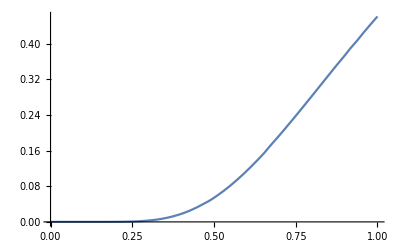

0.116015

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{α→0.602346}}

```mathematica
Clear[α]
taRoughnessFunctions=Table[ListInterpolation[Table[taNorm[[θ0]][[y]][[3]],{y,1,countY+1}],{0,1}],{θ0,1,countX+1}];
Plot[taRoughnessFunctions[[64]][α],{α,0,1}]
ref
NSolve[taRoughnessFunctions[[64]][α]==ref,α]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve :: ifun will be suppressed during this calculation.

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve :: ifun will be suppressed during this calculation.

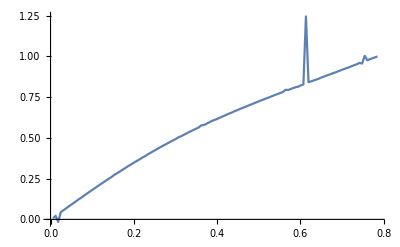

```mathematica
Clear[α]
roughnessMap=Table[{N[(θ0-1)/countX*π/4],α/.NSolve[taRoughnessFunctions[[θ0]][α]==ref,α][[1]]},{θ0,2,countX+1}];
roughnessMapCos=Table[{N[Cos[(θ0-1)/countX*π/4]],α/.NSolve[taRoughnessFunctions[[θ0]][α]==ref,α][[1]]},{θ0,2,countX+1}];
ListLinePlot[roughnessMap]
```

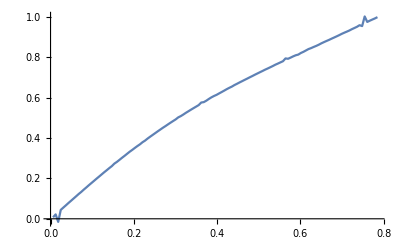

```mathematica
roughnessMap=Delete[roughnessMap,100];
roughnessMapCos=Delete[roughnessMapCos,100];
ListLinePlot[roughnessMap]
```

Let’s fit this...

{a→1.,b→2.00492,c→0.161163,d→1.,e→0.87451,f→1.}

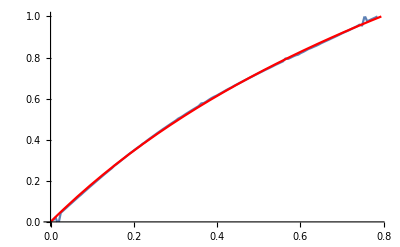

```mathematica
Clear[a,b,c,d,e,f,x,model]
model=0+b*x+c*x^2+d*x^3+e*x^4+f*x^5;
model=(0+b*x+c*x^2)/(1+e*x+0*f*x^2);
FindFit[roughnessMap,model,{a,b,c,d,e,f},x]
f2=Function[x,Evaluate[model/.FindFit[roughnessMap,model,{a,b,c,d,e,f},x]]];
Show[ListLinePlot[roughnessMap,PlotRange->{0,1}],Plot[f2[x],{x,0,π/2},PlotRange->{0,1},PlotStyle->Red]]
```

```mathematica
Sum[(f2[roughnessMap[[i]][[1]]] - roughnessMap[[i]][[2]])^2,{i,1,Length[roughnessMap]}]
```

0.00607441

Let’s plot and compare with the 2D model

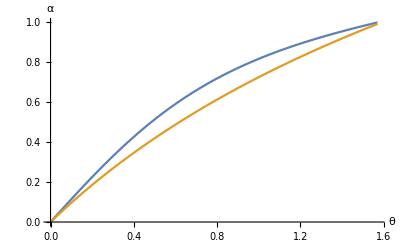

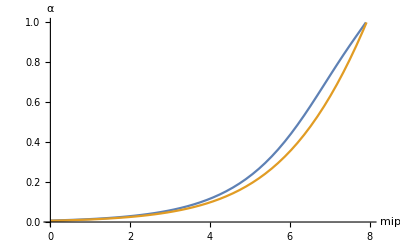

```mathematica
c=1/(√2);
sqAlpha:=Function[θ,
μ=Cos[θ];
(μ^4*c-μ^2*c-√(μ*(1-μ^2)^2*c))/(μ^4*c-μ)
]
sqAlphaMu[μ_]:=(μ^4*c-μ^2*c-√(μ*(1-μ^2)^2*c))/(μ^4*c-μ)
sqRoughnessFromMip[mip_]:=sqAlphaMu[mu[mip]] 
sqRoughnessFromMip3D[mip_]:=f2[mu[mip]]^2
sqRoughnessFromMip3D[mip_]:=f2[ArcCos[mu[mip]]]^2
(*Plot[{sqAlpha[θ/2],√sqAlpha[θ/2]},{θ,0,π/2},PlotRange->{0,1}]*)
Plot[{sqAlpha[θ/2]^(1/2),f2[θ/2]},{θ,0,π/2},PlotRange->{0,1},AxesLabel->{"θ","α"}]
Plot[{√sqRoughnessFromMip[mip],√sqRoughnessFromMip3D[mip]},{mip,0,mipMax},PlotRange->{0,1},AxesLabel->{"mip","α"}]
```

Let’s map the inverse function now:

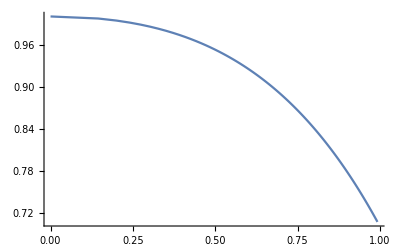

```mathematica
data=Table[{ N[f2[ArcCos[μ]]],N[μ]},{μ,1/(√2),1,(1-1/(√2))/100}];
ListLinePlot[data,PlotRange->Full]
```

(a+b x+c x^2)/(d+e x+f x^2)

(a+b x+c x^2)/(a+e x+f x^2)

Function[x,(29.0706-22.8918 x+2.3001 x^2)/(29.0706-22.8935 x+5.92586 x^2)]

7.69793×10^-11

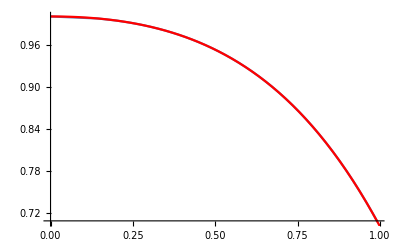

0.990744

```mathematica
Clear[a,b,c,d,e,f]
model=(a+b*x+c*x^2)/(d+e*x+f*x^2)
model=(a+b*x+c*x^2)/(a+e*x+f*x^2)
f3=Function[x,Evaluate[model/.FindFit[data,model,{a,b,c,d,e,f},x]]]
Sum[(f3[data[[i]][[1]]] - data[[i]][[2]])^2,{i,1,Length[data]}]
Show[ListLinePlot[data,PlotRange->{1/(√2),1}],Plot[f3[x],{x,0,1},PlotStyle->Red]]
√2 f3[1]
```

Let’s plot and compare with the 2D model:

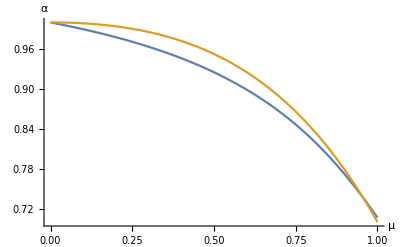

```mathematica
Plot[{f0[μ],f3[μ]},{μ,0,1},AxesLabel->{"μ","α"}]
```

Show a plot of mip level as a function of roughness